# Mendelian Inheritance

Mendelian inheritance is a type of biological inheritance that follows the law of segregation, the law of independent assortment, and the law of dominance, proposed by Gregor Mendel.

## Mendel’s Law

### Law of Segregation of genes (the “First Law”):

The two members (alleles) of a gene pair segregate (separate) from each other in the formation of gametes (sex cells).

Parental genes (Aa; F_1-generation) are randomly separated to the gametes so that a gamete contain only one gene (allele) of the pair, A or a.

```mathematica
StringJoin @@@ Tuples[{"A","a"},1]
```

{A,a}

Offspring (F_2-generation) therefore inherit one genetic allele from each Aa parent, and has one of three possible genotypes, AA, Aa(or aA), and aa.

```mathematica
StringJoin@@@Tuples[{"A","a"},2]
```

{AA,Aa,aA,aa}

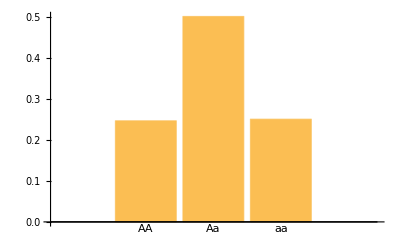

```mathematica
f2 = Table[StringJoin[RandomChoice[{"A","a"}],RandomChoice[{"A","a"}]],{i,100000}];
BarChart[{Count[f2,"AA"],Total[Count[f2,#]& /@{"Aa","aA"}],Count[f2,"aa"]}/100000,ChartLabels->{"AA","Aa","aa"}]
```

### Law of Independent Assortment (the “Second Law”):

Genes for different traits assort independently of one another in the formation of gametes.

For two different traits (A/a and B/b), each on a different pair of genes, there are four possible types of gametes.

```mathematica
StringJoin@@@Tuples[{{"A","a"},{"B","b"}}]
```

{AB,Ab,aB,ab}

With the two pairs of genes, both parents produce 25% each of AB, Ab, aB, and ab for 100000 random gametes.

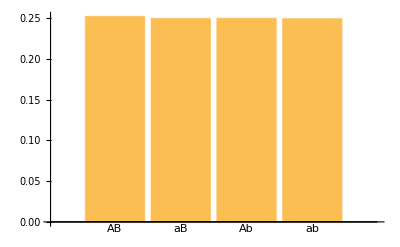

```mathematica
gamete = Table[StringJoin[RandomChoice[{"A","a"}],RandomChoice[{"B","b"}]],{i,100000}];
BarChart[Counts[gamete]/100000,ChartLabels->{"AB","aB","Ab","ab"}]
```

For AaBb x AaBb, each parent produces four different types of gametes and these gametes combine with each other in 4^2=16 different ways.

```mathematica
TableForm[{{AABB,AaBB,AABb,AaBb},{AaBB,aaBB,AaBb,aaBb},{AABb,AaBb,AAbb,Aabb},{AaBb,aaBb,Aabb,aabb}},TableHeadings->{{AB,aB,Ab,ab},{AB,aB,Ab,ab}}]
```

| AB | aB | Ab | ab
AB | AABB | AaBB | AABb | AaBb
aB | AaBB | aaBB | AaBb | aaBb
Ab | AABb | AaBb | AAbb | Aabb
ab | AaBb | aaBb | Aabb | aabb

It can be experimentally(computationally) shown.

```mathematica
gamete1 = Table[StringJoin[RandomChoice[{"A","a"}],RandomChoice[{"B","b"}]],{i,100000}];
gamete2 = Table[StringJoin[RandomChoice[{"A","a"}],RandomChoice[{"B","b"}]],{i,100000}];
ff2 = Table[StringJoin[StringTake[gamete1[[i]],1],StringTake[gamete2[[i]],1],StringTake[gamete1[[i]],{2}],StringTake[gamete2[[i]],{2}]],{i,100000}];
DeleteDuplicates[ff2]
```

{AABb,Aabb,aAbb,aABB,aaBB,AaBb,aaBb,AabB,AaBB,aAbB,aabb,aabB,AAbB,AAbb,aABb,AABB}

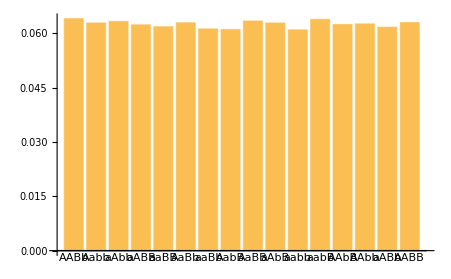

```mathematica
BarChart[Counts[ff2]/100000,ChartLabels->Automatic]
```

### Law of Dominance (the “Third Law”):

Some alleles (A or B) are dominant while others (a or b) are recessive; an organism with at least one dominant allele will display the effect of the dominant allele. For example, when the dominant trait is red and the recessive trait is white, AA and Aa are red, and aa is white.

The phenotypes of self-fertilization of F1-generation(Aa) show a 3(red):1(white) ratio in the F2 generation.

```mathematica
BarChart[{Count[f2,"AA"]+Total[Count[f2,#]& /@{"Aa","aA"}],Count[f2,"aa"]},ChartStyle->{Red,White},ChartLabels->Callout[{"3","1"},Automatic],ChartLegends->{"AA or Aa\n"-Graphics-,"aa\n"-Graphics-}]
```

-Graphics-

For the AaBb parents (A: yellow(dominant), a: green(recessive), B: Round(dominant), b: wrinkly(recessive)), the phenotypes of two independent traits show a 9(yellow,round):3(green,round):3(yellow,wrinkly):1(green,wrinkly) ratio in the F_2-generation.

```mathematica
gen1 = Total[Count[ff2,#]& /@{"AABB","AABb","AAbB","AaBB","AaBb","AabB","aABB","aABb","aAbB"}];
gen2 = Total[Count[ff2,#]& /@{"aaBB","aaBb","aabB"}];
gen3 = Total[Count[ff2,#]& /@{"AAbb","Aabb","aAbb"}];
gen4 = Total[Count[ff2,#]& /@{"aabb"}];
BarChart[{gen1,gen2,gen3,gen4},ChartStyle->"Pastel", ChartLabels->Callout[{"9","3","3","1"},Automatic],ChartLegends->{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

-Graphics-

For each trait, the phenotypes show a 3(dominant):1(recessive) ratio in the F_2-generation, confirming the independent assortment.

```mathematica
{BarChart[{gen1+gen3,gen2+gen4}/100000, ChartLabels->Callout[{"Yellow\n(*
GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJy9ewl0Ved1bmImIenOkyZAgDHYBs/BMWADHuMMtkMTJ22mxk3iOm0zp3lp
M/QlWelq85K0L2tlcIzBBmzAzIMQkhBCA5LQBJIYhdAEmqU7nnP+YQ/vP1fg
pKvr9bVrdb2ztsTVuUe6//fv6dv/3ix+6aubvnTbe97znm/mmG+bPv+djd/4
xue/+yd+88PHv/LNV17+yhe/8OxXvvXFl7/4jfe/NMvcXG++Hjdf7mv6r1xI
NtIU0jRR2n2NElEDgkZSyIpIkVYsNWsgviWI5keWRswjQADmZ/eVKzfvmjvZ
h81z2vyyMgKgzR+3iTJMFpH+L63z/3UBk2IWxAaOBWRpsnV22YpRMgoCIwYL
oWCzBkwiTgAOAw4YQRoiGmOaZndtDpJU5nl2H5VkdoSEJiFZCJISlVJZFGnm
jLs9/30X3xRkguz+GCWYrZ3ZXbOEjNRxR01KcY3s02RVQeaoSu8Rqe1OarOT
3iwzW7W1k5xDLKtY1RF0aBxUNKl5GjgFZAMpQDTaMmL+JTLILPzv1gVmxeDg
GUFmAAaL1QSLa2Cdlck6K17hTG6H0R/B8LfFja9YQ19ID3wqOfDx5MDH0kOf
tK9/To58GSa+jVPfx/gvdHqftk+C00DyLOsexmGmOLPFbDSusyZm9CXQ3bT/
3Ar/E5cxAIdAzwAxEIwRiwSne3mqAUd3qaFf2P1/m7n2stWzSVxY43Tdlzm3
Mtl+e7x14WRL0WRL4VRLcbxtUarjDqtzldN9v7i0QfT/ubz+TT38Qxz/35zY
yVY16y7mG8wJYoGulZLD+J/UxL9d7P8VkSLX1lUWAZFNchiS7Wpkn3PtZ9aF
l9Pnnk23P5Bpu8NpWagao6ohJOqCzim/Ve3JVOWlK3NTWUlX5WZO5NnVeXZt
KNO6LHPuPrtrrXPpY/LaN9TIr3T8MDhnURtXsswHOVnFaFf1/8HFt1C8u3K4
Jf/2Rvab8TFh3NvEGUiicwmmy+XQr6xLX0m2fzB++q54bShZO8eqny0bcui0
jxoCVBeimjBVR6gygsfD+lhQlvnE0TznyFznyBz72Oz0yVmp2tmputxUw+L0
mQ3pzr+wen7qDO9SySYlByVZRhH2LV3gH+SWaf+xmVPWVw0SMDEuQ9oEFgdn
njXrNgHVIaXYIndbBAslbqjJOnH1X2X751TdalWzVFVHnRN5mZqcVGOu1ekT
V8MwVKAHCtTVmLoU0+cLsbMIOop0a6FsKhANUacuLOojsj4oT81VJ2epyhxV
HnTKSlJldySrVqeaX1DX/gcltyG2Ag9rtrQbxNgxkdGIG9PcYEZuaDahxRhd
egaFUZlZL2rJKs1qmsByE4EBJlzDIYdM8La0sOW4SnWqkYPi8k+tpk1O1XJV
lgvlc7BqNtTNkq259qWIc2ORTCzVzlKVKZXxBXK8WA4X68ESfa1EXSkW54ud
c8VOxwJ5tlR3LKAzfq738Ak/lQX0fk9m99z4nnnTZdFMyxrV/4pOvoaqnrAf
KCnc/eUUcZIxw5ZRU3bRJjoadcVvomCWbkQwRiNZ2kZQCGkrE7cBs7pSGUwP
0o1KvPAz0fbFTONTmfpVTt0SVb9InC5yWsPiok9dD+l4ibaWg7ibxAqyllFy
CU4tgrESfb1Q9RWInphzIeJ0xWRXkepaAF0l1FXAHTFuLKSTMTDqOJyfPJQz
ecQzVrVoomlD8tLfyNFfk1VBcEHzpAksaYPCTYS2cHc2i8IsGFK3ULg5y0Rn
7cZ+E3kk2UI7ShrNMSqYhmQX9e3l1r/jE8+oyntETalsKVTdZntLMz2L0n2L
xdgySN1N9n0qdb+aXsVTy3hqKU8v4elFNFkMozF5Pez0hZyeoLgcVhejcKEA
LxTR5RK+sJDPLqKmBVhbqKtDTmV+vHze8JH8wbIFIzXr0mc/R0M/ZWcfcaem
pIOYQcqQcFGAyxHY2Lq2ZlAoVzHKcT3XzWluNnaMdWmNYEHaSp2z+9+UzX8N
5WvoQASP+fB0kC7HcKRIxhem40vSiZUq9Siln8LpJ8TAw86VFfpKCfYV0XAJ
Ty6g6WKciqnxkBgOyKGA6g/o3iBcDuKlCPYU05VSOr+UOpbQmUXcVAT1Aftk
zviR24b2zR06EJ4+vlK1Pk9TP2Q+yNirwTIuYYMUxnPNxhsgSpOSMygkSYuF
6zhZLZlg5FIcw2V00kpdnO57Y+LMXyYqHrLKQrJqDjb5+dICHl9G1gqt7xTq
PmGtw8mP0ODzeP5p2fRg+tTCidr8RGu+cyUEwwU0XUjJGCTDOh6EySCOBnDQ
D71efdkvLkfEpRJ9frE+twTaFnPLAj4Tg0afc3JesmzWxIE5k3s9qfIlsm8T
Of/Mspb0OLjsy5iNMRzjEWb7XTZ3C4WySDhGIwQ2gnQZnmFmNqZ67MF9k21f
G61+ZLoqnG6Y63Tl6GthHF+C1r2oH0HYCOJZiD8H/c/rc0+ZkKWPL08dCQ+W
3TZSOyfd5dPXCzheTFYR2TGyI5SJUDxEo34Y8MiefPuC3+6Oiq4S4+yqdTE0
L6TmQmoOm0Cta3KtY3Pi77x3au/8zLlVauIlSr/J6qJZeZZ8Gn8Vbgw1vqxv
5gtlbhlMJB2y02ilzQuDxr6B14+L9u8nap6YOlmcacsX17xiKipSUcdaIMW9
IJ7hzGd48ksw8BnR+bR1+h67qhjKo5kyz1D5rJGGnNSFMAwv4FQpi4UkF5As
ZlHImShNBWHEq/ry5IV80RkQZ2OyvUSeWSgbSlR9IdRHqdG4fARrfNaheVN7
Z8cbQlbPOhz/AdvVjIZUQ5Yqy2wmwHdTRzb0GpAZAQmbEhanbTUqx0+r7l/I
muftE0vtRo/s9anpiHCKHFkoxCLt3IvpJ3nyRRj8M3npo/bZdZnmO9J14fSJ
vPjJ+RNNvmR3TA6U4vRytu5keQeppaRKSS5ku4hSEZgK6Ov5+tJ81ZmnzgZV
e4FuKTEoxKlCcTKqa2NUX8C1UXncmzw8L149N92+BPo/zYktrC6bTOgyuCwL
dRn9H3I4G4BaprWKa5rWNCYynVbv61bTX4jKlbrWj125OBZRVqEjioRYoJzb
ybqH4w/TyKOy9zHn4jqne7XVeVeyo3Cscd54S27m6kI9vIKn72HrAZZG7iV5
N8rlJG9nsYitIjRAxn1wdR50z9OdHjgXxrYiaDQoiuyqqKiKwMkonSqA6rBT
6UlV3pau98sL62D0B2TVMEybBRs7gmxRQu+yE3YVA1qhMnk6TplLeuRA+ty3
UvXrrdqYbs+jXi9OFMhUgZOOKWsxme1N301Td8DwYtW/TPXeo6+tFVcfTl5c
ceOsd/SiT0ysoPT9bL+P5SMs17B4mMRDJFwsrl5EKdjFOhGCoRzomQsXc7Hb
Tx0ROlOk6wrliaioDIuqkKoJQW0YTgVkxWz7xFyrbZFz7dN6egfJG2bF2gVi
vNeQxpvqmCm8XCJoSq90nG806PM/TzU+nzh9e7rdK696cdh4dJGOF8hMGO0S
tpboRKkaX6iGS/XwSrjxfhzaIPrWJHtWTfQsmB4qsVN3Ked+Ld6Hci2JR1k8
xs46Fu9n9SCrlaiWablQZYw6cnFoHvbmwoV86PBBcwjqI1ATUdUhVR1QNX4T
0rkxiFU5omJW8nR+4sIT1ui/aKcfsyhMhjbMCFjeynq2ZFOEAtuaRoehc7eo
ezl96r5kSzh91StGwzBZTKMLKF6IIkwioJKB9Eg4M7RU3XgEJ5+jqU1w4wm7
94Hk1eViZKWIr0qk7kxkVmasB6W9FpyN5DzF4imWj7NaS/oB1CuUKlV2DJNe
nsjDoXx1ab5ozxGNebrBT/URqgtTbYBqvdTs55YAV+fL43Oma2ZPdDwQH/y+
zFw0vq2ypE5wxuS2GTYLJj+DdK0qNSz7Djln/sY5+ZCsK3LOBu3+iJgs1KlF
nFzGieU0viRzKTJxJjhyelG861F141OUfJlTn6bxDWr4Lmd0oZNakrHvnrYe
ittrU84TtvywVB/T6s/AiH4R9UdIbyRldHQXiFJyIpj061G/7PUKE5bbgtgc
5dMFVBvGmgDWeKnByyY91YShwmeVz8vUldoXPgZT21FfU6QMwRZuhha36Ddl
62mtx1vtrh/YDatFTR4056nzIWewRE4t0qmlkFxJY/erS/eMlxf1vx0b3Lcq
3rwJRr/G1lfZ/hTH13H8TsyUWnJxUj2YdF5IiU9n1Odt/YqAryr8hsKvKXgF
9GdQvcByI8uHWd5NsgTSETkeFgNhdTlKXUXcVsKNRXgqDCf8cMKDNR6u83Nt
IVUW4GEPVYS49QEe/hY5FW6B7KrDGJKcAeESKw0Qj+OVcqh7GaqXqfr3Wp2z
M30BZ3QxTK6A0butq3elO1cmG+8ePVx8Y0/h5PFV9vkPU+ILLD/PzkcpsYaT
D7K9GmCjgs8I58eO+LlQP1f6lxp+ofGfNP6Dhm+D/hKqT6B6ltUGVg+xWAzp
mByPuCiuRKm7kDsKubkAa0NQ7dNVHqz2UI2falwUdNjD5QFuXsWDf0WZgxqT
t1Dc1IVg4xgSRvq5fRsf38RVRdDyHqtvdmY0KEaWwuBKdfm+6ZZ7440Ppk+/
L1G1PFG11G65BwY3svMCw3Mkn4LUGkxvIOd5hr8g+AmIPSCOgDqAei/CWwC/
1/hzDd/X8Ncz6iBtgDzKzjJMFqqxqBwI654IXYjy2SifCWOdX1d7DQqo8tKJ
AFYXUGWMDnvpmJ8aVmDvS5jYqXFiBoW6hcJBtq0MDJzlpv9FR9fRySCdvw0n
c9VkVFxbojpXOk0PTdStSTY+ge1PU+sjePYe6l1FUw+yXku0FmEt2I+C9Rza
L6P6n6jfJFlPsoXUadKnCI4hmA/9jcKfKPg6wEukX2Rt7OoJkxAxXqJGC9Rg
BK6G6VKIu4Lc6scGrz7pUVVeXeHHyhCcKMCKGB/24VGvPrVYXXxRTb6m9aBk
bVBIuolCS6mnr9PlY3D6W07lPbrFw32zedyj+6N220KrYWWmfm2y8Vmr+Vnd
vJHbH+ILd/LAYppaDPYdAKsQH0b9NKnPkfweyt+iOkDaMLdGgtMEpsw5gXRA
0+uK/lnh32r8EsCfot5E4ilK3Q2TC9VIkRqKwLUgXfHzeR93eKnReIRXV/qh
PGQojaoo0MejdDhgXEOeKLY7P+SM/lKpS4odZVC4h3vk+rYT57EO7PytU/+p
ZMPtpuThwVzu8am2SPrUolTDg1bLU7LtBdH4lFV3n25fzj2LeDiGU1GdLtZy
BdAjyM8hvYLwj6i2oTqMUI5YjVhH2EjUgFwJtAvoV5p+oPHLGj6l9SZwnoT4
Sj2+SI4Uuyj6A3TVyxc9fM5DTR465YXKAByLQFmBPB5TxyJ0KAiHPKIilunY
YN34kZJtwClTkku3KCWXFMphGq9wznwneWpjvLXUFGV8xURsr1MRTZy6y77w
lO7dhK3PWjX3T1UXinMxNkw1GTNEgqzFIO9RsF7SJoFfFvonIDej2gP6EEAV
glFHJ+N5xjbCSsJtYNwcvqbUp6X4qMw8rifv1qOL1I2imyh6PXw5n7vyqSXf
fDpWBrEsikcKxLGIKAvRwSAcyHfKg+m21db1b2tZCzzlonBrVDYo0LmiR7Zb
TZ9Jnbo31VrkdBWYSl8djdjHb0+ffVSOfIyvf4xr32eVF0/W5jmXvTwVZhlj
tZBNZSpXa3jKoY/b9LKA7wH8K+kdoI66JbPqZNXP+jrrqwzNDPvQhCz1Lel8
VtgflamNevxOPbzAoNAGxUCArnn5Sj5353Orh+p8VBkkg+JwzCkLOUeDdCCE
B/JFuTfTusoaekWLY8gj6EZXk+gYQelUq+j/hXXmI3b9MtEUthvCVnWxdWyp
07xGDn9cJz+DfR+kwyXO4Zxk21x5I5ftAGOMYRG7vGgd6A+6KPglwV9D/gfG
V0lVkGxj0cNihOU4ywFWLaT3o/qFFt9U1mdlZpNKPK7HlsNwiR4u1tejeiCI
fX7q8XK3h1t9XBdwURwN46GwdTRoHzUQonTAo47lW63LrKHPKmcP0qAhVKbg
y6KQ9nhd8uIP021PiqZF0OB1qgKZylLRtFpfewETL6mRT4j298sDXlk1W17N
1fE8rfIl+qQs1NYKtNdo9YxFz6f5RYs/C/iXrH9MajfJEyybWXSxNNJE6hDq
34D6nhYva/uTKrNJJ57EseU0UozDxXAjBoNhY1TY4yfDDFv9VBfACuPOATgQ
sA2KsjAeiPEBD5TnOm2l9tCLytqG2MvsVhouCi3t6zWJjr+b7lifaSnEhlxV
FXBOLVdXnsTJT1P8C6r7Q9aJO1Nlec6ZHBoNgu11cH4a59sipNK3g/Wwkk+k
6ZkEfzBFz2n1cZZ/hfrnqDejfovUPlJ7UL8B+mdaf1vrl7R8EewXwNqEyQ/w
xAoeNQytmIYL0KijPwQ9QewOYEsAa/1w3GfcWe/32mUB55hRRAEf9NDx+aak
cgZfUJnXEC6555R0EwUONjjtPxxue2SsJSCb5mFDDNrvkyMf0lN/xv2fpJOP
ikNLphr86SsBmi5Qym/x/BTn2DqEYpnhEho2pvnxBD+Roqe1/DDJT5hwqujr
ir6r8AcKvyfx6wL/3MHnJTyp1ePoPEPWRzn1QZ68k8eKjdBoIRp19EegJwzd
QWgJwCkflHv1gTy1N885FpTlBXSwkA/6qMKgKHIGPyxTvwF9wT3smNEFKB5t
093/NN66euKMR7bm4tmlePUxnfiInnoOLz2hqu61j5UkzgWs4QBkwkr7HfRY
4JU6RmoZG44KawQ9atN6Bx4H8TTJDwJ+BGiTxhcVfFLCixJekPiMxPVarwG5
hqzHKP0UJR7jiSU8GuWRGF2PYn8UeyLYbcqlMDaE8EQQjwRgr1ftMdHVL6ti
+tBCOBjQFXNFa0j0Pa3ivwZ5IdsUgJso4ufh2q/SraszTXmqw6cv36uHP0jp
D6Nhqt33pGuXpOoKxGWvnszT0qOVT8uAlhGQJWjqUH036/sJ3k96HakNJDaS
YeB6I7vcdYOW65Vcr9V60OtJPcbyUbLXYuphiK/GyVU0WsA3/DRkolPATdyd
YW4Nc0OEq6NsTOhgFHeH9G4DwStqIuLIEudQyDk+y2nOFT0bYPJ3KC6ie1jj
3ESRvIz9v820PWI15eqzefrqShj9AKU+hCPrxdmVqZrFqbqY7vHidB4oD2gf
yCDIKMhiNKW0voP1Sob7Wa9m9QiZrZbrXLInDaLHQDyqxTotHgXxGIn17DzG
mXWUeASnHsbxVTQcoyEv9vuMU+N5U+4FuTnEtRGujPLRKO2LwK6w2hUQxz3C
1E1li+WRoF1xm+2i2IjTm1H2ZHtoMyg0J3uwf3Om7VGrKU93zIOry3B0Iyee
haENzpl7klWLUzUxMDEwno/KC9oPyqAIg4qBKia9mPQygrvIUBF9H6r7Ua5m
+RiL9abKA2edzop5gfY6ttZxag1Nvx8nH8bRVTgUw34v9Prgkg+6fNgWoMaQ
qSa4IkKHw7g3rHeG1M6Ac8Qjj4ewbKE66rcrZ1lnPKL3GUpsJ9Vvqm9T8d1C
0YcD26z2JzNNPtUxB68u5NFHePppfW2DXX9P8lhpqjoMJh/F80n7EPyoAy4Q
FUYVQ11EegFBKcJSgGWg70C1kuX7WKxG8T7tPKRsV8B+CK2HOP0QJx7kqfto
/F4cXg59Ed3j0cZWu726ww9nAlhvPCKEx0JoMvWeoH47qN4KyP1efcS4iUnE
Hqtqdsb1ixcotZf0DeMVArMMxKBIX8ehvfbZ563mqGw3KAp49H6e3KivPGad
vDdxaFGqIgSX8ziex9pH4CdtgPhRBVCFUIdRRxEKEIoAio2gLmW1nOUKEsvB
Wa6dFUbAXk6Z5ZxazvE7eGIpjS3B6yX6alBf9OjzHn3Oq1v90GhCUxAM8Tga
xP1B2B3UbwX0jgDs8ZusoQ8EncPz0ifmZDoWyqHPUqacYNygcIBmUFBmDIfL
na7P2WcWi7a5cDXIoyYGrtEX11pV9yb3LUofC8KlPJ52UTD6GHykva51KZ8L
x6gGgu8K6girQpZFJE2dXgRZQbuIMkWcLOSpAh6P0HAIBwLGkHSXF855od0H
zX6oD0B1EMqDeDiI+4KwKwgGwvYA7Q7B3oDzTl7q4KxE9Xyr+149+g1yGhDj
aqZzNsNp7TiO14uLX7db77Nbc9UVLw0v5uGHoPthp2Jlam9JpsyPF/J5Mp+l
l8FrILgotAdVPmgjHlfAoyEf0IPmLekn4UcRQBEkESInRFaI0yGOB3ncR8Me
HMyD3jwXQocP2314xo+nTaYLYJVhgAFjTrgnhDuDuMMVfiei9gSSO+dNHpg9
XRsVPc9Q/GeGEgBmJLk9ixkUKDIwfU72/NRqezx9Juxc9OmhErq+CrseUJV3
WfuKrDIfdnl4LJ8cDykj3qy4KFDnwU3J1ZALmIc6Hx0v2j4j5ATIDrIVdCEk
gjzhp2EvDuRDby5cytUdXmjxuxAaA4ZyuNWZYR1HArQ/SO+E6O2QgUA7Qrw3
JveGpnbljB/2xZtWqqGX2Xqb9IAiKQwKk79nDg+0Uqk+2fea1fHJRNOSVFfI
6SuAwTu4eyWeXCEOFTplXjTFi9lDKx+Fh4SXpc8F4qpjRiM3sSDkGUujTIAy
Yfds2YpSOsbJKE/HeCJKN8LUH3Tj6kUPdnqgxQdNWQj1QT4VpKoAHQvQoQDt
DdKuEL8d5h1GIrwvJg+Gp/b5JquWpjs/rCf+mVUd4JRgdLJN5VvNUxbOhBo6
aJ37ytTp+6fOFqSuRtRAKV+4g+uXKVOnlPuwxQ8DXpXO07a71SQMCv+MoPKB
G4GNXRkz85L0cybsnipnYpQuoGQBTcdoImayAw5EsCeEFwLY5RoSNLq+gEYL
tQGqDtJxQ2IDdCBAe4K0M8hvhXh7mN+K0P6wPBpJlhenm9fJvq9hep/hgZIc
m9l26+6brVWjFEel1Ei91fXj8Yb1o20Lpy6HRH8xXV7MzYuhMqqO+3RTUPX6
RDJXWfmGEJLjJxkgFZyRbOB1wy/qIMkQ22G2IpyJcCpCiQhORnA0jIMh6DUe
7ccuL53zYqtX1/vglB9PBfCk8QijiKBblu4L4O4Avh3gHS4K2hFW+3zieMRp
uFNf/gRP/SsrU+UlbbdBRhmGbA/j1hmIsmCs3er65WjtB26cKR2/GLCMUfUs
ovZSPBnRlT55OuT0+Jz4fJHO1RkPOn4WQVYh1mHWEVIRnBEdJRVm4WPHx7aP
015KeGAyX4/k6cFcfXU+XMzB7hzqnIet83WtV1f7odqPJ7I83PVrE1cDsNMP
b/nJ+PU2gyLk7MmxK/zQcT8Nv8JiF9OAKSkMhCTpNIt3z0BcXWgJU/32ld3j
zV8aaX3fxPkC+6rhyVHuLKL6iKoKpk+GU+d89uh8GfdAOkhO2AQfE4JQhlBG
SEZdEVmxQ5zxciqfEnk4lYvjuTA8Xw/MNxDUhRzdmaPbc6A1B5rmw6lcfSIf
Kg0JD0JZEA779X6f2u1TOwJqW0i/GcI3TLCNpI4vT7ZtUP0vUepXRKaQT2jk
DHAGtZOd6/lDjxUJMkKOdKeuvBrv/lSy8055Pp8uzuPzfm6JieqCicPhyVNe
qydfj4U5Vcx2MVpRlfaLtE9ZfnRCbJn7JhCFeNqEUzcWwVA+9OXD1Xy47DU0
Cc4FlGH+p/2i1idqArLGizVz6MQ8PObXhyPqQETt98k9+WKXx94WsrcU2K/H
5Os+ubtkuvuVieQbGadMQSfSJJjiVLkHzRr+aPLAnX1BG0zNx5AakyOV6cvf
TXSsTbf55blZfCGXz0XV6QWJY0WJar99Ngeu+XnEZK4CGA2JG17nhkeM+PRo
EEeCeD2AgwEThfhaiHoCcNEH3X7oDGBHiNrCdCYMDUF9yqdPeHSVV1d6oCoH
yufDYS/sC8E7EdgZhbeientMbCuythdndhbaewJOxe2J6/8Yx2abLmuecDuO
4I5hKWnyNWYHhG42kxxQGa1cmi5TlOi0+349ffYTE2eWptpyoTuHu0PYvkDV
LhY1YdE4G87m8cUAXwkZP5UXvOKCV170q0tBfSGgu/y60yw7SF0hPBuCNlPv
hKg5wk0xboxxfYRrAlzl4ePzuTwHy+ZLQ/MOeWG/l3YHeUeM31jIW0rpjUVy
R7G1tyhzfKFdt9g596g19ZqBoPg6cpJNNWFQaFIKNLitPLplUQIdGy335N+4
iDOqRqsyl38ydfYD0+0LM2dz1Nlcao9S8zKoLVYn5mNdPjcF+EwIz4TASGsE
2qPYHsHWkMsimgyX8Blep5sD+nRQ14XxVIxriri6iCtibALpwXzcN4/2zoY9
c2xTAe3xZyEU8tZS/v3t9PsFekvQeic3VRHMtN0trn4Axr6tnVOap5HTbooj
owI2pEmbCxyTvoEyN7uT7oxYtp2BmpVFyV41cihz9Tvx7g3THbFUa54wqzqz
FE4t1OVB9+C62iyskE4VUm0h1hVgXVTXGVPx6po8XZOra+fLulxRmy9OemWV
qc6ieLyIykroUJEh27DTp3fk6m3z1PZ54m2vId5uXnizgDeX0KslenPQeSsn
XTYv1VxiX3tWTf89iX2EA27niyA7upItUrNZDtDWmH4XBXDWXYxlGd9wX2Yo
0wPju6y+r051vX/iTPHU6VCmYYGsXgRlxXRsAR9fxJWlXFVKVQuwokCVB5yj
ufaRuc7R2ap8lqq8za66zaqYZR2b5xzNl0dC+lAh7i/BPSX67UK1LSK3BMTr
XrXVizsC9FaAtvloqw+3ePTW+c7OuZkj89OnizJXNsjJ74JziKmfyTYrN+5g
2DeAy5rc1iq75gTu4I24GaOyHWQXBTnuAJR5VCQ5eVaPbbH7Xkme3zjdetdU
w+2J4yXWvqjYXwCHS/hYKR9fwscX09FiOBCS7+SJXXPF7jmwd44+MNs+cJu1
f5a9d66zJ1+9E8J3Cmh3Mb1djNsL4Y0YbAkbs4GtxpBMOvCpbTn29tnpne9N
7X9PutJrnblbXPkTNfYjyBwmuEyccgf83MkO49So3ZPAm5OV2YkPDXCzr+dO
tplnjH+48zvZssMdA5zkZAtNbVHXv5W+vGmidd2kCRfvhFK7jN2aqFiIhxbQ
oUW8v4R3x3B7AN7w6q0eetOL2z1iR66zfb7Ylq+2+cGwCOO5RrZF6Y0wbQ3S
G3428qaf3grpt332ztzEvvmTx/Im6/2Jrnudgc/B5K85U89yiCFBaLnByPVo
UEpqLdCUd25bz+1DzijoJgrt2pPBgSxMMW7CsXQQLMX2ODsdlNqtxv8xfe2V
dPMTmcOL47uik9sCU1t9qa1+8UYY34zxm4W8pYg2F9Pvi/l3JfxqCb5ejJsL
cXOMXo/SlghvDfPWAG/x4OYc2DwXtsymrbNxm9FdnrU/nD5amji5Kt66NnH1
I5mxr8j0qyhbWE+65/pKsLQpOw2pQbruDDbdRJEdcnXHVm+igJlBVreppA3d
lTo7U+T2BszdaVbn3Q5U4nXV9x155oXE8bWju+8afL34+m9DE7/xp34bcF6N
qNcK4bUSfHUh/mYh/q6UX19iYiZvKeatJn6GeZuftuXDthz55hyxbbbcMVe/
PU/t8aTLipMnH8g0PW91/5U98GNn+nfCOaiwBWnUbdGBm4zdASE9MyxnvMCd
gDXW4jbt3Vp7BsUfptYgO7yrgCSgmhmyA7fb5PaQDVvBG4RdbB/Dsd/Y5/9+
4uRn+/Zs6Nl6V++rxYO/DY791pf8fcB+PSS3RMRrEbWlgN5ayDtL+O0Y7wzR
bh/uzdf78sT+PHu/xzoYsI/E5LFiUX1XsvUDqQtfFn2/gLEjlOokOQg4rmhK
c8odVoFsJ1Vmx3hd8zHuPDOwJrLxirMh1zjxu9N32vUUcB3EpPXslIUbCcxj
xtddN0GZzTg3WHSpiQqrd/N0x99P1H96rGL9yIHbR3YFxt+eN/32rOTO25I7
35vZNUvumSf3zhP7ZouDt8mj75UVs0T1fOdUwKkvFk0rVNtqOPeYvvyn4sYv
5fQhSDeSM8Aqw+4ok/k0swTjodlml7FxmV0DzAx6SBeCO1iXPe2H7H18d2Y4
G7Ugu/+YNTODwk2T2VnCbHwzfyL7jkQ5jplujFfAyGui93vJc5+aOL1xrObe
seo7JqoXT1SXTp9YmKoqNpKsLknVLkg3LrbaVtidDziX1surz+mBz/Hw13j8
7zjxaxZnGceYp93zmOzc9EyAdDdypqHtTkDNoJhZFWQhaMJbSzURlyT9kU39
m9HId9/ArGRPdLNDzexO1IJFegrFoLa6nURDauJYfGTP5PXtY4ObR/tfHb32
LxO9P57s/dFk30+nB36WuPGr1Ohr1uQOJ3FAZiqzM8AdpLpJXyNMuSnXzWh4
c2g6+3F/WNK7A5t/uPnvV/nvFv0fXq663Tl2dCd7XFxGnya2ZQROW2osJa7H
7WtTmZ6pdGci1ZRMN6bSrenMOcu+aIteoW4omNSUcg8kXUPBrGZvDX3/f7zc
QXzpGFHKyXIYQ4QtoJRGQ/inJUwKPe6oEamHUY+QK2OkJ0lPE8Tdygwdyv43
gewsOcF/bQv/o+v/AIwBWvU=
"], {{0, 63}, {66, 0}}, {0, 255},
ColorFunction->RGBColor],
BoxForm`ImageTag["Byte", ColorSpace -> "RGB", Interleaving -> True],
Selectable->False],
DefaultBaseStyle->"ImageGraphics",
ImageSize->{25.166666666669485`, Automatic},
ImageSizeRaw->{66, 63},
PlotRange->{{0, 66}, {0, 63}}])(*
GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJyNenc8VX/8/7UvLi7X3iMrqyjtSNLUoFKpSGmX2UDRMkJIITIquxKJZIaM
jJC9995333vm71zV5/f9PX6/P37vx+sex/uce8/z/Tqvec5TzcnF5iI3Dofz
wGMbm3N3dri7n/OyJWL/HLvpceXSTecLe296Ol9ydt/oxINNmmMfM+zD2Yc4
A4ZABAJREECxLQShMCYwCoIwCEIg9sHOWBkIwkIQKoLQYZiNHQEAhA2gAICd
iUIwAsIAG6YzoSU2TIZRNgwzQZACAUswsAizF9i0Wcrs2FRPd+/PX01FVbWf
yxuzy4fzqxdq6qj9v5jz7QBzGAKpAAJh1wAQFEJQBEZQAEZZMMRGQADhXAVc
wfZPkJWBgceO/jmEIH+Rs1hsTAAAgLFZFOYIBKAsJspioywIYaEIA0VoKErB
BEFX1oQwsa+xsWWtrB77CvZzMLYg2uh0/4+fFW+S0/0exFy99Nzx1PMzR185
HM8475B/69KP5+4duU+nf2ew5pph9hymBgRGsQXADBZCY6B0JgJCGKr/Kegf
WYEPQSvgsVM4M5wpTN8sFpPFYoEgwFEqNgGyIAodnSajU8vw5Dx7ZJLWO7DU
2j7/q3mhsYXc0snoGIL6ptHhRXSKCS6hrHmIOkaZ7RrvLW+ofpvxwfdejNPR
iGObXx7TSzqtle6k9sFR4/1R/XQbg7QzhjmeZj+izg2VvaAOlqPUcRSgo9ht
ZNIh2jJIX4JB1oqO4X/yd/yxB8wuMFXDEPwHPTaDYWWzMeTY3QchmM1i05Yp
C7SRMbClG276zW6sWqrMHs171Znm3xLv8zvOtzfp2VT6W0p2PpBfBZR1kaun
J0uHuzJrysPfpbreDjli5Wum5m8hknJWvNZPcTJem5K5aumNRr/f6nIHlZS9
hJc7BOJsFAr99g3mPIH6i1HKIAouoxCVzV6kMWdZAA2CgP8Eg/RHoD9GDyMr
wlkHZxIEMNiYqmGEjaAgC6AvLM0NDvcP1uRN5jxd/vqAUXaHUe68XHRoKnvr
SKrxcOK6kVjzkciDg0/tex461d++knftZsY55+RTx1PsrVLPmGY4ar53In25
iv/pJzQcLUH/oAh9UYA/KbJeaw57K5bYCiZuwEWZ8qQfU6p9cnCmIAjg4B9C
oSUmQiaDi0yQCoJMzBYgTGBMn2wYwewB+AsegZAV+CCMrQ0AQDYmEOYnEAiz
AcrS4thof2tbVVtZ5GCOw2zxMVrtAaBpA9ysBjcSgVoB+neBpVyRiURSd5B0
rYdE9imRqB2CEVv5Y634PtoLVbiI//aTbX0g3exLbL5PaHsk2vOU1BtCGnwm
Mxmh1uOjVHaKmLFDIGkTT9ou/kIn9bZQm4WiMGi4EmFNslAqFbN7iMmGWADE
wtD8Bx7T6h9tY24GwHQAAZgoTMdiCmbifxZER9lT4FzPxODv2q62lPGBWPrs
KwY5hLJ4c2nckjmmiU6Jo0vC0JIwfUyU3iFB+SExksX3+xVXTRC+7QVx/J3M
XLrMVJx413182Wm+dHO+uLX4lwYiL9aQXhiLv9gkGblbJWSvQpCV2GtbYtZJ
kYKjPEU2/BVnlfrCTpArY6HFdgSmYPrFohsVc18EBlAMFGbkmI5B9J/NgzCT
DdOYKJuGAFh0Y3KCJwrTAPrY5HRL/dDPLwMN78a64iYHkyYG3nY3+TeWnqnK
WduUKztYTBgtwU+WCM6ViTGbV6FDG+iDJou/TeZLN5JL1lC/aUwny3Q8EC6y
5Uo05A4k8Xnx87nyCFzjF74iKHRelHBchnRKXdx1PSHJgVTlJdV8S6jiNC53
P1/NzTWjKa7gSCHKmkZBlIWgdARlcDTOsXWOi2LBBf47sEjJRtkMhE0FGWQm
5iYgQgNYo9OTDfltRd6d3y8PNXhMtb5sK32ZG+OV5GL94rhmmI1Q7Gmu985c
+XZcVccF+m7ILadawf1uANmLMXmXXHVjOHNPXbBajpNQ/BauEAWeB8JCd/lE
PHj5rgtwXSRwnxPlPUbgNePn2SfK46aL/3SO1BsqPxEjXX9LOP0A36ejMvUP
91B+RqFzbQgLC5pYHoHZWARh/w3dnAD5L/sAMMSEAAwvHWBi0R2zG2BmfrKm
sDvvTtuX7UOVpv3lFuVvjr66c+j2oU23TZV8DQQD1+JebsK9M8flbOGvsVYd
8z7IyPZl/o4bqgmpfns1y8Ui9pjG050i941wd9Rwt+V478oRfJTE/NQID7WE
H+gQfLVEXVSFj0hzHZHguqEknHIIcwqNyderGu/LJu0VCl2Dj7XSrA4+P1WZ
Bs0MoEwaJ/EAAMRmQQAWNrEMBoP/NA9AnHRIZ3MWhjkxSmbRezr6coM6M6yG
8hQXqpWHvmlmPVQLOKXibqnot0P8uQU+cSdPhiVP3l5C5QmNjrsHZlMeLXyL
H/gUm+/nGn5gu6e62FU57huqfLcMCA+3Sobtl48+qhh/UjHZXi79lGzGMZm0
A1LRZsRbRnhnJYGr0oQQE9nP9upNvjrlN1Vid4q5yXJfkSYEWZnkP7k6VJKy
2PWLNT2N0Gkom4n5JSeocDLqX8PBbIm1Yk4IlkvpEDA8sVybO5x9bjzLiFqk
AFRoLH7VboxSrAzXq4kxa0ja8CtuVYO/aNM98c4nemOZZ6erg0brE+rTgjJv
nPE3NnAnibqReO6t4ovcKZ19fd3P53t6sqwHv+4azNs4+EG/L0GjI1iu8Q6h
yFEw3lLqvo74JUmBq1LCvpqkBDP5FCvZF5vFLsvw7uXjtiISrphqxl6yLnke
0F9cBIwNo3QKAjAAgM4CWex/DouZEWcfS1CYPy8C8w2NA1kh3UkW48lq9E/K
lPcqU2+V+uIkxz5qU3+aUzu2LLboTxQrTeUZLhYfo3cGL3Qm/P7s//HWiZBt
Ol7qAn5avLE7ZD/Zr6q4tbY1wqo7yboj1arz/YbBXL2lch3Gd/WlbLmeCIGy
a3xpOxWe6UvfVuO9KsNzQwr/UFU0fK1I+Fa8x1quY6o4M3Hcbkn+czpyjw/s
zPbzHikpYI8PoSwaBNDZIJP9z2OBlVoIK0dQJgqMUzs+fywKcizz0217qjAb
qz4cKtMVINofKTKdI8do1QHGtFhTGuRhHergXuaAJ7Mrajw3qMztYMIOtWBD
/vA9XB+uSrcHbR6P3TWesLP7xfaK+2syLypnXBEveyw6nSsH1ymzf8j1JAkX
ugql71R+bSoTuYX7sRHOR4vHVxMfvAH/8jBvpCPPE3v+azsINmpClgRBW2nx
ezs2FQT4jlaWQgszGH6sVsOS0L9o8xc8RGPP9/R/evbg0WGjgJ3EHEfp0RC9
sRDFgQDxwRCpvrdS/d9Ji72SwLw8QNFiTm4n19mOvz7ecn3Ht10K2bsE8xzx
9eHyw6lGy2/MpqJN2gLVyu/I5d2Qyr0uVX5fritWiVqijv7SRBu0yN80B2I1
az10Cx0Uso/zxe/CRe7giTsilnFNrjBItf6t1q90w7KXm8LO6Z1eLWUtKnBK
VvLxHrOCkMeTDdXA8jy6Uvj9b7OBVypQOn28syX2/k0nY5VzKoKROyR/e+kO
+ssPBZCGAlR+Ryv+zBGfaCWC8ySEocAaXjX3RbfnlmrDIekfB4i/XOWH3xgw
qyzQH7vAd+tGA+V+evIWXsOVePD/eio5/EZl+Ysmq0wDrNQAK3TQsrVgvulk
yvqeCJ1mH+niS8KfLwoX+EmXR6s1ZOr1fV07Xrx5+Muu/OANfjZKZxQFDwnw
nlIgBdnuL497MdPVBrOY/8V5TqjBigIs4wLMmeGe1NDAmxZmzpoq/hulv56T
qXUVavUiDD7Wbo8xrM/VnupQgBaIKBnP7hZY/CwyGiTbf19nOHL7fMEJdvt1
tMUFKbBhRKpM+gl2e3O1+3H1PxeYzRCn5ElRv0rNfRSfSZFYeCvLTFEHsw1p
5dsppeZLHzYOx2q3vlBoSJT98U6mKFH6cyjp4wPprPtKGT7ysdck7pkSzhL5
9wryndFSD3U4UZ+VSR4d5RQFf6INBDBAJgMzGohKXZxrKCh/4+X/aI9lkLli
iq1wibNg8y1Sn59m8zPdqtRVk62KyJIYSuFijeOXmtVmynfPlF9eavaltAfN
1z1pT3X56Wf500mswZG75Qp/h4dQjzex9750u7dko6do5Q2B0iv8pVeEKq6J
/bir8OPFmu5sM0qVFbXWYr5iw0iBbm/+quZsjZxQpTBnqVuWQg8O8EedFnpp
peijI29L4Nsngj+/Rj/Z737Pj2o2mfbP5rH+hUEF57BCHKsUaAPLPTkV7z0u
xNlpp54Q/X5Vqs1bpfO+Uq2/bFmc5HiTLLoshTJE2AwtMt12iRG6SPk4N/Zx
+Ht0TYRn7LmDT8x0nhnhsULr8z6h0iOk0v3yuZuVUvVlYjVFXuryhhviQtZx
BxjzPNog9Gi//IfH+uO129kTB8GJQ7SG7cxf26gtOxo+bAm/pnNERfC0Ii5o
q2DGsTWJ+01uqInsF8TtIxHvH7UtefuOPj3HafMwm4EhKgphtQ2Wv9B5KqOh
dTQ1seqBfbn3psaANZ3P9HpCV7U/lql7LvwzGz/RKg/OGSAMMxi5wIafMZay
phs/NsUE519xiN+18cl65dv6RDctgrsGv5cmX6ChyIv10rEblF6ulQpdLRSo
zR2kyx1qKBhuSAxZQ/LbREy+SRrMV2YNmqKze8DB/fCkNbRoPdOxv/Dles/1
oh7y+Ghj+bKbZsVe24L3SJxWwu0WEThvavTO//7yyACGHOCAx8o2rFimI7Pj
7PbqubxnQ/Gn+2J3jL/buvDRbCTJsD1cqSmI1PJWpPcnaWHIAFw6iLBdUCAc
nkumVCV2hz7Msz4cq68TrE4INOK+t473mj7BeRX+qjrvvTVC4ebiSQelEg+K
xu3jj7PiTtolkG4pkblNNmWjTMwWsc9O+IE4PKVMFWjdxO7cC03th6mWtBHz
xmTDIAuRB6qiiaYav/y3/YrdFHdOylmXx4rAb6erHH3n6sJA+596HusCIQYZ
Hmpn/syYy3frzzTty5ImV6uAdXqMb0Ydz2XL7wlVB0v0flajDG4AqbYI7I4i
4ehMNKs8aOCR4/d9G5I1pWLU+V+u44m25g2x5ruzkc93M/7lXuFPZ8S/Xxet
9uCrcOf+7s7904u/+a7Y75tyP45JFFqKllhJ1duLDXgJTIbJzL9Zvfx5A6th
HdCnPVGlmB9E9FzH664u/GqXfGv06o5knThHkoMmn7mQwElDzbj7rvMD7TCn
PIZQrJDsHRzNjOt/5TCebDReKDzXhoOmJZgdKkMZasU+Ih9d8d9fKg5WGYPL
+1H0Eor6osvBYJXPTNDJ2n0GGaoiYeK4B3I4b32c1zYeL3Ne3428r/YQCp0k
u33kJp5Kjj8THHpOGIqRnnmnOZdoMB6s1+gsWbqX/4cFodpSsPoQb4OjaLeP
/OIbNahMkVUt0ZogGueIP6PM5ajMG35ItDtDsT9bKeo08aQKjzlB8LK56fvn
T5YnBrCuFQJAYHB5Krui+ObpMhelsbf8jA4cyhZEEaW5rtUN8QbZdzU+3tOo
+bhuvGc3xD6FwNfBRQ9m09WpKOsmu9Vf9MRfSfM/kOK/Jstrr8h1VBnnrMMd
ukXgi51El4c8LUQJeaUAJMoxMrUZX7dClbbMQtupBLPGOwoldtzle3gKtnF/
3MKdZy3U6Ca+nCKFFhNp2ULfPcQerRc7TOA9o4574cg7mE8a+Cz99IiwjRxu
j7TYw7NHKrPeMpZnMc2zGMzR7z0VvrFx+01yL3Iv5uGQSQEUVUHR3Yypq7NV
D0fy742UucwPXmDRriPAHfL4lf7yIz8i1+dcUEk2l0oyVYkxXR24wcBNX/Gs
Ev4Eieu2Dl+OnXiHu/TCY2koQhKNk0fT9JGSw3CTK9L5gNbgPvLF+nfsqroA
4YZ7IuU3BfMu8Vd4iffGKzGrtdAf6vOxcp8OKN6Vkj8rJPrATKAwmH+yiNT4
muSxmd9aBmdvKJvi7z7YWAnQaFhDRaNQ694UJx2/+cxCId8Tx6wTRecUEMYm
hO4Kz8SDPV9Zre+ZXc+B6dvsibuLzfdaMk/kPDGNvawe7aD99sKWXDe7fE/H
zCu20UfWBmwlBq7jTbbGt92XnA0l0cJEWGGCQLQUlG6C/HBAex6Ag/7kTpex
mt1DJauGvkoMfpHuzJJs+SDRX6g2/3Mts2XzwifDFnf5JGPZR1IyT7RJ2dfE
Bz6K96WTsjxFz+tw22nyex83rPkUTZsaxJIUGwSWF5fyghICN+9+YU2qeEZk
da+GB02YHdbMTn/a74z5mpyhry96cz1Gix0HUp3qfJwSj259bKXjf2pDaqBT
U0HEdGPK4o+YkbfXW59sb7gl3+krPhopsZAhs5QivhAjOBcmsPhCipZmDFbY
wl0Xmf2O5L79S12G9F4l1qA0dViROqXMWFRnL5syhyxn8yzr7uqmmONf6fO8
2YD/5ijR/0pxLk+l0Ef80Q6+M+rcbrvk04JtRzoLUZCGYq0JCCzNL2R4hd3W
Xhe2R/J7gPxCqclAml514Jri+zYFPpe++FxNd7F957w1zdH4jfXaSBOjh8oK
DzTkX+3fUB58YaYmDBqNRQeDGOVOCx+t5jK2MEr2AC0HaX37Flp2TZXtnMrf
PV94mFZ3mtV3jjV9mjp/gLqwhTFvCC+tRpf0kDkDcGo1fVBrolav5Z1BoatW
yj5SwmaurzZ8v1yInU8UfocofPMiPTHDO6txX1krFOu2sbXUl7bQgmLhkYW1
TSB5cSnrQZS3wfYgc/nc6wp9kfrlLvJxOwlP9Eg+2vLeBkp3dKU8lUXciELX
hPmuiXDfF+N/pSLxbadu551dix9Ps3+fhwfPAh1H6b+OU5susoeDWIvhyxS/
qcn7Yz2PJ9tDF7vDGGP+jJmb1AVbyuJW6sIa5pwRMLUOHN4ItK9fLNXrSVQu
uSOVbEt4sYkvdgvPl+MC/f5S8/FqXSGrMhylbhny2Ing7KV5H1lLf088QRtL
R1jDMIadwWliGTR6y/uy1HMewRaa8QeFqm5KV16U+WQtGaEvel9e8LakgJe0
oLckwVNYxEWC95YG7rUJoXi7ZIOVeOtpUs8DpZm8NYy+vdDiBdbcPfLwy4We
T7NNaVPl/uPf/Me+Rsx8e7VcEsmo9GNWnmV830YtXkX+KruYIzebqTrxRqM/
UqHaQyLzoNDrjXzxG/hyDgo1uEqNP1dfTDYYiDLMvqRxb53EMREeGz7cDW38
W5dVncXuMPUHCi1iEZLBpCHYDQCA2dbBhtjExNOmKUcF6l3x3fekmlwVP+wh
hWvhH4pzPZUVeK4p9mKNZNQ26aSDCpWXjHo8THpdNdo9ZbFuZbJoPWP8OMz2
os8/nWgIbU972hRyp9X3TPsDx66gq30RN0aiL07HHSPHmzHidOhRpKVwwemn
+PFg4lCAVJcPqeIMIXMbT8p63Odd3L+uEcbCFGff6XVGG+a6az02k3ZSFLYT
5b2uzPv8APH78zWTTY9RZhcKMiEQYAHznMeqMEyfmRytzCoP2PPTW2L2OZ7+
jjQbp1h1UybVXOSlGm+SAeHzAbkKd80m3y29j4/OJF1e/HJ9ssBhuPj4aK0d
Zew6wvBDWE+Xury63p0qPL8mZ7di8SGVytNaVZf1Klw0qzxVmn3kx/zlKaEy
tBDRpaf80yE8s6+EFhKlFqPUxh4otF0hNF/gab3O1XOfrz2A9OOhStIFuXsW
Yk6r+B0Vudx1uCP3COffku94v3GpIxgh9yNsFgQxQWQKa0CwYowx8GM2/35H
2KbBp7L0OElKktRgpGSpu8h7e6GMo+LFLmt/vzw6UnRrofoprToaaHsDDqWw
xhMZMzHM5ecIOwJFw1EomD7pNV7l2BizvS7UqCdp3XDqzv6EfT8fmZa6q5W7
i7X5i0zEic6niSzmii6UiS00ipHrZVmf9Waea7Z4ildf4it3xpVd5vp6gZhm
pxpqoXB/vZS3icRtfaE7ejyPN/InnZWui90098sXJVeg4DAMz0DQFAijbAaV
Uhc7m2AxFKw2GSZLi1ecipVuDRcpecj/7YlYVZRud4H9XBdWPX6FWGUQPZ81
l0MZ/bjUl7E4kLw8Fk+ZDKfOPqYueNMXbtNm3Ob6Ly+OOkGMc+iCy3KDW134
wS839D9fJVUHEvs/yk7Xa5BH9GhL+gvLytP9cnPZOl2BqwqvSH44hU+24Uqy
xsXuFHm+QenpGsVnG5Ti92mEb5e5rSXgLI+7bSKS6W7Une8EzMSgYCmCdEHA
NKZ5NpNKrgucTtAZfCY5GkmcTyXNfRGdLBMd+yEzVW+w1HaQMXELpEUhUCqK
xoMs/7HfN6uS7TK9d6a4WmTd218UcaQ65VjTV7vhOidyzw3WgDsycQudvU1t
c+lItXt3Tjtkh1DUPv5SL5XxnB30Xkdk+Sq4eGaybf2vdMkCN7HMY8R31qQk
a9H4AwJRu3FhW7kDTQT9jQhhm6XeHtKItlD00hI9KcpzUprPd6d0XsiW8Zar
bFocitYg7FkIQRnUJVr146XXWlPhctMxMstZstQ6GXq/HH1Efal7zXSD5XST
03yHN2UoAJq7D85c6iran+6rf3eHyLXVgp4Gkk+2q0TbaL+/ol/7dMto+t6F
PGtysd1ikdPY+6O/wk0zL4ol2XN9ciE2RRnNlhwhd1ylDbgttzp1fjAt8CbG
7eWO3MT/ylwizkoibq9YtJVopAUxYrtE+DaRV1ZiGXbybw/IBawRPyUisJuH
56Qyf7CD/I/32+fHPFAoG2VPsUF4aX6GXujPjlhLC9FmxGlD+bpIhwE4qU/u
1+ouVCh9Ll0SpF8Tsafj3bm54ov0n6fbPuxPvrfWzYp0RlvorKzQFSLeR4I/
UkUg10Lsl7Nkq4fI77tyzV7GbY/0u54pdEURBlNJ00W6k+WbBst2tufvbMve
2ZFuVhmi9fGyWLylQOxWoURLyYTdUgn75JOstVKOGGccXZdqq5xxQizvvGju
aWKCJfGyLMESJ2DGx+20nifWW6ajZh9zORJmD1IZrInRoaEkr2EXzRkfFXrM
KrRYH+1fjy5sZE+smaxSaHzFV+pL+OIq/+m6domnSdPDzXWhW0ojN36OXPcp
1CTLxzD1hOLbzYQ0XZ6i9fiG3YS6/VyVBwRKDsnXOsp13ZIcC5QeDVNqC9L8
7K7x0lEp3FH+jYdSUah6yTOFIl/pkvNyxScVC+2VP59Qyjm1quD8xrIru8uv
7s53WJ17WqLkgmD1FaESB7GATeJ2UiLbuXn2SOJu7sJ/eGEw0OIBUBuWKdSB
3u6Sh1c/Wkr8OCM6GCBH/6INtJmA4xvgybXMdqXZfL6OGO7Se7xpznypR4if
DygXOWvVhZgMf91Daz0Bdp2eyd/dEWxU5yRff0Smab/sT3Ni+TZC0U7R2qNi
XZckRzxVWq6opu+VubVK8KQM7so67jAn4aJIqfpkydYEmf5HGn2eWq1uGvUu
6g2eeh1PzLoD9v72sSw+p5N7TPz7WcEOV+E+b4mPFxTubpM7LE4w5+M5qMT7
yEGuLOMEdTqPTKX2dndFXDznJM3tt5Yr85xo20vlsS+aczWalGZVdqss2Exk
1BLnSyQHP8k2PVIsPayYsVk8zVyyxMloNPYE2uyFjHtRei+OFVh1PDducFld
f0K/wUb111nBzuv4AW+J/oeqpdcVgnbiz+vhnNZzR7mJ1qTJz/xUW6oSn88S
nAmWGrkr13tHdvix6myMHvXjhrm3xh0P1L8cE8+wECo5TBx0k6aEKbc+1092
MXA3UTkgJmIhwuO8SfTdY6upriQGkzk0MBDi4nZAWvKoNI+HMd/rU2Kf70iU
PxNvei3Wmyo29lF88pPkeLbs0CfF3mjllpsKuZZCSQb879bIfju+pS3UYbTM
fa7Xbbnv7EzNruH3a4diVo+Gq0xEEMcjhIcjRLoj5IruSYaf5vM5zBPoJFwa
ozBWqEkv1yB/EJuO5B59iB/2FRwPFCYnKADZukC+/kSccq07Ie8YPv8gsf6M
yvgtNWq4xkT6pvLn20Ks9ezlSTsFuE+uEoy8trWvNhKEoNnp6ffR0dctdx2W
Uzgshj+vzHd7Hc/TvdyvT3BnnuX74kD4el786xVSgadkQ6DMQIRcg7vYl0P4
JGPByNXiLzdrfHA2q4s+OvXDnta5h9WnB/SToC4iWK+0kCcxkCTQFiVSFSSa
6y2U5SXy7YlUe6zGSKzmcKBC9w2x1vP87bd5h0O5l9/xAQVy7ALNmQSV+rvE
nFO8ZRfE2txVR3yMRm9rD3qrjqZva0jaFXNqzUV1yf383PbK+DDHze3FYVgb
SKNSeht+5EcFB52wczE2vqQh56zGe00L52WACzHmTdgo+t5CNsdaMfeEXOl1
pQY/1caHMnX3RCvcBHJO8yVaCUVvlYvdqZ1ub1Tsq9WeJrfQJAaNE+ExmZnv
wq2RuDoPXK0Td+MZ/rZzxO7Lcj3XFdsuydSfIdadkmi9Kj3+QpH6RRGqUUSq
NecyV1V4ktKO8SXbcLf4Ks1FGQ0H6Fc6Knw4JFETblIebRZhq3dRWeIIP/d5
VYGXTps7CyOxqhLASgXK1FJPXV1KwnuvWy9OHrlnbui6Rspdh+CnLRRlIPZ+
i1zBXuWCw/LfTimVXFatuSf7O4zY95rQGSFU5SGYsU/ghaFAiC4+1lIo10W0
8bXEULnEZBtxsIjYFiHRfEOy4xRpxI40e1pp5tyq/rMqLWfl6y7ItNxSHo7U
YxVvgps3UhsNJ3J06vwV39oJvbbh+XKDMJFoQE7bUHtb9dUO4YdG/J/u6eeH
bH26z/CivNRJIR7X1fh3N82HK+NXXhazYQw/jUwdG5ptqR8szCmLDk50Oxds
synQXP7ldvynA0KldmIlJ0UqzhJrzpMqnUWqbhJaH5DGXsovJCmOvRRtf8Jb
fZu71FUo/5pUylmZlJsSX6OIbZlr5j7ZkNPsKfG25JcWy9HbF2K3TcZtm3y7
bT57K6V8C/v3DnTw8GK9ZUOibsp1qYgj+LiTfGWPxWc+awJlW/pi1z/fI+aq
jrtjyP/xvtHXUKtn+7ffVFa9SMI/2iyW/+jAcudHzOYx/JyXfyvvB2EWHVic
nupqa877kB90PfXCureHhT/b8pacFCg+KVx5Urz2pNR3O4lie7Gyi2I/PSU7
HsoMBBFGQvBDoSJ9YTLNTxVzPUnJd8QzX6g0FdhSWwORnji0K5rd+ojRepfe
eofe6gu0+aJtnkDz2cUfeweytpb6r35tL/N0v9gLe7GiENmJb1pos8nipw1F
rtqeuvyXtLgeH5AsCdheHWgds2+zl6b8LU3BhNOrfr27wpqo+vMOH4UYMEih
AyAVROgQxHmGNtU/+u1FY/CBwovShacFSuzxJaeJFScUa45qVZ7UKDot/+kE
4e1+3oQdPFm7eSrsCG0uCqPPNKbSlHuyBX9+ES0pWtvWeXV5OQlkloCsCjot
n0bOoi9kMae+sXu/MKrjR1Pdq30tkm0kA024fQz4Y+ykyiO1ZhuMwR7T5bK1
VV6rXm6XdFHj97KUSPIybHl28PedA4k7tR4bCAeZiZUG7p6qiQSXB/4wEFCE
ASNUJgzRsTqN83KHhkw1L1cETaRYDzxX7wkW73wq0hos0fFYp8fbrO3W1gZX
o4rLytlHhRPMcK9McLFr+d9sIeYeI1XfJra/4On/LDTUoj0/a8tm3IPnn9N6
Y0drYjrzX/5KC6uOCSz198p1OZ9wZGfwFs2HpsRn+4Tfe0g0pyvPNehSfxv1
Z2vn3pUJMCe4aQt5bZSMvby+JPxI3b09eceMAvXF/deJJp8z6Plwlz1UhNCn
/lJWECaA0FlYaY+gMIBFzyFac9ZY1qXJlG3ULF3qF+Wlb/KzJYpz+WsXMvZO
x+8bfWE58HRrvYdWtp1o9GaBJ1p8vsoCAZr8rzbxfj7O1RSEn69WACfWw9P7
aU02/ZnHi/1Opp4/GX3IJnSHhf9G4wdrNDxVJV3VRO6bS769pdz0SXusUWv0
p0Z9kmrSJUl3E/wpRfx5HcmQo6vzffc0hh3LdzCJWi/ho80TZa1aFWK/1PAB
XRpEWUt/wDNgBgWiMjikIRRmgZTupv6skO8PtzYGqC6+1wKq9KCuNeDQOrB3
Pdi0EaixZJfZMvLPjCYcqb63Mf2U2nNzUoChqJe8gLsI120i9ytzfEukJKVC
ld2oMZQlm+8jEWAheUVV8oy4hJOkqLu60JN1AkHr+J6ZCcU5y2aH6n1P3ZgV
rRvuIn19k5CNLH63qLit8ioPM9O3Vywq72//6WHwegvpkRZXmCVP8QOL2e8x
4EQvymKhIOMfeIAMsWgQ1pSjEAWYqq2uDPV6Yb0q6YhQ00O5qfTV5O/rF2tN
GU3r0U5TtH8HOnQEHTxPrXfuyzhR6rct/axWzC4ZH3W8Iw+XLY7/uoJQupNw
3zsJeq3URKlgZSz/qyvCD63FvXeQHu8Si7ElZl+QLjivmOuoknJe6dUltSBn
Ted9srt0hdYJ4zYTBA+rK13dahx4eOs7+41F9vplhxSijQUizAjfvNcOf/UG
x2sQGgUBUHSFHoQNFopgrTgVQtkA1poDI2W1OXe9XTSV3RVxb3cL1rqp9gQb
dTzTn0g2Bis3I91b4ZmdENmWOeU033i5M+XYj4dbcy+qh24ROS/FY8UjdERS
8MlunqoXRFqrImtMbqZX6XelTs3ndZWpplXxuk2xOv0xawaDtzS4boi3UnbX
FTkoy7tGlGuVGJexItfxrRIPHVbHXt3wzsE4cYfSB2OZAhPZtN0S+bfWThXe
AcYLEGASAtkwwCFe/QHPRlE6itKwlhDTPBWcamj/6v/sho6uEwH3RI03y0qu
zlG3yXl1713DqUiT2SzDmQrDiSbT6db987/OzpXaT3080B+74ctNFd8twvvF
BA4r8ISc4W1IV2YPmyJkYzZlHWVu+/L03rk+q8Fi/dZ4pVo/hfKLmp/2rQrW
FrssznNEBHdYB3fuMO7RPfyHt0otuet6k7Y33zbOs5TKWSNYbE6q9zUdLrzJ
Hs1BmP0gSmchMBtD/h94BKGvMCs4d4MNkgfH6lMynuy1uqJAvCXFE6svWrhT
vs5a5be9RudNzYFA7aG41X0ZRiP5ZrPfD5ErDtFK987nbKsO0A4/JHFciu+4
Ci7iGm9Lnh4ysx+lWqHkHdCUGXvYcr5xe0ui6ldPkXc2AgnmxGhjUqAWv6cS
7po690Mb/pQw0YZamekBNWbb6uU0o4HbmlVHCBVHeJs9ZGcLHcCZZITZBcIU
JgzSUYDJIdv8JWuxYIQGIQwOeATCwg1tceJXVdYjz8A9xl5a+Ge63JkbBSp2
izQcE2s+L9l/a/XYk63j4ZZTCVazmRZTnzaOvF/b8drg6x2NsD3S5yX5HRRx
AQ7c9VkG6KQNOn8Q6N62kKfTF42VLkrxe4T9Dbl9NbkDDUQit0q82i8UsYc3
2Io/xVWmNkVrqlVvvklpMFOozlPw+0mBGmeevghhcpUhOPMIAWtgcI4Fcghb
1BXaHPQPPBtGmBBH/yvMRAaKkBlzfb3fP34LdYt32Jxko/HpmPz3M7JlJ0W/
HsF/s5H+bq/VcGNt/9Ot88mWy5/3TWft64zaWehhHGet6KuH91uPS7yG68hQ
R1q2sWpNxlPUaz3E3+8nPNMTdJHgcRDgPi3I4yTDf12X//ZmnttbcJg8PUZI
cpf+/FQ256FQxnXcB0dcqYtwX7wupd4KWboBwllstB+EqQCHIwHRQRoTokH/
aHIQzCEwgtgO9pfju2QUnIeXBqebCxrT/X+8vFAVevBnsHmJq17aQannGwRD
1gvE7iF+u6HVG2VBznGgfb46Fnu2/t6OLxdU0uwEsy5w1fgLjCZJL6UpD4WJ
VFzmjd/C66fAc0WI97SwoB2RaCcrZasqbqstfEJX8JQe/oyh4EVT4ZvbRDzN
RbwtRAIPEjM85JpTN9F63FBaLAx/o6OdVHSWjVIxp0RgkM1isrFi7H9z/Dga
5wgIQgAdZNFgFg1lY3XO5PJg43xH/kxL0mR96PDH2w2+JyP36V3UET6hzn3Z
BB9+XOnHI/PJeJvlt9azCeuH4xT63xLGUiQXE1YP+KtUXBRO2Y2LXM/z1Ejk
gaHoPVOxhwdknjnrx/pYRT20jfA5HHF9W8j5zQHndj5zto69bpt569i3AIef
iW59FaHzwx/YtHoEHIDBGRpCpaA0NjoPQ4somwYz2RAbhv5xFDncOAjhgAcg
kMUCmSyIBWA2hHKeSWH+MYuyBgDqL2Dw+3xheu5jDx/bXceNtfaridpr8Yfs
Vvx2Sa/DV28yXH0xQWopQ3gpRWo6TL/qklziTt4QU0KouXr8qW3JLnsynxzK
TzhZ/c2toyms7feb5p9vfxWEVX8ILk17UZmZ2JyTNlSSufDrC2ukGqYNwQiF
jYActhiAMmEsmLABZBEGOeCxmIhhg/97f88hbf0hWP4pMlfooVi2xf4FsEWy
sbwLgzSERQEW56Y62+tyst/43b+1e4edItFBGn9bFR9jKlh0RKz9gnjneYEG
B96vpwTfHeJ7dVgk+fLagmcOLXlh/Y0fRvrLJicbFpa6aIwRBmOCTptkUKYp
C1OLs5OUhTkGeYlNXQLpyyCTAmI3ncMw5JAPMQX/oUtCHHUDnCoA/k/n/4/x
5/Umh0f8j3W5spQVpi6WhRnM5bHx3srKb5Hh0eftA6y2BG3XfW2llnVIvugo
qeQIvtBONO+yRvG9zbWRx1uzvEYakpanqhj0ATY0z0YZIOZbnB8DV2SFQIv+
HRzK78oxbItdG2s0oBU1/oMEQ38Yzf8no/Wv265of4WLy+lQsIHt/Jn/s4Ot
GmIxsdYLKy3g5UVqX+doWV59Ymh5qGvl03Ml9/d8dTP55rb6+4OtTYkXpstD
oYEseKYCobUj8CQWBGCUiSFfYSsjHN4pwP7Drf1PY3+u+HchWIsHAH+v+0+f
/yH8v8FjJ/9Z7P+gbXMGk8mk0+krk5jeAQ5bGis/mTSIssieGyP3YR5dutj9
de536nR91PSv57MdicvDX4GFOs6zdGAEgedRlMV5lM4hRv/VM8JhL/9V5R/l
QP9RmVfIzH8wYNs/S/j/BM/pCjmcJ/S/c1gsFoPBWCG+witUUU7jC7AYEMjk
lEUgGWZN0en95KVmymINk9UAot0wOgOh8wCyAKI0JshYolInZxdGJ2cnpuen
ZxbmZhfIS1QGnQVgdg39BYZdHVPRwsLC9PT0/Pw8jUb7n7fj/wn+fwE2jGU5

"], {{0, 64}, {63, 0}}, {0, 255},
ColorFunction->RGBColor],
BoxForm`ImageTag["Byte", ColorSpace -> "RGB", Interleaving -> True],
Selectable->False],
DefaultBaseStyle->"ImageGraphics",
ImageSize->{23.83333333333715, Automatic},
ImageSizeRaw->{63, 64},
PlotRange->{{0, 63}, {0, 64}}])","Green\n(*
GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJyNmgdUU1u37++4937lfef7TrMXQGoIBEISQirplfRGFQFRQVFUELGBIihI
kQ4iIoiKSA9dkA6C/dg7YO8NKel5a8M53jPeveO9t8dkufZOhvntuef6z7X2
mtarN8vX/fu//du/Rf8dNPKQWHpUVMhOxc/gRBUZvT4scu0afuS2tWFro/Cr
/wNc9AR/FPAH9Y3fD5PJaP7dDCbjnOmNhu+mM+j14F9wGXR1WoNWY9BpwGWj
yWAwGzVm4xez9pVuYnT64+3PL/qeX22+31V7s7Xicn3ZUFVJ/5ljfRWgBX1w
pf5We9vjvr6Xl59Mjn8zf50xT2nM01rzjNY0ozVqdEatHvyEAfy+yWw0myEm
0/94zGGbzGbT3Lf+BP+dGZgWanXgmhm0Oq1ZrzMb9OC7RpNx2qB9p5l48Onl
wNht9c3hkgvN8e3pG2qiQ09vXHl8rU9RsKpwlTI/UDFrPkUhQSfWh1dH7WhP
qLxadWv82tMPjz9MvpnUf9WZpg1mrcGkMRi1BiP4LeASk9lg+v8h/27/s+dB
o9OaZm2OHHw4rZ1++fnd5dG7VUMdByuL12clSvatx+6nw/Y72cbDbOIcQOuw
z8l+H9x6j/2y7VaLti4DtjjGwm6Po1+Kd0bxwbOtJy/c7H36/vGE9qPePG00
a0wmrRGYUQf9rE5v1BuM/+2Ygwe3pTGbtWazYRbbPHs/gNo4Z6CBuE1G8P9N
6c0zBrPeoDUZPui/3fsy3jk6VDxSsVt9MLhkgyBd4ZnAco8jIA86IdJsEKk2
oHXJsEVlw9A5DsjDNk4pyxwSFzomLoQnLXQ5sISwF8GNo6tSJFvLIgp7szof
N9/9cvO19s03IwgeyNOz5DNGvXaOAtyJ1mTSmUz6P9wO+t/M5qlZePB8IGy9
HgoGYKCjM0Bu0JhN02bTV7NpyqTV61/pvg59vF90qzaiNZ5ZLHdORdscWAFL
XeaWa+FZYieoQCuricoakqKWKK/FqxqI3mqidwPOu9bdvxYb2kQMbyGHqvHU
Yphl4oL50f+02bWYlYvb3BxadCO380X3vYnxD+Bhmma9p5s26TQmA4Q9bTRM
QRRmzax353yuNZq1JrPObAbhpQUjUKcxGLRz5FDcTRlNMxC8QWee1GmfTr1u
ezxw4Hy+smQNLoMFsF1zEB7FzrRyJ16lk7gG4VPv7t+A923Ae9d7KOuxqgYP
FWjroItr2+gxg5L4S967L8iDWums00j8ERtU5hJU6iLPLDvVccr2xjVlV3Ov
vB34qHsFcWl0Jg3wpAmEjMZoBO79Mzn0YPRmoxGMBuBdgKmb0msAPxQiWp1x
RmeYBh0zGPOvdZ+vf75f96A9vjVZVuiPSsLDk5zROS6s0zhlE2VVOzWknRzc
ig9u8VjVjA1owvo3uvs1Yn0bPQC2vArjV0cIO8fdddEv8XrIvkuBm7vEoa3M
sG5mQIsHs2wFKv0n16QfmZnWG6u8Tlzbf+Pd+a+a13qNHgoFgKc36cDoNZln
zJCTTX84HfoUjDmjecZknjSbJk2mGfCAdHrDjBYyLdBD83vdxPkPwxnXjq6p
imTnCjzS8cRCD8ZJvKie7NdOW9PDjOxjb+lmbuqgbOgkhHXi1nbi1nURw3oo
a7voQW0Unzp8QINnWDt/+5DfnpFVMb2+q6towZWEhBuqA499N11i86sc3TJ/
cT34D3bO0i019NNXE26/7Z3UTkBjzwDUF9JfnREyEMJ/IgexAj4yTUPkUMzP
6I1ajc6gBdKqmzZq3msnht/dSrqco6oKIWYz0JnupGKspJHu18UM7KGv6aNv
GmDFXuDH9nKiOuhbujwje0kbe8iR/bTNg6yNA5y1nYwANWmlmrK2jRvVp4od
DNjapVIW4YSZzrF9woMP/HfcVMjriejDK2D7fnY/8LPiiO3OOumZK5n3P9/7
ZpgygdCdTTnAgZBY6v5ErgMCAmUaEM4gkIDnAbVOA4mqxqx5pX8/8u524bUz
yrPB6DySaxaaVIoTN9FDLnitu8hdM0AN76duGWTtGhHs6vPa3sHe3sPY1k+L
6qVF9TOjBjmRA9ywLmZQs+eqJkpoKyuyWxIz6BPdqxJm4/G77P1P4Lf2eG0b
Vnqf5eBS0U67bVAJyzhZVt4FyNjawNpHNQ8nHmp0n00QLqTXIHJAhPwR5wag
PEA3wXCGAgmEkwaSIiCGIBO8170fencl+1JZSG0Uo5RPKiVzKunSJpZvB3Nl
F2XVeUJIB259Nzmqn7XngmjvkDS+XxLXD26Bs72HFdXN2tzDjuhmretkrG6j
hrRS15xjbOwRxI6odl3y9z4uJsSR6YdcAyqI0T3y4EohI4XsEg3HxsO88hGc
bHvZUeKOrm2Nj2vefHuoNXwxQeFu+jM5iCGQc7UmPbgAiQxIkjNGaEQY9R+1
Hy+/u1r024mQ2s3UIiGznCGuYwW0C4LP81d3MoLb8KFtHhGdhG199LgL/KSL
skNXfNOu+CePKBMGJbv7vGK6uVu6OBu72Ru6WOFdzHWddGDru9nRI+Ld1/xC
akKYh1QeexGyo+g9/croZm/vXDYmCo7fDRcdcadl2xGz7MUnuamD+66/7Ho3
PTpjmgBCCWUd3XdVBBMPPaR5JkjIwWMBuRNknve6z8NvrhRdL12vjmQUe+GP
EBV17JBzXms6eOEd7I0d9Kjz1N19jKQRXvpVSc4NVf5N/6I7QcX3QvJvrEq/
7Jt4Qb6nX7S9zyu6j791gL95kL+hl7PuPH3NOWpEH2vbRdn61vXK4jByIlpV
7J5yyS91OHjTGREp1ha3c4VXAYqWB3PPtMbkOK+r9a+9WXjr/cAH3QvgztmA
Mf2JHEqLeoNpFtusMZpfzHzuf3U9+9LxcPUWQZmQVkLmnSYGtzEjzrM3dTK3
d7P2DXDTRgR5VyXHbipOPwyoGQupf7q2Zmz1mUdBZfdDCm4Fpl1W7B8S7Rrw
2t7Pjx702jok2NjPW9fFDAFC1MncNCDe0rU2rHqtMIugKEBtrmdFNQiDjtFw
MZbYnVbcXDdGgQs2y84x2UJQREzu2NT66OTjiRvTRqB80NTkO7kOONsAJSrz
bM58q9V0v7iTOnLK9+xmarGQWkKWVFNC2pkbe2hRPZTYbuqBC5z8a5KTd7yr
7/mpHwZ0PFvd9yZs4H34+RfB6sd+Z0eDjj8IzLomPTjiFTfIix3gRQ/wtwwC
cq913dzgNlZQG3tdpzCmx2dXh+/6Sq7fEbwo3c0rFcNMQqNibLFxMFa2B/cI
zjPX1Wn/MsIh29XlnKJLiZff9XzRf4DmhH+QQ3Fu0ADRBnkIkE/MaK+9fZkx
1CAp3+6cJXTOI3EqKaEdnNgh/o4R2p4RyoGLjOxrvLLbsroHfueeBPaMBQ2M
BQ6M+/eN+faOKjtHlfVP/Usf+WRd4x8cYe8bZu+6wN02xN8yINjYJwrrFgW3
8P0buIFqzrYOavow+8jNtbFNAbR4HHILyjUa6x5HpKTS+flsSQmbf4SIO2jj
nrCYm+mYeH5jzwv1e90rkNehOfDv0gKmUNOzU2Oz3mh+9PnDid+6g87udT0s
sDuMxZZifFup2wa9kq6I9l9jJ//GyrnlVXJHXHVf3vrIp28sYPjpyuEx34En
8q5HovOPhB2j4vpx7/JHytzr/EMX2ftHOLuHeTFDXlsGhBv7JWHdkqA2L58G
tqqOvrYFvWcQl/dwzZ6eIG4ywWkjwnYjGpXMw+cISHksXhFPVMBipaKxccux
cYvXnRadvJn1eOb6tPmjwTj9+4xRB6bGEDkI7w9mc/uLexGNqcRcETwDTimH
+7SgNveT943wDl2WpP4myrkjLX3oXfXYu+Wxqvux4sKo4vJT1eXnqgvP5V3j
otZRfsMTXu2oouKhd/FNSeYVQdIwf/cQP2ZQsGVQFDEgWtsrCOzg+LTSZY1k
YQNK2oxa3ccN6+QElmOIu+1sNzk6ZvBs81lWh9HYw1T+YS/JYTZpj7PT5vnM
Q06724OGvlZ/NN8zmj7+QQ7mxRowLfhmNN6f/lZyq0dettktg4zMsRPUOq3p
cY8dpiQCAbkkKbgpP/nAp2EsoPNpwNBTn2vjijvPlA9fej9463P7rfell/L+
Z+KOMVHzuE/1qP+Je955v8mSLwrjhrxiBrw2Dwgj+kXreoVB57m+bXR5E4nf
gOGp0Yp28rrztC3NRN5BR/tIhxXJdIsculUWFpNG46ULvPNE9H0o2MZ5HvEW
66tFba+PvjRe1hne/k6uB2sRkERNH3Qz3c/vJ3SVsfNWojMJhGMIeRNqfT9h
1wgj8QL/8Ii4/Kai8ZFf77OVV14G3H3lO/ZS+eqN6t17n7ef/F589Hvw1vvG
S8XwM0Xns4CGp0EVjwOKbqtSr0jiBr229fE394ERKgrvE63u5ge0M5VNnmI1
XtTooWgmbOimxfeyVNluTltgS3fjlqaQHbJImGQqK5njUyBgH8Q4b12EjbcI
Pc2tfZz1ZGpIo3/9Ozk0GwByaB6d/FR8oSmoNNYjheOeg2VXYvw7cZFDlPgR
9oELguxhyZnfpB0PlBef+d594/vsner9e9nEJ/nUhGrym8/Hrz5j71S3n8su
jknPPw1QPw0++ziw+LZ32mVp3IBXdDcvsttrU584YkC6rk8YDNzeSpM3USSN
JGkDNqKLnDzMWV2MxWxznBfp/MtOtPVBnONOLG4nTnKYxk1zx8bbEJKsV5Uz
T95Jvv+1V/uHz8FcBmC/0031jd/cdiaFnixHHsQTj2LFakJQN2nLEHXvCCdl
WFRwUVZ7U9L7RH79lffoR9XbL/KvX8WaSbF+Rq7RqD5PqsY/KG69kAyPSjrH
/dXjwZUPA47e9E67KIkDyaiLF9nltbEXIg/rE4Wc5/m3MpTNDKmaIq7BrO/A
HRphbCzHU3Yh5ofDfoxEWOxGW2yAO4bD6PtRzENuxIOO+APWqmJi3sWd1961
zRh+9znA/mw0Xn09Wth7RnwoELHTA5WBZpzGqdrIIV2kLf3UfRe4GRelJddV
TQ9lQy8Utz96P/um+jAt/TYj0GoFer1kWi//MKN48kl2/ZV4YFxybty/fnRV
xX2/I78pUofF38kjekThveI1XYKgc1z/FoaykSmppwnPota2og8MkqNOE70S
MBYbnOdFICy2IRestFrisxgVbU1MghMPOaH3W/CykIkd6/vGqie0z+dCZcpo
HNV8O3u9Z8Px3agYsl0sjFiE4dfivduJIZ2ELb3UxGFe7hX56du+XeOqa+98
Hk74vZpWftZIJmf4Gi1fqxNM6iRvp2UPP8muvZYMPJOde7ayfizo1D2/wusQ
eXy/MKZXENkjDO8ShnZ6BbZz/JoZKjVVVk8X1VK9zqBCm1BJ/cTYs2TVIYJz
NMZuO84lnrA40OoX6c8OEcuwCTBSuovbfgt6Gjy2YVX7/ZOfZ54aoQg3fdZp
Rj4+T2o9ztynWLHRwS7OmnXaQ9SIU7Rgg9vxUT205BGvI9cVNfd8B5/73vng
Nzbh/3ZK+XVaMj0t0M54aTSCiWnxqwnpvXeyKy+k/U/l7c8C68aCy+/65l+T
pwDyQXFMvziyV7zuvNeqNo5PE12h9pTVkyV1FGENmV/hFtqEPjDgufMsJSCN
TNhDJBxkMrK5K9bY/kv0L6uwpah9juRsN9RBK0q645Yan6Y7xz/OjEHkJtOr
qS91j6+ElsY5bvJYvtkSkWrLr8ML1O7ierfgVsL2Xmb6ZWHJTXn9A9XIM+97
b3yefvR590X5bUKmnZQapmW6GfnXCfmLD/Jbz6XDTyTdj+TNYyvPPgksua3K
uiJJGhbuGRJvG5Rs6peEdnkFtLGUTTSZmiJt8BTXkwU1eG4FMrQFd2iYs6OC
5peMp+8jCvIF/pUqeKTj/xL+a2HoUpd9TtQCjEeGHSPLeXO1j/pOyUfNHLn5
yZc3+Vdb+JlrFq+zt9phgSmA8dUevHqUoBq5uoW0s5edeVlYdlvS+Eg+PK64
/VL55I3q9Qfll88qzTcf/bSfdjrg0xe/sTeqq+Py/keycw8UdY/9Tj70K7wh
S70o3DvI3w7EvF8Y3gskhe/bzla00GVNNGkTVdxI9Kp351QiV7eSki8Io09Q
VfswzH04ZYlgXZMvMsbpb8J//Ri83H4PnJiDxB62pecgIs4qa28WvZt5DJGb
zXfeP93XewKfovw13Mo+yZpQ6sRpQLFrXAVVyNBWyu5ebtZFr5O3Rc1PJP3j
0ivPZLdeyJ+8Ub7+4PP1a8DkZNDXydUvP62688pvaEzV+VjZ9Fh15pF38V1l
1jVx0gX+jl4OWFyEdXFWn+eu7OR6n2Mr2piyVoa0lS5qwfMb3TjVqKAWyt4e
YcQRsmQXkrEXpTrODG+Wuu1w/Kvk57+vtFq2zQGVBkOlraBmO4dVyM5ez381
+cA0S37jzZNt7fluB4TzNlnC0+2Ip5zptQhWNUJcjV7Xytjdzc28wKm449U6
Lup4KuweFw6OC6+Mi+48l46+8X72IWDsY+DtN/5Dz7xbRxX1Y97VT/1OPvIp
ui3PvCraP8Tb1s1cf44e3Eb3b2N4tzEBtrSVIW6lC1uo/BYMtwnBrkP7N1Ji
WrhrsoniHa6MvS6KY8TQBjZ6N+wfqoV/XWW3eJujWxoMk2nLLHRbX62sulH4
eurh3Ai99OxeWG0qIpG3KMbaNQ/mWYmgVztzqlyl1R6hzfTtXZyUC5zjtwS1
o+LGp8KWcUH7qKDjEb/nkdfQqHjkqWL4uXfPU1XLqLL6sbziierEqE/hPWX6
b9KkS4IdA5yNnfTVrZ7+TWSQNOXNVFkLVdJKFbdQhM1kfgua2+zCbfDwbaBF
1HB8kt1ZUY6cRKTiGMHvDNltl92P/kv+EeKwJMYJmQH3yIXxj2EiaxU1N/Nf
T93X6/XaGU337cs+x+Jg+9gWe2Hux5zZNW6CarT4rLusCu/bSArrYe66Ikq+
Li24LaselTY/kzaOSWsfCqru8Kpu86rvCGruS2seKqoeKs88UJ64Lc2/Joy7
JNw0LFg/wF3TzVx1juLbQlI1ERSNBDlom4mKFhIweQtR1Irlt7qL6kkB9bw1
lWJyLMxpzSLRYbLvCZ5XEdlh24qfAxcsWGNrucMJftgZlwuTHEXGnPWqv5b6
auI6IJ+ZnDr327C8INZhL9M6EY4rRXCqkcIzKPFpd8kZnLwev+o8fcsl4c6L
0uTLktI7orMPRZWPJKfuicpue5XeEpTdEZffk596oDr90OfUA5/Sm7KsS/zN
A9zAHtbKLoZfB9WnjaxqISqbCYomPDBlMzCCqpmgbCFI2vHCdnBH9IAaL/9S
L/RWG9i6Rd5F3JUVMmYOyTrK6uegeUvWrLDaCXfIRGBzHSRFiO2V3PorB198
vQzINVPTnTdGlIWx8ASGbZIj7rgT6wyCe8LZq8xNeAorrSX4tVHD+jhR/YL4
AcHhYXbhFU7RDcHRm8LiW+KSu7LS+8qyBz7ASh/4ltz3KbolT78siOhl+p6j
+rZTALZ3K2mWHIKfs7lbACZuw4vPkXxaWD6VbFEOyT3aFhttF3RSFnRWScsi
rthq+VPQvIVrLC13OcJyEOhcO8ER55gqQf21tBcT1+aipevWRZ+iWOf9dLsk
B3wJnFnhxC6F80sBOU5SS1I2U1a208LPgSUML66TnthDPzDIPjjETR7mp10S
ZFwVH74mSb8qToNMdOiy194h9poOqrIFuJqsaiYpm4hzBqIFCphZm+3g+Wp3
rhqrbGSIjpNI++DYbbbMBExYld+qSiXxkLvlZotfVy9cEr7Cei8cfsQFnWcn
KHLdWa9supX3avI2INdptH13r6w6vss1iWGXaIcrdmCedoTIy1Ci0wSQ5mSN
FJWaEtLE2tjCjWpjxpxjxnSytnUwt3Uyd3RzdvVzdw/wdvZzdvSzdw6yd/Qz
t3bTVrV5KpoAM2SKRqJCTZSrCbIGPGT1UAudqgnsWjS9CiWpoTDzUIitS/Cx
9tJM2oa6QL+TMlSCy9KIpb+GLliywcomEY4ocXU/4iApcU9sX935qPyd5gn0
Nl+nH350Y8OZRGwy23aftXuhNb3cgXvCSVCOEVeQpfVg8UJXNFBWNbLXtwo3
d4q2nBdt6vQKb2WFtTAi2lmbznM2dXM3drEiuhgbexgR3bSwTkpAm6eqGTic
PEcOUKX1OEmdh7gWC1rQh25BTeDUuNMrMYIzRHKao334z5674QFF/PDqAGkx
D7bDbt66eT8G/7wgbLF1oh2yzJVQ4uxXQcseihl52fTF+BosRY16w/Vn93c2
ZVPShTZ7LJFZyzxLbLhlzoJyd1EFWVLPlDYy5WraqmZeeLs0oku+oUse1iFe
3coLaeGs6+CHdwvCewVgRb+mi7W2mxXaxQjupPq1UVTNAN5T2URWNJJkDQRp
PV5ShxPXeoD2d/IGAq8Wz6zEcU544A7Y2If/yNrvGlImCa1Q8XMZdjE2EPnq
n+aHL7ROXIE64Uwrd1vbIC6/lXr70+C06Qu0iDYY774ZO9R3gpurst5hAU9Z
gC+04JYiBCewwtNkcT1T0sSSNTECW73WnpOu7ZSFdshCzoFVsDDonGBttzis
X7puQLq6RxDcxQ3u5qzqYgV00n1aKaomAE8BGq5oJMvVAJ4orSf82ST1BH4t
iXmGSDuK8khc4bplvigNG1ou9T8uoqeT7LbbLYpYPH/9/CWbF9sdtHQvg3md
wcZ0BDaNHR+fvKUzzRigjTXTk0+vCi/XS46sso6xtE/4FZuzjFeGFJ0kCCuo
ogaWqIkpbqL5NrNXNfP9m3h+TTz/Zr5fCy+gjRd0XhjcLQzs8vJtY6laaN6t
dO82urKVqmiCaOcMkP/ZwBUIuw4vqvFgV+IpZVhSjjPxoC1tv71fAWV1mVic
w8Dtx9hud7CItrLabgWLt3PJABMSO99az5QLm4beNrzTjRuBuwG5yfzs24dT
d3v8yyLsY+1s4n5FZyzhlbqJT5FElXShmiVopgugX6R4N9AVdVRFPd27kalq
Yni3MP3aOL5tbGULQ9xAFtURJQ2e0kaqrIkqbSABNmAAcg4eOH/uEYDTWWws
vxJDO4HBH3HDZcAYGU6KPI/gEtbKIg41Cesc62QdbW+9w95xnyM6zRWX58Aq
s9/Qyjt+a9/dib5J47vZ7Tdo3vJG863x2W/rq+OQ8W42u+e7pixiH3MVnSSJ
z9JFaqZXE5XXgBcCjBqivI6kbPD0bqIqmyizRpU3UsT1JK9qHL8KJ6ojScF6
oZEmrYfwxLW4/wMetOAUeJtfiWafQhKPuqKzENhUB34uKqScGXKcJckguMXA
rCKslm+2sd0FQyS7euSgaEVwRYVzwoBvy9O815obeuOEWWuCfG42fzRqez8/
jT13mJBMst29AL5/HjXPkXfcQ3iGKlDTec2eHDVOUI+T1uEV9ThVI8EbyB0Q
ZDWEJFODUUwS1RBEtcRZbIa8kSEDC4cGoqSOAODnDADPhjoR9AE25zSSXubs
ngd3TrFHJq7gZruGnmL55pNo8U7265ctXbfMcoud414XdDoGn4tmH3MOrnXL
/W3t8MeTXw0PzYYp87Rpbn7+zWz6Tfc57WI5P1/sGG/pEDePkG7LKkTxy4nc
GjKnkchrwkka8Uo1XqX2UDV6qEAGVOPkDTiFGuQU4E8QA8CfVFULS9nMAuSK
JoocLOrrgds9gIf/bIIqd26FG+skglLi6JYJg+23d9lrxUx3DjhGFqa4YrZY
WK9dbLHewnaHo0syyj0b45GHFJW5xbQxqx7vvj/dPGN8atbNQBtCs2sirdn8
yjhd9eB8WM1292RP2B57wkEnTjZSUIxml7lyz7pJG3E+amJAA9EHZEPI2ziQ
BEFa9G6BdBvAg0jwaaX5tTPBOJU1kMDMSqLGelW7CWowEiCAjSRJA8HrLIZ3
xo1f6cY/i2SfhpOP2bilI10SiZ5p7oIsN1kGgrHTGh2x3DnS1mkn3CUZ4ZIN
d863QxTYBp9lVQ7vuvW65pP+jsE0YdIb9dN/vPk3m7+ZdBfe3U65cIxb4O+a
4IE/4Mo67MovQNALbFmljrJarF8tIaCO5NcCtI4M1BjkF9CB1K8ZDF5wFyTQ
92ungY6kDitRY0QNKH6Nq6geI2siyZrIolo8+5Qb+ySSe9qNV4Gkl9pjc5e6
JrtgkmicbIboMI6zD0bcuhwdaYHd7YJLccfmYlzzYfDC5S7Fy6KblVfunvz4
5ZoejE0zyJ1mneaPN/9m86TJ8FDzqmrsXOjZraR0BjYFSc4C2HBCthXliK3g
lJuswl1Vhfdvpfq2UZVQQieAVgUFPJQi5069wV00AN3ACGqRwnqktMkdmtM2
koVVOPZJNOO4G7sMwy1zZx5D4rKswWhy3muFTUQzU6msA2TSDlf01hWo7Vak
Q26eeUR8ARGV64IqsKKeWn6gf9WD562T0w8N5s8mM9BDs077Xzu5U0bjW9O3
4U83Es6niouV2MNYjzxXUpEzIc/GM9+WcwwkJoy0Eu+tJnuDtAjkoh6vaCAo
1URgUKeBqFKTvIGANBBldR6iepSkEaVqw4NJl6yOxDuJZZZgWMc8uCVEzlGC
ZybSdd8K66hfnWOXeMTDCHswmGgMfAMcFmmN2G2DzwQyiHbLdEVnwKhFdoHN
yBO3Y99+uabTvwEj0gQpOVR08Du50TStM02a9aPTz078VrG2NgKfT0EWILHF
CHIRnFbgyMh34pSgBafx0iqcrAYnr8Er6gjKeqKqgTRn3g1kcFM+ak9vtacK
aEgDRtaIUbXg5Q0E4RkcuwTLPOLBPkJi5ZGpaTj0Hie7SAuLNfOdIxdjY1Yg
NtnbrLVfHmpnvdUBvh+OynJ2OWwHP7gcn77CpxyddFHe+/rotP4lFBcmjdE4
m/a/71kYTFrozbnps/7TwOvB/YPJnse49tkujnmOlGNurCNIWhacVohklbrz
T6IllVhFDdGnwdNXTfVpoHjXe3rXk2dbT1UdGZiiliCpQYmqXcVnUeD7rGI0
I9+dloWjpOLd49wcI+0tgpcs8luw1H8RbPUyZJiF/ZplK8ItbaIc4Ynurpk4
l2wneNpi15SfREX2u85J6p8eeDLdrwd+hfbPdQYD9NrfaPz+5h/aljMbzFrj
zPjM6Il7p0QVfrbpSItka0KBG6sATT3s5Jnn6lnkxjiKAPN26Rm8qprsXeOp
OEuUVRKAgY6iiiSvJEgqcKKT7l7lCF4peEwIVqErPceNluFOOuCO3uFqs2bF
PMW8HwU/zhPPt/S1svFZbuOzaEXQAptNyx3j4c6pGEQW2jF9hWv6PEbewsgG
6okbsbcmmr+YnhnnggSoCrQpBHys+9NGkXl26x+o/ET3i77w5m2uGcTFuy2R
KU6eh5HUDBdyrishH0HMtKflOvKPoUVlWGEpllvsxjmK5B1DgVNxOU5YhuUV
o5gFzoxcGCMHxsh2YmS60tPQnkkYzHYX29VWP4t/+gv9r/9g/LBYvBQW6Lhc
umw+/yfLwIUOUZbwBHv7JGubpCWwAz9Tc5esq/YourJx5E3Fe91DPRiFIEJm
qydAsEDYIIl+r1gA8xeQUsHTMGvvfb2ff71EVR6ESMAg4h0x+x1Jac7kHBdS
HoKQ4UDJhLMK3DiFaFa+GzXLiZLpxMh15RdjRaUEYQmOXYiiHHaipMCoBxxp
B5ypia6kOFfUVkebYMtfRT/9lfaXfyf9xw/0fy4WLbH1s7VULl3mPd9hvbXT
dntYnJV13C+w/T/QchaH1ZAKLm/qe3ni+fS1GdMn4M+5CqbZGNFD9SDmP3wO
HWaD1qCfgcqQPujeX3h3Ma0vS3XED5eAdYt3xB1yImUBeGdSurNnhgstyw2Y
ZzoClwzzOOhAOARn5KB5hThugQc1E4k74OCx0xYXbYePhrlvdkCEWVv5Lf5V
8OPfqf/5F9J//J3yt585Py0WLbBQLFmxcqFd+BKXGDhil6PjrmVOcf+iZszb
WIsvvho5/Kby2fSNb8b3OvOMHtohn629gjKPbta+1+ZAl7R6g0arA/GkM2k+
at8OjPcf7snyL/GnZBBxaQhchj0xw56UiiAfQpJSXInJCI9EOCre1mWXFWKn
JSreDrvfERgyzgYWtdRu1XwbxS8r5L8sE/00j/PDD9S//Y30n38n/+e/GP9r
Hv/HxZJfl8nnLVP+ujzoR8uNP9lvX+682wqTsJyfbbOlxvPMrW03P1R91Nyb
NnzWGmfrriCnm2cLoAAwVCv1vapo9s2/acZonIb2RE2zVRm6d5Mv+5/1HBpK
XVnjTz3igTtsjTtkRUp2IR9EEZOQwHD7Eeg9MKeYFfablzpsXQaPtgR9h6jl
1uELLQEz68dFtB9+If3tn/i//JPwt5+o/1zI+2W5ZIGlapGVz0Irn/lW/r8u
W/cvi+0/wBMXELOs5KXIHW3Cipuxdz/VfjPcNZu+gNgFftRAe7WzhX1QqRMI
iSmDYQYqvPnTHvS02ThjgioCZksCgOun32qfnf9yPuV2sk+9lFnoQk61IScj
SQcwhEQ38kGMZ7I7MQmF2u0I22ppt2mpfeQyeJSVY7QlbKOFo5+lvWCZJXvB
YtrPi2g/WfAX2SusEKvsnYNtYMEWtqsW2Ycscgpf6hi71OXQcuZxu5BWfPI1
X/XL5HtTLd8MD02mTybDFJid6PRaiHyuugyqcZnR6Sd1+mmD/rvPoT1ondmo
ny2Zmy05A6qpmTR+eWF8PvR+8PjlownVsaH53pRMHPyAre2e5fAEa490F85R
ErsQR0iBO+9c4hA9z2XHEvd4S0KCHX4HEh2JhK+ztw2xtAlZZr9uOXyjhfOW
5bDN8+02/Wi/5Z+uu3+lpduGHBMl1EcdGUpofJR/+WPt2MyFL8YnRvMX8PwN
EB5YsukgOYGiAAzE2a04MBoNuu+1c8ZZRZ8thoI6ehP4vm5GPz2lndQYZ77O
fBl7OTp0cfCIulB1SoHMcbZJWG633wKT6SQ4TZVW0jjHMJgUC6f4X932LySl
W7EKnGj5HoQsD7dkBCLB3ineCh631Cl+kcveBW4J83EHFzFzVihPIbd08E9f
zLh9d/jVm/uTU6+Npgm94atW/9UIJUow4EDkamed+F81fv/TMVfD9Tu5zqjV
GGam9VNTuslJ7TdgE5qvH758uP70Wu6VzE2tYb4nZJxsKiXNg5btQS/AUYuw
7jmOiHRLePpyVKEt8YQz7rgD+oiVa9YS50MLnRIXOMXNQ8cvYaY4Bh6l71Kv
zB/ZXvM4vf99+eiXi9++vdZqP5mM38xm4GEQCd8AtgGSChAYwL1Q2vm/ks8+
C+hxQPVSeqMOkGvBjZs004apGeO0zgxmB9r3mreX3w2pH1Ufu1SQ1Ba/qSLM
p0gmPsITlXKFFWz2aQq+FO1xAkU47YYrs8YdW0I4usyz0IpZABPkuQUeY+6q
DTk2mNT58PSt910vNde/mke15g+ztVezRUwmoH5TUAwboXiYPfRQcar+/wEO
VSmaoJcvc/DA7Tqo9HYGuB04H9zFpO7bF83nr/pP77SvHk88uPLmYtPd+szz
qTsboreqN8R0RW7t2xDc7q9SS8S1bHElVn4GtbKGHKbmb2/zS+nZXH4to/95
/eOvVz7pnk7p3mp1X4FjgUoArTDNFoUCFQGqrNfPRQgUvjod0MQ5PTT/d97/
DUNMEzE=
"], {{0, 61}, {62, 0}}, {0, 255},
ColorFunction->RGBColor],
BoxForm`ImageTag["Byte", ColorSpace -> "RGB", Interleaving -> True],
Selectable->False],
DefaultBaseStyle->"ImageGraphics",
ImageSize->{23.666666666666984`, Automatic},
ImageSizeRaw->{62, 61},
PlotRange->{{0, 62}, {0, 61}}])(*
GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJyle3dcU9nWdnrvIYEkkB4SAqGEHlrovffeu3RQQFEUEBFFRRF774qOzth7
r+PYey9jL6iU9PcExrlz7/3+ed9v/xb5nRyi2c9Zaz1rbfazeXlVcUUQEAhU
hwJe4nIn+dbW5jbFk4A3iZV1pcWVhQWhlfWFxYW1bnlQ4KYS+AkGfozX+r+H
wfAfpjPodfp/mPGtTqNRadQqrVar0WpHVarBHz/ef/788t3b529ePX/38sXH
V6++vn7z7c3nwS/fvwx9+zr06evg668fnn/78/H35/e+Pr727vaFp1fP3b98
6f4fN57eu/fy4dO3jz8Mvv0++nVYM6TSjWoMapVONapVAV+jBr4G+Eq9cTL/
z2Gc578P3dj4x/ufptXp/rKxqY+b9q9XjV4/otV+Hhp6+fHD7aePTv9xcdeR
35ZtXz1/3aKetQvmb1y0YEvfom1LN+7etufAwT2HDmw/vHvtoc3LDq3uO7Rk
3v7e9u2dE5dPnjC3prSzsqqroaW3dcGa+Zv3bj5x5cT91w8+j3zWGDRaA/At
wLcBqDQatVanNaIae876v+0fT1v3T9P/J0gjTgDRX6bR6TTaf5laowdAqbWD
o+qHb94dvHBp1a6BrhWLpyyYWTGzIbOxIK4qJbw0NrQkOrAwIiA/IrEss7Cu
smRKdUFrWdr0nLjpSZEzYiLaowKnBLtXeNpk2ovipZJYmUuie3hORFZNdlP3
5BU7Vp26eubFh1c/VMNAVADz0aq0mhGNXgVcGbTAwzYA+HRaA3Ch1wAxox97
+5fpx+wvN/27L/+OPP2/mVZnNJ1+dFR159XbdQeOFDQ3KxIiJYGuTvHeXtmB
XnkBLhme1vFybpiUruQSXExpThYchVgSaieJkXHjhGZxLHqSmUUOm5PHtchk
02PNSMFUUoCJqTeL4y7gugpsfO1C0sInzWweOLDr0cvHI+pR4/yA+BtW64d1
OpVerdOqdFrgVa3XjZsRF4BuzLQGg9EAXGPjX4g0YzaeObpxbxrhj/8PwIVK
rXn2+s/FAzsSJk6QxTjK4jnBVeLqvqBJKyLT2t3di4WCZIYwTygqtxJWSETl
IlGxQFQgYqVY4AIIEBcoyBYEt4Oj7FBoGRpug4TK0FAHMt6NbeZpSXYwJ1rR
zKRMpwDHnOqMpZv7Ltw6++fgn0NaIMs0ao1WpVaPakbVxnDRaoA7WjWQcRog
Q/5K9jE/6IyOBJLwXzkFuGNUb1ABTgEAGJNJO/YoRvXaYYNmyKAd0mtfvv/w
26njiU2l7BipKJGS3MFffDLowseKQ0+KJq5x9qyi8LKxipmyqC2ByYcjEw4F
h233VPTKLWv45CgyxgWLskQjLVBIOhJBRSLMUDAODiyi45yEDF8Z1Y2HkZBh
TATKAmYhp4VnB8zom7L/8t777+5/GPn8TT80rB8Z1QxptKM6PeA8I0SVakSr
0Rh0P5MNwKEBfvmfWTXuP8N4Qo39alSj/jYyPKRV/zBo3o5823vuZO2cqW61
SsdGaeEK5eqL2Vc+NN/+0r7pTFFMo5QVhabEYgLmuJYdjGn+PaHhSkLegbCA
hU72EyXiQrF1roNdlqt1ooM40loQbMnxF9AU5nApCcLFwy0IUDYaKkQhrfFw
SxSCA6OKyM5+DmUNBSs29wMu+zDyTmtQ6QyAx0ZG1cNqzagGCEPgkRv52Bhl
AKeMjgB8acT432QIOG+Me8YAavTqUfWPkeERneazZvjGu8dzty4PqoiTNdr4
LLSt3xW34kT5rtMNG36taOqJ8szhCZPJ8mqL8p0h82+kLXuYvOxpTveN7PKB
oNTF3kk9gZl9iXlLs9IWJcX3REZ1BUa2B4RO9vYpk9uFs7n2OIYjlulL48SJ
TALYcCs8iATCUJC2TuKM/PjZfTP2HN9+68kfXwY/jqqGVJphFcAdWpWRNsYw
AIgAvxlBATPXG/4DkVo7ClQeADYAB4hD/Q+AF4yZpTboXw193Hf3VM2y6U6l
/jYtVi7d0tB2j9ha3/gcn7hUt6gMWUS5ILtHOu2Qz7Y/sw5+L9jzLv3gYNn+
r7VrbuUuOJ7W/VtW9/6SrsMV0w4XTTyUUXMwsflY6qyz+f1XKjq2xhROliZM
sgqf6hLQEWRb5UkNFcG5OCgehDdBCKQMzyCH2NyQGfOnXLhy9uPndxrdqFo7
Mo4LcJYOYMfhYQARkDI/Sf+fdK4zfl4zrAboVA1422AY0RvURueOGnSPf7zZ
dnN/8cpGm3IvZq45PY3KjLYQh9l4RLkn5PrUtPrN2xK080rs2fdZV/Qlp1RF
A68y1t3NXXI+r2sgsbk3bMJkv7xaZVqdV+xkt6Cpcp/pNqFz7HPX+rUdy+k9
ntz7q9+svaGNe+PzBlICeyPFE1yIvmZQLgxMAqHIEAoLZyameoW5T22bfPjY
gbcfXo+ofhgzSwfkj7HGjI4Ac1YBcIwuU6n/WXmNoAxAHR8aHvmuAT4DwFEb
WRLA/8OgujX4eNnlzWlLSgVFDhh/AswZRvAk2yXYpk2KaFuavu1Y/pXnxc8G
Jzz9Xn7qQ+76B8kzT8RMWB2S2qqMLXYJCJM62ZpbciksNpYmRWLlUJgCjA+D
iYvNYucpW/dFbroVvfVpVv+Dwsbz2WkDCd7z/AQTpKRQGlyMBJtCQWQIiAAh
scguHs5TpjefOn/i45d3emMwacZBAR0O0BEAjYJqFMA3bGS4f4BSGUZHdEPA
c9CMAt0KEI4AQwJu0n40fD/15srEnW0uDUpcGAnpBbeIIAfX207dGLfrWuW5
5zXX31Zef1Ny9mHBljOpjWt94zod3ettREl8hoJBtzSh0sh4DBENwyLgCBgR
AmKCQBIQ0hvJSmEqJrqUb/Zbdi902/vsta9L2v/ILD+akDgQHrDSz3aGnJ5h
jvQigS3xMBYZSSGSTMgBwX6z5826cfcawIRjzgKKzAgQhEDbMTIybHQZ0GH9
w1MAwY/oRkZ0wyrtqNo4gEegB3z1VT9y8+vDZec3hM9MMs8Q4CLw3AzT8FZ5
56/JR5/XvdDPeGuY8vh73ZmnpSuPpVX0BSiKJcxQBs7DBGyHBQlhIBYUDLA3
kwg3J8I5WJgQipZDaMEY60K2f6tTWl/IlCOxy18mb/1UsuF1xZxruZNOpRQe
jk8/khA2EG47x9U0X4jyZqCsmDATMggOMecwE1Ljtu7c/OLPZ0CyAM4CaA+g
coAPh4a/AyQ/Ton/AqXTjmhGR7WjQHUDatOQXgPYV8Po4+HXm67sKlhcIcyy
piYwhaXisPkeUw6m7HnSeOPT9CefWu6+qjt7b8Km84W1ayI9qh2oAWYQKzyE
hwfbICAKKEKJwoaQiDEMchKDnEqlpKMFE/C+szjlAz5zLmWsule+4XXNug81
a57V9F+b0HE0t3ZPUv4vsdlHk5OPpwQPRMvaFbREIcbFHMYigVFQOAZmaSNq
aK47eurw4NCXsfIDZBZQiAE/DQFxqP93Th8jCmOrBTDjsEH3DShMhm9XP95b
f3GgrL/WvULJTuJJi2ShXaE5W+ImHUzv3l/QuTKuebpnfbNzdatbcZe3f4PM
PNkUrkCDrFAgKxLKj0TJNDGbwKXXCkl1PFI9y7SRLp1BD1sqrD/ovfJh1r6v
9QcHJ214WjPjeEHR8siYKe4+xTLHPJFtucilw8F3pW/E9ijfJSE29S7USC5M
TAChwMCagkgjBkUEdi/ounbr6pfvH9W6EaNpAQOK1+gYe/wbLoAUgCQDAH/R
jL4Y+Xzx090VF7cVL63zrAkUplsJUgWKKteE7uiE/ojYBUHhjT6OEXxzSxSL
DxPICbaR5pxIKtYfAXEFg53RcKUZKZPNarbkdbsw5zrjZ0pI7RzhHHbYamnj
Ub8Nj7NO/Zh4TjV515uyjoMp8VP9raOERBkBYoECcRBQOxQ+iMgv5nr3KCJX
hYX0hUqqbck+dAQJAYaCUHgkX8JNTI/vX9F37vKZV+9efB/6agxCIBSN7D36
H+sOgMaBgjas1z399uHww8tzD63J669XTo5xqVHaFTuKM4TiZK44iWMeZ0GL
YNMCuUQnBkZAxlgQSDyKqYxBsqcg7FFgORTphzdJ51EqJaRpMnqPgjTPDT3L
mjHHymuZQ+3eoE23864OTrmjaT/yrnr6IZ+wRkuuOwvHIkKIJBAVaJIEKEsu
jIvHOiC5mfTwXp/iX7Ni1kQ4lNmbCWk4EgZLRhFoWL4VNyQyqGXG5F8P7H7+
6olKPWz4yYd/NUd6Y5cLlKaRH4aXbwfP3L++6fLWuceAf5BXuyO+bH1kUo+f
Z60DL47FCKTQ/EmwYDwoggSPZhKiBCahlmQPLkHOxNnTkbZ4qCMKFoQj5DBY
TVJKqxW2TUztljEX2Fr22wSst6/Z77XlesLVD5UP1K1HPzbOOpsaPEtiHkKA
0+AgIgTKIVE9bMxD3NiBcrqdqYUzzi2Xlbs8YMq5ktLTBRFLo+2S5Cx3LtGG
jhaQsBwiXUh39XEpLC1YsWrF+Yvn/3zzUqX6ZiyqhhHjYmLsalBteP5Os/P0
5doVbZlLooq2y7t+tx94G3TwfXrbvqCgyVaMSDI9mMZJ5uIrGagpTGqLiD/V
0WqSOzvXmhxlgfInQ7wQ8CAEtYzJ7ZJJVrhw+q2ZPWzJXLbvcsv8PfKu8x6/
PQx58iXtjab88khNx+8Zfn3elFQu2AoHASqREESMINlNcXDv9FE0e3oUWEeX
SesX+Mz8Lanj9+KqG5UphwuV82JEZe6kGDE+QIhxNoPz0cDToLHonr6+9Y2N
e/buev7yllr3Vmt4r9Z/HjEY24dX378OXDxeuazFu9k3dL5d2W92vbfctr4K
3vQkrulQUHi/q/V0G+tOR6fFnpIlDtwFVtw2sXCitajY2jSKjfEiw1xRCE+o
aQLep9M2e1dw1em4gsOBWbvcGwYUS44EHbudfPtN1suhgnfa0pvqCev/LMwY
COGXW8FtSRAzFEGAY4TSJXUit34Xv7W+UauDi9dGtu1IWH4io+98esu55PSj
8X7bouRzgxjljug4IS5KTAoWkBWmSEs01AxGMqfYujlklmX2b5x36d7hz8MP
NYaPI3r9d43myrM7kza3+szws2nmR6y2rT/j13snauG1qJZDQanrPD0Xutj2
ujqsUrptDnRa7iFtl3FKOaw4pqkPHWuDg4hgYBkE74+yLTMv3xi45FruL68m
7HhasON2xunbec+fVuu/TjeMtg1ppj1QN+76XNH0R7rXPHdKBBNGRyCocBMn
sjhP6DDTzm6JzGWtPHybT/3RhL7fczbezu2/ljLxRFjEVg/ZPAfzBhtMOh8S
bo6LFjESrASJEk44h+ZGRXNRaBaGZWsRlhfSvXb6reenhrVvgGXlo1evNx7d
FT03VT7LWbnGNeWIT921yM47mdNOpuQsD3SqtTJNBQoNyzRNwMm25mRbmUZb
YBywCA4cbgKHUCAgCzDIFWGWaRow12nGuayd7yeeH215oGp+O9L8bbhTO9Jv
GFmn+rz8+du5B95Om/2gIvVAvLhRhvaiwEzREDME0hnLyDZnT+GatFPNusnW
ixixG63r93nMORPccylq8pmIuK0e0jYRNpUMCiFAg2iEaB47TWJXaONd6ehd
KheHcSjWRJQpii41icjz33V4xZtPdz4O/Thy9lzTvBm2hY4OU6W5h0In3Yyb
/Sxn1etJK++0dO6rzpoT5Vvh6JYjdUmwdAjhm7ox4RICiAEG00BIcxhJhqUF
UZmF5rJ2acQmn6YrGcteVAy8rT7yuPj83ZKrT6f/fm/eyTNzt26pn7cmp3lv
dvGxzLhd8TZ1dkQ3wEkYkDkSpsSblfI400XUGTSzTrJtLyttq1Pr8fD+q6lL
bmS3XUhNGwiwb7fCJxBBPiiwAovyoTCjmC4l4ow5AVUrktLaQuQxYhQTAixY
xK7cmQtqr9w8+OLjhzXbtieVZjH8zZyreVNOxy14kLH6Rdm+t7NO/rn8xKPV
O851Lv2lYu7K5OntAaVFDnbebLwVGWeNITmjmaEkm3KuZ7d98AavsJ3eUbt9
MvYFlhwMr94XOWGlZ/k8j4nrMuv6i3LrE3yjZPbhLK8Wh+j1oSnb4j3qnFnO
pgg8GszHYBPN+JPtbea48mdZiTtF3vPtq3bG9p0v33xz4vLfq6cdyc7YGq6Y
7cLO42H9iGBbGMgKQlagXHLNgR5m2YW6BUdq06cF0ezQIAKIziFnFIVs3bPw
z6+fN+36JaOu0CKZJ2viF+4Ort0bOnFLWEt/cldv4fLlDfsPtl+9Mfv+4/b7
d+rPnsyftzatcHZ4TKuLopHn0MIIXCHLOhxU/0da5ZmE9K1K/1lWznVs+1IL
cSZLkM6TlDhaZcktAzhcOUbsh/VtsY9ZGRy1JMQ205IsQMPgYII9VdBgJ+9W
OnX7SSc7C0osxRmcgBL79Ik+Ba3BKdOUQS0uPrPcvWZ5Kpo9eIlCpAMOxAfj
7MF2aaSatYHr7zZsedA2aX2mTSQbbQ7H0hDOSnZ7z4RPw0O/HTlaMbvJeoqH
1Vz70I3K0D4n/4li7wRhUIh1ZrLn3NmZBw7W37k35e2fk9+/bbz2onnP/bq+
y1kV+33jttmm7vOYcCa65UJW1Y6YmFZHSQyF5ARB2kERXkR0jDk+S0DP5Ari
6Q6xVJ9si4jprsGdXk419mb+FLQATOSj+XECly5vxw5f61oPfro9zcecIMGZ
WRL4UhOhgxnLhUr3pwgKBB5tXvG98W4VXlRvc5glGikFcSOQaQvkPVdy1j1v
mba/yKPIniIjwqgghghWXBPzTa06ce7C1NVzvVal2W0O8dwRZNsj5ZZRmGFo
CwVOrKC5hnEisyWlEx165gfs2ZF87vfsKy9LTn6oXv04v/lcXOneyOy14cmd
AT7ZdkJXUzwTASbCICyCaShb1mTrtsg9dKNf+vbgonUhOfMCghrcJQlCvAsO
4gDGB6JlVSKvTndFpw+nQIZTmqMkJjAaBoqGIlEwNBqBwiHhVBhShDCJoLlN
UeRvKAhvS+BG26HsqSAJFO0BdailZ+9wbb2WU7U/w6PB1cTdBEwH4ZiglLyg
LyPDx89dmLasy7MrWLHCO/lgbNQ2hWcP27oKJchG8NKI5kkm5gk0USLNI5Od
US3t6LXbfDDo0OOK3a8nL3/Q1HGmpnJ9XuLkSPdYJ46tBdaUACbi4BY0m3TL
uGWKvGNRZTdSy2+m5e6Lipzj6ZAlZvsyaJ4mZoksYZPYZbmj63wnaakNyZcB
4mFBBCQIAYUiIRgcEo1HgzBwEBmKlmCEydywrsDy7RMi2pPZ4bZIKzIQgSBn
kEUhyncJO/uAX/zGAJtKa4KCAmGCCOag1Hy/d9+/HbtwYVpvm0uO2KfRsu63
hGln4xqOe2Vu4UauYCkXC226bRjNUnQeCx6HJ0fCndMQudMEs39LW/FH08o7
nYuudk7f21TSm5c4McY308c60NrclWfhKQhtcKjfHdx+M2fqs+Li25mRA35u
rVb2aQx5IltRau8z29dztb9suSOnjkf1JiMEGBAVCcEiUSQ0yRxHF5IpfCKM
iUZa4swDzUObFYWrkkrWF3rXBJNduDAGBigiwFqVX0Hw6jMP3Shznys1yzBD
OOJgbKiZGJRfETioGr3z9OnyHeuUOR7SOHZwnUvDuoS+M3lLL6d2nY0t3x8e
vi3SZrEfdZoVcSKdXodnldGkdRL/Hp/IZUEJ60Lzd8VX7UubtD+z41jJnKOV
07fl1fUnlHaHN65J6jpY3HuuvvtSw+SL5c1nc6Ydim/fGti00iNvsUvoAne7
ac70dD7GnQy3gIMIUAgeTWTS+XK+LFDIUlDQUhiYB2UpWUE1XhPXZzRtzYpp
CxSFiOBmOBAGieOTpMmC8B7H7N0eKbvcFV0SagwJIoYjmRCBA7KyMRLoKN5/
/7b37PHo8lSWJ9/CkxFb69E9kLv/fuPRly2bbje0nipJ3hLnONdJ0sERTTel
l7NJOQJaPp+abWaWZ2I3iR+xwKliIKzvWtne9zNOfOw4+nzynusVO65O2nq1
bdvltvWXWpZeaVh9u3rT3eKNV5K79/rl9svcJwoZcRZwqQkIWBfTwCgzNMWS
IVTaemb6BJR58cJMMfZgoh3aNdWucE7SlM35xQti7BJFZBscnAHBCjCSCG7s
TM8JuyOrT0WlDni7tFlSY4gQKRQngLkGmLbNyVHp9d9UqlPXrmZMrLXwkGEk
aG4IIbXDcfv1ikc/5r/5tvjc3cmLd6cWdCn868S2+SxeJMXMG092xaBlCLgE
hpdj+MFmgaV2Df3RG89W/v6h/alq5pPhlgfDs27+mHfly6zT76fte1G/7kZe
15HIyjXu0TMkdvkME388zAYD5hFgHBRRAuP6s+yznb0nhUbOSo5sixPHC5gK
gn0QO2GCX2lXemxTsG28lCAmYKQIRhDGsZIev0JWczak9kp09qFg7z65qIFP
S6dBvRFUT0x8vsP6rS0AqMHRkWNXrybUT2Qq3fCOppxwk6jJsr6DmVdfdHz5
seLDx/6b9zt3HqudsyWrYmF44hSFd4FUHM4g2mFADBCICsKwkGy5iTJJWjoj
YMmveQdv1l981XzhU+uxT9N2v25Yfb9k1oW0yl9D41e4e8ywFhZxKOE0hAMe
xEGDGFicGMcLMPEuc4poCwvuigzuifHtDBOX2HKSebbpEp98J98cF6E3l2RH
IHqgLbMZAXPsMn/zKbsSXnojLuFYhPtaJb/N0bRaalLER8QRzRNNy6eFHzza
N6LTvfnyeefJ474VxSahbswIa9sMq/A6eVV3wNIdeaf/6Hj9bsOP0V8/aXbe
/bJs/4PWBefKK7clRLUrpKlsvBwNxAOEAIKQwXg+WqRkRJQ6V8+LmT2QP+do
XtvJtPoD8embAr3nO1lPl1nUW9GKLHFxbJgnDWZDgbOJCBqW6URzL7RO6Y7I
WJzk1+HnNFVhPcWVN1FuXiFjZYvoYaZERwyahaI54eWN5glbFJUXkxoe5hXd
ygo6EC1Z5k9t9cDVuOJKHIj5YlQqTVwkaF9SdPnqdqBO3XnytH/nersJfsQk
LjtFyI1k8ZQmQleaZ4i4sDJs1camP+6t/qrf/dmw7ta3GVveF89+lNRyJipv
jadfnYgXSMAKjX0ghAnBSzFcJcs+XuqR76iscfCeZONcZSXK5lMjGNgAJsrH
Aq3gIGzoYBYabIJAmSBNLXDycF50h1fumsSUFQmOU915VTJmsdQ0x4ocy0W7
E8HWELgtTBAmiJqmbDqZ0H4no/FaasbRMMVqd8Y0G2yVPbLAGZHqCI8UIfwo
CCXUKU+4dnf7i1dn330bPHEBSOYOyxpLegnRvlLomGEp9eOxxAxTjplIxotK
8Z0+r+DAhek3ns/8413jts9ZfZ8TlrxJ776WVLnV36eKw/BBQbkgIBQh5lAk
D4cRUTBWVKKcRHbFE+R4hAQHssCAmAQQi4pg02GmeBARBJR+UwnaK0qU2x48
cXduyfb0kPlB3AkSYgobF26B8WRg7CgYMZYsJwljBOFtoXW7C+b9UQEsAXK2
+bt2iZlVDGwWE5cuwSfYI3xEYBsKVARhuiJSKt1PXtr4Y/jx07dvNu/aXTij
VNLEkE4nxs1zrOiNr+ssyCvP8A314diwqQKKyMU0odhmVn/0tmMli68lz30Y
t+RFzpJHBTPPpKXOc7FJN0Xbw0AWILAJGEKEQ3AYCJYAJaCgJAiUAAET4SAS
GkTCQEywSAscgoOE8sF4OUieadawPnHt7bZNz+eX78hyqJfhoylgbzxUTgKz
UDhzvMBd6F+gzOlJrdxeWD1QULg4OazFw6bQgp6INUkkcnMElrm2nGgpWkgE
+nMCAx4SLlm4sOzZi3N6w+e7z54uWL4yrjLRoYUZ2Mdv+iVxy6VZx6+v33tq
xbJtrXXdaeFFzrJQM547xj2YnVbikT/Hp2Jz4OS9cd3n8uZdKmr+LT6910NR
zreOofMVBJoAjiFBIFAYCAEC4UEgCgjGhmBkWKwLgaAkmkSSafEEegqWV4wJ
mmc563r+hrez+m92Js4PZqeYIL1hSE8Uxd/EzJcljZYFVYdldKYULkjKmO0X
Uu9sl2TPCmIT/cnkCAo7k2M7wU6UYUn1MoHQwHgawsXLcmZH4dWLW3/8eG4w
DF1/+GD6nB6/zCC3Sdz4xfKZe4sP3V/64MveR1933x3cePbdvDUXKkp7AiQB
ZgQ2hsIiWfvxlXl2kfVuJf2RbQdy55wv7DyVPmlnSPkSRWaLTUgG09GLwBeh
2dYYthuW44e1jKcATbtjE8+5U+Cx0NJ7maXfKlHoRsvcQ26znmZ03qwo2ZKn
qJOZx6LNQhHiNIrnRElYt2/KipTCzUWZfUnhk1wUqTSBLwbjYAK1p6K96Iwk
kaTEwbbckR5uBpaAgRW9jauoZkr26fNbVaPPjLs1upFrD+43tXe4Rnk55PE9
ayzjJnuXz0loXZk/f1fxmtPlO+/WHPlz2o5bUyYvzfKIkqGpcAwVTeYQTe3I
Tsmi1E6fybsTei9nr76Tt/1Bwa5buZtPJvZvCmif4zS916ttTcjMLWFde8Ln
HotccClm4a34vocJ/U+TljxL7X+S2ns/qetqVN62UNfpSrsGa7dGTuRsQdkW
l5nnYxY/Ku+5U1P5W4Z/m7Mog2aTSrdO5nBipcxoKSvOip9qx06wJvtbQC1R
cCac5yjMq83be2Lgzcf7BsM3g8H4p/Ubjx5Oam9zDHa3juXKMwVehfYumVZO
6UJlkTiuybZ8kde8vZnrztSt3N8wsSs5INaeI2GjKGQwFUGyxtvGcuKnutWv
i+w5krbpWuGBxxWnn1edflBy5Grm0ZtFJx5Vn35ac/JJ2ZGHOceeZB17nnn4
ecbR17nH35ce+1S982lh15HAmF5nXr2d/XTb+NXOU88ErnuZenC44vBw45qH
FRO2RLjWW9ITSPw8nrTIRpRmw4uzsggXMf0FREcGiI0Fk5FMnnl8ZvKKzatf
vn+u0n4HfKTTGreE77160TK7yynYQxzEcsu2imz0t8uVmgSR8S4YohOS4YW1
DaNHF9pOnhO37peaLfsmF0xKk/o6E8VmcHM0lo/mebBcE6zDS52zp3o39IUt
2JOx8XzZnpu1B27XHblVc/xG1YELeTsPxmzbE7J5wG/tNq/1ewK2n4zfe6tw
4Eb+7L3BSX2uNjPkXgudSw8GrXtXcFJXf264Yeftwq6dsdmdXm5l1uxMPrPQ
2izDku5rQnYkYCVYBBMJxkMhKDjVxNTXJ6B3ft/1azdGRoxb+Br1iMa4861/
/ulDx8JepyAvUzlVFM7yn6TwbnGzq5axk3gkTzpKjAcaBgsB3i9Q0DojZmBf
w4I9VQXz45zTLCm2WKA8oUxRFC6FZc0QurHsw7kBpbaJ7e65C30Kuz1LZigq
Zymru32rZntVdSsqul3K5jhUL3WdujNo4aXMlfdLFt3MqT4UG7U2MHNbUNvZ
xD1vqg6/qd10OX/S8sDoegfHDCt2OI/sy8R6mWJcqBgbAkqIhTGQIAwYBAHh
0FiFk9vkhuYLp88PfhlUazUqPQBpVKM2bkK9//Ft5dYtEemJJlJTkgPOJkPo
1+oRNjfIs1lpmWxPsmPDqHgYGkalwwKChS2zo9ZdLl9xvWjCEh+3dAuiGA4l
gUBoCASPgFLgcHMoSobAeaLJQRiGD9rSl6RIE4VVu8RNU8a2K8PaPJTT5H4d
8qjFHkW7o6dezp33pKLjRsHEo4kdp5NXXM3edads1cmc+mUh3mUyZgQHq+TC
XRlQGRHMRyIs8QQnC7yMibQggtFQNBopFgoqS0oO7tnz+cN7g0E/qlMN61Uj
eo1RkaM1fP3+/da9u/0rlzsq3TBMHJ6LNXe3kMXJ3bKV1rHOVBc23JIAEWEI
jmRTHzOXbKu5uxKOPKredatq0qoQ53QmTgIH0UAICxBRCCOJETAuHMRAgZkk
gRMjLte+c3nmhhMNW69MWnysbOK6xNhWH0WZXF5g51XjHDvLt3R99LS9cQvP
xm57lDXwLKf/UnzdloCwGW7iQjk5wQ4dI4OGcsGBNFgYjZ5hbV8TapnuTnZh
gckwFts0Iy1u57b1H9++1GpGDAadRq/WGLRaw5j4Q6cfHh7+8f375StXyuqq
ZS5ykikVRcGTuHSeworrLaG6slByMsyJiPGmQT0opCB62gyXvn1pO643LDle
OqE31C1ZYu5ONffAyyLM3FN41mEMvhdT6i3KqFQu3Jiz/0rrsTudOy5M6t6c
XdAa6J1mK1JyGU5MlitT5M9xTbLKnuq4YLf/sVfFJz5V9JwJT1lkbzVBYJJp
g0lxQKTYQVItoTk8fJ2NqN1fOTvdJt+L7GKKY+MUSqf589ru3b4y9tdljXZs
a2BMTaX7e19epVK9ePVy1/7faqc2uQd60yxMYUQEnIXFSihEBzOMAxVuT4A5
EuCuJIIvnZvG9m2SV6yIXbC3evm+prrZqdGlHj7Z1glTFOVLg0sWu5cucpq4
UrnlSun5dzN/vdnSvaUgo87fOUTMsKJizdBwMgxGhMHwMBgOhiIh5EpK/Wy7
o/crf//a2nc6MbZLappCQkQzwdECcBwflClEVNkwu7xteyIUTVEWgZZoHprv
wC4szzxy5JcP75/rDaNaA+Ajtc5glGf9vZFtMApgdEPDw8/evD505uSsRT0J
2SlSNxlBaAJjY2B8DFSIhlphEA5EgsKUEca3LJc7trj6tTgmT/coaQ8ua40u
bU0snplcvTSlcXt8866AruNBa2+n7HlasfVqZdOyqLB8e4GcSTAlQVE4EAQL
AqNBYKDbMA44CiS0RyVX81cdzT76omX9tbLiZX7iLBbKjwRyxYPcCZBAMiaJ
aV5mJSl3lCTJ8TYULBsTmuDfv6Ln2fM7KtWg1jCqNqgAUHog9jRqzT9258el
SWqD4cP3b9ce3F23a0vVtAaf+ECOixAnIsG4KJgQjbWjmHqyLWNlzs2+rjO9
bar4olSiNIYYmOuQMTGqtCu7si+9Zl3s5F/D519N2PSqcNGZrIq5Qe7xFjQx
EgLwFRgFAhNBEAoMaYLGU1FkHNoUSRYguW4Yz3Szyl5l76Hs5efKGtbFepXZ
mPmbwG1RMGsY3B6KdUeY+pOYSrqJHR3LwfEduM0z6s9dPDoy+gVwk8qox1IB
4WfctdZojNqlMVDj0iogHIc1mu9q9ZeRoVcf31+8dXXFjrVlU6s8YpUMORsj
IuCkFIYbRxJuI82Ryiqt5LUSq0Jzi3gKM4jG8mUIg9jKAvuc7qDJv6R1nCto
OZ2d1R3qFmFN4+GhmDGxJAQKQiDBBCyeRzN35fKChJwoLiPK1CKUbBVMcE6m
hNXwC3oUmbO8Aqud5Om2/DABzcsE44iE20LwzhgsECpUJE9ikZoTu2ff1ncf
nmu0Q2rt8LDqh8a4Jao1iss0GsNPAdK4lBEANaLRDP/Ux/zQjD54/WTPyf0d
/bMza3J8kwNdohRusZ4eSV4O8TbiGA4vhsWMYdBiWKw4kWmoBdkLY5vGSOlS
tB7Im3qyNG1drHO+A92GBjcBgEDRpmiamCT0NHNM4PpVyiI7FCGzvV1muLEm
WNJSWYwICj0cwUvDejWKgqe7Bk31VU4Mciz24sZLyL6mSEcswgqFYMJJZGxo
sO+iRbMfPLyu0f7Q6oZVmqFR9dDY7iEQeyqdWq03ysR+7vaOhaDWmHXaIZV6
WKMe1qqHNKr33z/deXHvwNmDy7Yun947o669vrixJLEgzjVYTpaQoFZ4gh/f
uSrUpznItpTnM5mTs9Jl5tm8xkP5vm1e7BhzrB0KJ8ObONNEwRz/UtuCXq/p
B8N6rsfNuptYcTYuaEMQs8kBUyDC57BJhabmteb2HXaePb7KnijvmfGODWH8
TCd6hAinMINaIAk0tKNMPK2x7tK5E4Nf3+sBcgCcoBvR6sd1bxqjCFal0gK3
/yFiNMr9xsUx2nGFllEfCHh0SD309svb+8/vXbp16dSVk4fPHNq1d8e8hd2p
uSl8FyuYJZUdZePV5JO8KrDmWPiMq3HtF9PzVgZbZ/FoESRGkolbnX383IDy
DdEdJ5JXPMwcGMzb9DWj+2F08aEA5SJ382obdIElqlzMmGpnv9AnaENc8Kpk
xaxocbm3WbQ1yZWJsSbDeTgQHmJpya8vLzm0Z9fHt680mhGA68ZSSa0H3AR0
RcY24i9RrO4nSxjG5LVAnmmM98aVmLqxTwDe0xnZUq9WaY06GJVuZHh08OnT
+7t+2ZZfVsBzlJAd6ZJMUca60M67+UvelE45ER/eYmfmhSOFYqWTBDkD0V23
Ste9r9n6tXzLp7z1f6Z3/x5evMUlqMPKuoRnlsBGxZgjMvicSc6e88OiV6UH
dMdLizyISg5IgAVRwWASCGOGNOez0lKS9u/c+fb5M60a8I5abaRxjc4wpj9V
jQKz+6lh/FedGhcIa7VjBvjLqFz6lyJ3DJZRqzsu6tTrR0ZVX96/f37sxMGp
M1tkfnZYeyw7gZa+3L/zYkHV5ijvQiusGIH1xdq1WE04lLz4RfXGzzXzb6bU
DHgldckUxWxeKJnqisXZoDBWSLgIiZBgmF5m0mihfbyU68vBiolQOhJEAIMI
IAwDZu3GK68v3Ll729vXr7QqFZBBw9rRYaOIZUzvB0zMqKRS/wXK8Beh/wSl
G5/4mDO1RkRAOBqFf3pjZVOP6wB1hnGtnLEuqD8Nfjx54cyE5gZrpZxgg3VI
Yqe1eWR2eIdVOtvGWInTBY6TrOL6vIs3R0zYHBk/09U5m8/xMsMLgNU3CoSG
gpBgCBoEQYGAV7wZ3ISHobAxCAoEBAeBYEa9n9CeFZrg1jSjYP/Rza/ePNIB
kwMaCJ1mSKsCTA1kCTAlYG7GMDSmi9qgUf1Nf/q/NLNGRCo9wCI/HTSmtQWm
r9IZTTMm3VIbNboA8FGdHmi53gx+O3D6UmNrh7PCSSgzsVfSwgvsMqeF5HYl
hTf5yPMEwjhTixAa04dBkNHgLCqURINi6DCUCRJFxmAIeAwWg0HCcUDtgqPp
cCQJgSQg0WQsiUm2d7cqqU7csKXrzt2Dg4MPdLqveqP2WTusAbpWoxxMZRTS
jrUSxsQCJq8eARpa4On/u+JlLMqMmTWmt9X/S3CvHZP4jOm3jaYx+lQzJt40
/s3w0+C5y38sWbassrYsNjUkON47MNknMM3PMcTawoGC4yCgdCiYAgNhoSAU
BESAYtk4njPDOVzil+oQkG6viLGW+olE3hxLb669v7V/vE96aWpda83ClT2H
Tu5+/Oz68DDQhA8ZtR9GbS9Qk8ba8DFVs3Ge49LtsUpr1Azrtf8hOB2ni3EJ
9L8R49hNzdjQjmMy6mMMunEdOABNrXr97u3RUyfnL15UUlkRHhvj6uUhEHOo
NAwa8AIOhqWgyAyCmYjKc2MokqUZLX5NKzO7f5kw59eK1o1lVfOLimZmlXRk
N8yvmLdp1s6TWy/dO/f8w5PBka8aIwcbxo8u/N/GP+f/N67xpPsnUrXGKJ8e
x2yUGOt1Kq1mSDX64euXu48f7jtyaE7vguzCfE+li6XUjCukiKzNnLzEoYle
uTUJTXPL+na27/l99cWXv935fPz252M3Ppz8/c+z55+dPPfk+KVnZ269/ePF
4JNPIx+GND+MpD32zcYc1/wfUf03qJ8E8heicceNHY/QjPvIWN3Gde9jzDii
1bz+8O7C1d83bNs8c8602qa8ivqMuua86d01SzZ07Tq65vT1vbdfnX81dO+r
4eWQ4e2Q4c0PYJFq+Pzd8Omb4eM3w6cfhsERw5DaYDzxYeQmoKr+nM7/0VX/
cMp/g/obuGHcQWOf+Jl2hnEBPxDtAM18Hx199/njoxe3r907efnGkSu3jt56
dO7FhztfRl4OaT6M6r6M6AZH9d9Uhu+AjRp+jBh+qIxAhtVAII913UbTq4Cm
zngeQ2+U/Or/85zK/xrXf9/5e/x9x3iyZOwJjkMdc5l+zGXGUwjAxbBm8NvI
m69DrweH/vwx+k6lG9QbjIohgEw12hG1Bug0jUVn/FSJMTt/nsEYPwdgbAT0
xioyZsYC9P+F6p+nP34She6/hubnGHfqOC+pxg5i/Dx5AUwJ6GcAGzWa3si8
hvE+DUhKY50Z4xud4S8ZvHbM5WMPSPfXIlY7Xk/VY53Q/wrV/wBm/12L
"], {{0, 64}, {71, 0}}, {0, 255},
ColorFunction->RGBColor],
BoxForm`ImageTag["Byte", ColorSpace -> "RGB", Interleaving -> True],
Selectable->False],
DefaultBaseStyle->"ImageGraphics",
ImageSize->{Automatic, 22.68544600939006},
ImageSizeRaw->{71, 64},
PlotRange->{{0, 71}, {0, 64}}])"},Top]], BarChart[{gen1+gen2,gen3+gen4}/100000, ChartLabels->Callout[{"Round\n(*
GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJy9ewl0Ved1bmImIenOkyZAgDHYBs/BMWADHuMMtkMTJ22mxk3iOm0zp3lp
M/QlWelq85K0L2tlcIzBBmzAzIMQkhBCA5LQBJIYhdAEmqU7nnP+YQ/vP1fg
pKvr9bVrdb2ztsTVuUe6//fv6dv/3ix+6aubvnTbe97znm/mmG+bPv+djd/4
xue/+yd+88PHv/LNV17+yhe/8OxXvvXFl7/4jfe/NMvcXG++Hjdf7mv6r1xI
NtIU0jRR2n2NElEDgkZSyIpIkVYsNWsgviWI5keWRswjQADmZ/eVKzfvmjvZ
h81z2vyyMgKgzR+3iTJMFpH+L63z/3UBk2IWxAaOBWRpsnV22YpRMgoCIwYL
oWCzBkwiTgAOAw4YQRoiGmOaZndtDpJU5nl2H5VkdoSEJiFZCJISlVJZFGnm
jLs9/30X3xRkguz+GCWYrZ3ZXbOEjNRxR01KcY3s02RVQeaoSu8Rqe1OarOT
3iwzW7W1k5xDLKtY1RF0aBxUNKl5GjgFZAMpQDTaMmL+JTLILPzv1gVmxeDg
GUFmAAaL1QSLa2Cdlck6K17hTG6H0R/B8LfFja9YQ19ID3wqOfDx5MDH0kOf
tK9/To58GSa+jVPfx/gvdHqftk+C00DyLOsexmGmOLPFbDSusyZm9CXQ3bT/
3Ar/E5cxAIdAzwAxEIwRiwSne3mqAUd3qaFf2P1/m7n2stWzSVxY43Tdlzm3
Mtl+e7x14WRL0WRL4VRLcbxtUarjDqtzldN9v7i0QfT/ubz+TT38Qxz/35zY
yVY16y7mG8wJYoGulZLD+J/UxL9d7P8VkSLX1lUWAZFNchiS7Wpkn3PtZ9aF
l9Pnnk23P5Bpu8NpWagao6ohJOqCzim/Ve3JVOWlK3NTWUlX5WZO5NnVeXZt
KNO6LHPuPrtrrXPpY/LaN9TIr3T8MDhnURtXsswHOVnFaFf1/8HFt1C8u3K4
Jf/2Rvab8TFh3NvEGUiicwmmy+XQr6xLX0m2fzB++q54bShZO8eqny0bcui0
jxoCVBeimjBVR6gygsfD+lhQlvnE0TznyFznyBz72Oz0yVmp2tmputxUw+L0
mQ3pzr+wen7qDO9SySYlByVZRhH2LV3gH+SWaf+xmVPWVw0SMDEuQ9oEFgdn
njXrNgHVIaXYIndbBAslbqjJOnH1X2X751TdalWzVFVHnRN5mZqcVGOu1ekT
V8MwVKAHCtTVmLoU0+cLsbMIOop0a6FsKhANUacuLOojsj4oT81VJ2epyhxV
HnTKSlJldySrVqeaX1DX/gcltyG2Ag9rtrQbxNgxkdGIG9PcYEZuaDahxRhd
egaFUZlZL2rJKs1qmsByE4EBJlzDIYdM8La0sOW4SnWqkYPi8k+tpk1O1XJV
lgvlc7BqNtTNkq259qWIc2ORTCzVzlKVKZXxBXK8WA4X68ESfa1EXSkW54ud
c8VOxwJ5tlR3LKAzfq738Ak/lQX0fk9m99z4nnnTZdFMyxrV/4pOvoaqnrAf
KCnc/eUUcZIxw5ZRU3bRJjoadcVvomCWbkQwRiNZ2kZQCGkrE7cBs7pSGUwP
0o1KvPAz0fbFTONTmfpVTt0SVb9InC5yWsPiok9dD+l4ibaWg7ibxAqyllFy
CU4tgrESfb1Q9RWInphzIeJ0xWRXkepaAF0l1FXAHTFuLKSTMTDqOJyfPJQz
ecQzVrVoomlD8tLfyNFfk1VBcEHzpAksaYPCTYS2cHc2i8IsGFK3ULg5y0Rn
7cZ+E3kk2UI7ShrNMSqYhmQX9e3l1r/jE8+oyntETalsKVTdZntLMz2L0n2L
xdgySN1N9n0qdb+aXsVTy3hqKU8v4elFNFkMozF5Pez0hZyeoLgcVhejcKEA
LxTR5RK+sJDPLqKmBVhbqKtDTmV+vHze8JH8wbIFIzXr0mc/R0M/ZWcfcaem
pIOYQcqQcFGAyxHY2Lq2ZlAoVzHKcT3XzWluNnaMdWmNYEHaSp2z+9+UzX8N
5WvoQASP+fB0kC7HcKRIxhem40vSiZUq9Siln8LpJ8TAw86VFfpKCfYV0XAJ
Ty6g6WKciqnxkBgOyKGA6g/o3iBcDuKlCPYU05VSOr+UOpbQmUXcVAT1Aftk
zviR24b2zR06EJ4+vlK1Pk9TP2Q+yNirwTIuYYMUxnPNxhsgSpOSMygkSYuF
6zhZLZlg5FIcw2V00kpdnO57Y+LMXyYqHrLKQrJqDjb5+dICHl9G1gqt7xTq
PmGtw8mP0ODzeP5p2fRg+tTCidr8RGu+cyUEwwU0XUjJGCTDOh6EySCOBnDQ
D71efdkvLkfEpRJ9frE+twTaFnPLAj4Tg0afc3JesmzWxIE5k3s9qfIlsm8T
Of/Mspb0OLjsy5iNMRzjEWb7XTZ3C4WySDhGIwQ2gnQZnmFmNqZ67MF9k21f
G61+ZLoqnG6Y63Tl6GthHF+C1r2oH0HYCOJZiD8H/c/rc0+ZkKWPL08dCQ+W
3TZSOyfd5dPXCzheTFYR2TGyI5SJUDxEo34Y8MiefPuC3+6Oiq4S4+yqdTE0
L6TmQmoOm0Cta3KtY3Pi77x3au/8zLlVauIlSr/J6qJZeZZ8Gn8Vbgw1vqxv
5gtlbhlMJB2y02ilzQuDxr6B14+L9u8nap6YOlmcacsX17xiKipSUcdaIMW9
IJ7hzGd48ksw8BnR+bR1+h67qhjKo5kyz1D5rJGGnNSFMAwv4FQpi4UkF5As
ZlHImShNBWHEq/ry5IV80RkQZ2OyvUSeWSgbSlR9IdRHqdG4fARrfNaheVN7
Z8cbQlbPOhz/AdvVjIZUQ5Yqy2wmwHdTRzb0GpAZAQmbEhanbTUqx0+r7l/I
muftE0vtRo/s9anpiHCKHFkoxCLt3IvpJ3nyRRj8M3npo/bZdZnmO9J14fSJ
vPjJ+RNNvmR3TA6U4vRytu5keQeppaRKSS5ku4hSEZgK6Ov5+tJ81ZmnzgZV
e4FuKTEoxKlCcTKqa2NUX8C1UXncmzw8L149N92+BPo/zYktrC6bTOgyuCwL
dRn9H3I4G4BaprWKa5rWNCYynVbv61bTX4jKlbrWj125OBZRVqEjioRYoJzb
ybqH4w/TyKOy9zHn4jqne7XVeVeyo3Cscd54S27m6kI9vIKn72HrAZZG7iV5
N8rlJG9nsYitIjRAxn1wdR50z9OdHjgXxrYiaDQoiuyqqKiKwMkonSqA6rBT
6UlV3pau98sL62D0B2TVMEybBRs7gmxRQu+yE3YVA1qhMnk6TplLeuRA+ty3
UvXrrdqYbs+jXi9OFMhUgZOOKWsxme1N301Td8DwYtW/TPXeo6+tFVcfTl5c
ceOsd/SiT0ysoPT9bL+P5SMs17B4mMRDJFwsrl5EKdjFOhGCoRzomQsXc7Hb
Tx0ROlOk6wrliaioDIuqkKoJQW0YTgVkxWz7xFyrbZFz7dN6egfJG2bF2gVi
vNeQxpvqmCm8XCJoSq90nG806PM/TzU+nzh9e7rdK696cdh4dJGOF8hMGO0S
tpboRKkaX6iGS/XwSrjxfhzaIPrWJHtWTfQsmB4qsVN3Ked+Ld6Hci2JR1k8
xs46Fu9n9SCrlaiWablQZYw6cnFoHvbmwoV86PBBcwjqI1ATUdUhVR1QNX4T
0rkxiFU5omJW8nR+4sIT1ui/aKcfsyhMhjbMCFjeynq2ZFOEAtuaRoehc7eo
ezl96r5kSzh91StGwzBZTKMLKF6IIkwioJKB9Eg4M7RU3XgEJ5+jqU1w4wm7
94Hk1eViZKWIr0qk7kxkVmasB6W9FpyN5DzF4imWj7NaS/oB1CuUKlV2DJNe
nsjDoXx1ab5ozxGNebrBT/URqgtTbYBqvdTs55YAV+fL43Oma2ZPdDwQH/y+
zFw0vq2ypE5wxuS2GTYLJj+DdK0qNSz7Djln/sY5+ZCsK3LOBu3+iJgs1KlF
nFzGieU0viRzKTJxJjhyelG861F141OUfJlTn6bxDWr4Lmd0oZNakrHvnrYe
ittrU84TtvywVB/T6s/AiH4R9UdIbyRldHQXiFJyIpj061G/7PUKE5bbgtgc
5dMFVBvGmgDWeKnByyY91YShwmeVz8vUldoXPgZT21FfU6QMwRZuhha36Ddl
62mtx1vtrh/YDatFTR4056nzIWewRE4t0qmlkFxJY/erS/eMlxf1vx0b3Lcq
3rwJRr/G1lfZ/hTH13H8TsyUWnJxUj2YdF5IiU9n1Odt/YqAryr8hsKvKXgF
9GdQvcByI8uHWd5NsgTSETkeFgNhdTlKXUXcVsKNRXgqDCf8cMKDNR6u83Nt
IVUW4GEPVYS49QEe/hY5FW6B7KrDGJKcAeESKw0Qj+OVcqh7GaqXqfr3Wp2z
M30BZ3QxTK6A0butq3elO1cmG+8ePVx8Y0/h5PFV9vkPU+ILLD/PzkcpsYaT
D7K9GmCjgs8I58eO+LlQP1f6lxp+ofGfNP6Dhm+D/hKqT6B6ltUGVg+xWAzp
mByPuCiuRKm7kDsKubkAa0NQ7dNVHqz2UI2falwUdNjD5QFuXsWDf0WZgxqT
t1Dc1IVg4xgSRvq5fRsf38RVRdDyHqtvdmY0KEaWwuBKdfm+6ZZ7440Ppk+/
L1G1PFG11G65BwY3svMCw3Mkn4LUGkxvIOd5hr8g+AmIPSCOgDqAei/CWwC/
1/hzDd/X8Ncz6iBtgDzKzjJMFqqxqBwI654IXYjy2SifCWOdX1d7DQqo8tKJ
AFYXUGWMDnvpmJ8aVmDvS5jYqXFiBoW6hcJBtq0MDJzlpv9FR9fRySCdvw0n
c9VkVFxbojpXOk0PTdStSTY+ge1PU+sjePYe6l1FUw+yXku0FmEt2I+C9Rza
L6P6n6jfJFlPsoXUadKnCI4hmA/9jcKfKPg6wEukX2Rt7OoJkxAxXqJGC9Rg
BK6G6VKIu4Lc6scGrz7pUVVeXeHHyhCcKMCKGB/24VGvPrVYXXxRTb6m9aBk
bVBIuolCS6mnr9PlY3D6W07lPbrFw32zedyj+6N220KrYWWmfm2y8Vmr+Vnd
vJHbH+ILd/LAYppaDPYdAKsQH0b9NKnPkfweyt+iOkDaMLdGgtMEpsw5gXRA
0+uK/lnh32r8EsCfot5E4ilK3Q2TC9VIkRqKwLUgXfHzeR93eKnReIRXV/qh
PGQojaoo0MejdDhgXEOeKLY7P+SM/lKpS4odZVC4h3vk+rYT57EO7PytU/+p
ZMPtpuThwVzu8am2SPrUolTDg1bLU7LtBdH4lFV3n25fzj2LeDiGU1GdLtZy
BdAjyM8hvYLwj6i2oTqMUI5YjVhH2EjUgFwJtAvoV5p+oPHLGj6l9SZwnoT4
Sj2+SI4Uuyj6A3TVyxc9fM5DTR465YXKAByLQFmBPB5TxyJ0KAiHPKIilunY
YN34kZJtwClTkku3KCWXFMphGq9wznwneWpjvLXUFGV8xURsr1MRTZy6y77w
lO7dhK3PWjX3T1UXinMxNkw1GTNEgqzFIO9RsF7SJoFfFvonIDej2gP6EEAV
glFHJ+N5xjbCSsJtYNwcvqbUp6X4qMw8rifv1qOL1I2imyh6PXw5n7vyqSXf
fDpWBrEsikcKxLGIKAvRwSAcyHfKg+m21db1b2tZCzzlonBrVDYo0LmiR7Zb
TZ9Jnbo31VrkdBWYSl8djdjHb0+ffVSOfIyvf4xr32eVF0/W5jmXvTwVZhlj
tZBNZSpXa3jKoY/b9LKA7wH8K+kdoI66JbPqZNXP+jrrqwzNDPvQhCz1Lel8
VtgflamNevxOPbzAoNAGxUCArnn5Sj5353Orh+p8VBkkg+JwzCkLOUeDdCCE
B/JFuTfTusoaekWLY8gj6EZXk+gYQelUq+j/hXXmI3b9MtEUthvCVnWxdWyp
07xGDn9cJz+DfR+kwyXO4Zxk21x5I5ftAGOMYRG7vGgd6A+6KPglwV9D/gfG
V0lVkGxj0cNihOU4ywFWLaT3o/qFFt9U1mdlZpNKPK7HlsNwiR4u1tejeiCI
fX7q8XK3h1t9XBdwURwN46GwdTRoHzUQonTAo47lW63LrKHPKmcP0qAhVKbg
y6KQ9nhd8uIP021PiqZF0OB1qgKZylLRtFpfewETL6mRT4j298sDXlk1W17N
1fE8rfIl+qQs1NYKtNdo9YxFz6f5RYs/C/iXrH9MajfJEyybWXSxNNJE6hDq
34D6nhYva/uTKrNJJ57EseU0UozDxXAjBoNhY1TY4yfDDFv9VBfACuPOATgQ
sA2KsjAeiPEBD5TnOm2l9tCLytqG2MvsVhouCi3t6zWJjr+b7lifaSnEhlxV
FXBOLVdXnsTJT1P8C6r7Q9aJO1Nlec6ZHBoNgu11cH4a59sipNK3g/Wwkk+k
6ZkEfzBFz2n1cZZ/hfrnqDejfovUPlJ7UL8B+mdaf1vrl7R8EewXwNqEyQ/w
xAoeNQytmIYL0KijPwQ9QewOYEsAa/1w3GfcWe/32mUB55hRRAEf9NDx+aak
cgZfUJnXEC6555R0EwUONjjtPxxue2SsJSCb5mFDDNrvkyMf0lN/xv2fpJOP
ikNLphr86SsBmi5Qym/x/BTn2DqEYpnhEho2pvnxBD+Roqe1/DDJT5hwqujr
ir6r8AcKvyfx6wL/3MHnJTyp1ePoPEPWRzn1QZ68k8eKjdBoIRp19EegJwzd
QWgJwCkflHv1gTy1N885FpTlBXSwkA/6qMKgKHIGPyxTvwF9wT3smNEFKB5t
093/NN66euKMR7bm4tmlePUxnfiInnoOLz2hqu61j5UkzgWs4QBkwkr7HfRY
4JU6RmoZG44KawQ9atN6Bx4H8TTJDwJ+BGiTxhcVfFLCixJekPiMxPVarwG5
hqzHKP0UJR7jiSU8GuWRGF2PYn8UeyLYbcqlMDaE8EQQjwRgr1ftMdHVL6ti
+tBCOBjQFXNFa0j0Pa3ivwZ5IdsUgJso4ufh2q/SraszTXmqw6cv36uHP0jp
D6Nhqt33pGuXpOoKxGWvnszT0qOVT8uAlhGQJWjqUH036/sJ3k96HakNJDaS
YeB6I7vcdYOW65Vcr9V60OtJPcbyUbLXYuphiK/GyVU0WsA3/DRkolPATdyd
YW4Nc0OEq6NsTOhgFHeH9G4DwStqIuLIEudQyDk+y2nOFT0bYPJ3KC6ie1jj
3ESRvIz9v820PWI15eqzefrqShj9AKU+hCPrxdmVqZrFqbqY7vHidB4oD2gf
yCDIKMhiNKW0voP1Sob7Wa9m9QiZrZbrXLInDaLHQDyqxTotHgXxGIn17DzG
mXWUeASnHsbxVTQcoyEv9vuMU+N5U+4FuTnEtRGujPLRKO2LwK6w2hUQxz3C
1E1li+WRoF1xm+2i2IjTm1H2ZHtoMyg0J3uwf3Om7VGrKU93zIOry3B0Iyee
haENzpl7klWLUzUxMDEwno/KC9oPyqAIg4qBKia9mPQygrvIUBF9H6r7Ua5m
+RiL9abKA2edzop5gfY6ttZxag1Nvx8nH8bRVTgUw34v9Prgkg+6fNgWoMaQ
qSa4IkKHw7g3rHeG1M6Ac8Qjj4ewbKE66rcrZ1lnPKL3GUpsJ9Vvqm9T8d1C
0YcD26z2JzNNPtUxB68u5NFHePppfW2DXX9P8lhpqjoMJh/F80n7EPyoAy4Q
FUYVQ11EegFBKcJSgGWg70C1kuX7WKxG8T7tPKRsV8B+CK2HOP0QJx7kqfto
/F4cXg59Ed3j0cZWu726ww9nAlhvPCKEx0JoMvWeoH47qN4KyP1efcS4iUnE
Hqtqdsb1ixcotZf0DeMVArMMxKBIX8ehvfbZ563mqGw3KAp49H6e3KivPGad
vDdxaFGqIgSX8ziex9pH4CdtgPhRBVCFUIdRRxEKEIoAio2gLmW1nOUKEsvB
Wa6dFUbAXk6Z5ZxazvE7eGIpjS3B6yX6alBf9OjzHn3Oq1v90GhCUxAM8Tga
xP1B2B3UbwX0jgDs8ZusoQ8EncPz0ifmZDoWyqHPUqacYNygcIBmUFBmDIfL
na7P2WcWi7a5cDXIoyYGrtEX11pV9yb3LUofC8KlPJ52UTD6GHykva51KZ8L
x6gGgu8K6girQpZFJE2dXgRZQbuIMkWcLOSpAh6P0HAIBwLGkHSXF855od0H
zX6oD0B1EMqDeDiI+4KwKwgGwvYA7Q7B3oDzTl7q4KxE9Xyr+149+g1yGhDj
aqZzNsNp7TiO14uLX7db77Nbc9UVLw0v5uGHoPthp2Jlam9JpsyPF/J5Mp+l
l8FrILgotAdVPmgjHlfAoyEf0IPmLekn4UcRQBEkESInRFaI0yGOB3ncR8Me
HMyD3jwXQocP2314xo+nTaYLYJVhgAFjTrgnhDuDuMMVfiei9gSSO+dNHpg9
XRsVPc9Q/GeGEgBmJLk9ixkUKDIwfU72/NRqezx9Juxc9OmhErq+CrseUJV3
WfuKrDIfdnl4LJ8cDykj3qy4KFDnwU3J1ZALmIc6Hx0v2j4j5ATIDrIVdCEk
gjzhp2EvDuRDby5cytUdXmjxuxAaA4ZyuNWZYR1HArQ/SO+E6O2QgUA7Qrw3
JveGpnbljB/2xZtWqqGX2Xqb9IAiKQwKk79nDg+0Uqk+2fea1fHJRNOSVFfI
6SuAwTu4eyWeXCEOFTplXjTFi9lDKx+Fh4SXpc8F4qpjRiM3sSDkGUujTIAy
Yfds2YpSOsbJKE/HeCJKN8LUH3Tj6kUPdnqgxQdNWQj1QT4VpKoAHQvQoQDt
DdKuEL8d5h1GIrwvJg+Gp/b5JquWpjs/rCf+mVUd4JRgdLJN5VvNUxbOhBo6
aJ37ytTp+6fOFqSuRtRAKV+4g+uXKVOnlPuwxQ8DXpXO07a71SQMCv+MoPKB
G4GNXRkz85L0cybsnipnYpQuoGQBTcdoImayAw5EsCeEFwLY5RoSNLq+gEYL
tQGqDtJxQ2IDdCBAe4K0M8hvhXh7mN+K0P6wPBpJlhenm9fJvq9hep/hgZIc
m9l26+6brVWjFEel1Ei91fXj8Yb1o20Lpy6HRH8xXV7MzYuhMqqO+3RTUPX6
RDJXWfmGEJLjJxkgFZyRbOB1wy/qIMkQ22G2IpyJcCpCiQhORnA0jIMh6DUe
7ccuL53zYqtX1/vglB9PBfCk8QijiKBblu4L4O4Avh3gHS4K2hFW+3zieMRp
uFNf/gRP/SsrU+UlbbdBRhmGbA/j1hmIsmCs3er65WjtB26cKR2/GLCMUfUs
ovZSPBnRlT55OuT0+Jz4fJHO1RkPOn4WQVYh1mHWEVIRnBEdJRVm4WPHx7aP
015KeGAyX4/k6cFcfXU+XMzB7hzqnIet83WtV1f7odqPJ7I83PVrE1cDsNMP
b/nJ+PU2gyLk7MmxK/zQcT8Nv8JiF9OAKSkMhCTpNIt3z0BcXWgJU/32ld3j
zV8aaX3fxPkC+6rhyVHuLKL6iKoKpk+GU+d89uh8GfdAOkhO2AQfE4JQhlBG
SEZdEVmxQ5zxciqfEnk4lYvjuTA8Xw/MNxDUhRzdmaPbc6A1B5rmw6lcfSIf
Kg0JD0JZEA779X6f2u1TOwJqW0i/GcI3TLCNpI4vT7ZtUP0vUepXRKaQT2jk
DHAGtZOd6/lDjxUJMkKOdKeuvBrv/lSy8055Pp8uzuPzfm6JieqCicPhyVNe
qydfj4U5Vcx2MVpRlfaLtE9ZfnRCbJn7JhCFeNqEUzcWwVA+9OXD1Xy47DU0
Cc4FlGH+p/2i1idqArLGizVz6MQ8PObXhyPqQETt98k9+WKXx94WsrcU2K/H
5Os+ubtkuvuVieQbGadMQSfSJJjiVLkHzRr+aPLAnX1BG0zNx5AakyOV6cvf
TXSsTbf55blZfCGXz0XV6QWJY0WJar99Ngeu+XnEZK4CGA2JG17nhkeM+PRo
EEeCeD2AgwEThfhaiHoCcNEH3X7oDGBHiNrCdCYMDUF9yqdPeHSVV1d6oCoH
yufDYS/sC8E7EdgZhbeientMbCuythdndhbaewJOxe2J6/8Yx2abLmuecDuO
4I5hKWnyNWYHhG42kxxQGa1cmi5TlOi0+349ffYTE2eWptpyoTuHu0PYvkDV
LhY1YdE4G87m8cUAXwkZP5UXvOKCV170q0tBfSGgu/y60yw7SF0hPBuCNlPv
hKg5wk0xboxxfYRrAlzl4ePzuTwHy+ZLQ/MOeWG/l3YHeUeM31jIW0rpjUVy
R7G1tyhzfKFdt9g596g19ZqBoPg6cpJNNWFQaFIKNLitPLplUQIdGy335N+4
iDOqRqsyl38ydfYD0+0LM2dz1Nlcao9S8zKoLVYn5mNdPjcF+EwIz4TASGsE
2qPYHsHWkMsimgyX8Blep5sD+nRQ14XxVIxriri6iCtibALpwXzcN4/2zoY9
c2xTAe3xZyEU8tZS/v3t9PsFekvQeic3VRHMtN0trn4Axr6tnVOap5HTbooj
owI2pEmbCxyTvoEyN7uT7oxYtp2BmpVFyV41cihz9Tvx7g3THbFUa54wqzqz
FE4t1OVB9+C62iyskE4VUm0h1hVgXVTXGVPx6po8XZOra+fLulxRmy9OemWV
qc6ieLyIykroUJEh27DTp3fk6m3z1PZ54m2vId5uXnizgDeX0KslenPQeSsn
XTYv1VxiX3tWTf89iX2EA27niyA7upItUrNZDtDWmH4XBXDWXYxlGd9wX2Yo
0wPju6y+r051vX/iTPHU6VCmYYGsXgRlxXRsAR9fxJWlXFVKVQuwokCVB5yj
ufaRuc7R2ap8lqq8za66zaqYZR2b5xzNl0dC+lAh7i/BPSX67UK1LSK3BMTr
XrXVizsC9FaAtvloqw+3ePTW+c7OuZkj89OnizJXNsjJ74JziKmfyTYrN+5g
2DeAy5rc1iq75gTu4I24GaOyHWQXBTnuAJR5VCQ5eVaPbbH7Xkme3zjdetdU
w+2J4yXWvqjYXwCHS/hYKR9fwscX09FiOBCS7+SJXXPF7jmwd44+MNs+cJu1
f5a9d66zJ1+9E8J3Cmh3Mb1djNsL4Y0YbAkbs4GtxpBMOvCpbTn29tnpne9N
7X9PutJrnblbXPkTNfYjyBwmuEyccgf83MkO49So3ZPAm5OV2YkPDXCzr+dO
tplnjH+48zvZssMdA5zkZAtNbVHXv5W+vGmidd2kCRfvhFK7jN2aqFiIhxbQ
oUW8v4R3x3B7AN7w6q0eetOL2z1iR66zfb7Ylq+2+cGwCOO5RrZF6Y0wbQ3S
G3428qaf3grpt332ztzEvvmTx/Im6/2Jrnudgc/B5K85U89yiCFBaLnByPVo
UEpqLdCUd25bz+1DzijoJgrt2pPBgSxMMW7CsXQQLMX2ODsdlNqtxv8xfe2V
dPMTmcOL47uik9sCU1t9qa1+8UYY34zxm4W8pYg2F9Pvi/l3JfxqCb5ejJsL
cXOMXo/SlghvDfPWAG/x4OYc2DwXtsymrbNxm9FdnrU/nD5amji5Kt66NnH1
I5mxr8j0qyhbWE+65/pKsLQpOw2pQbruDDbdRJEdcnXHVm+igJlBVreppA3d
lTo7U+T2BszdaVbn3Q5U4nXV9x155oXE8bWju+8afL34+m9DE7/xp34bcF6N
qNcK4bUSfHUh/mYh/q6UX19iYiZvKeatJn6GeZuftuXDthz55hyxbbbcMVe/
PU/t8aTLipMnH8g0PW91/5U98GNn+nfCOaiwBWnUbdGBm4zdASE9MyxnvMCd
gDXW4jbt3Vp7BsUfptYgO7yrgCSgmhmyA7fb5PaQDVvBG4RdbB/Dsd/Y5/9+
4uRn+/Zs6Nl6V++rxYO/DY791pf8fcB+PSS3RMRrEbWlgN5ayDtL+O0Y7wzR
bh/uzdf78sT+PHu/xzoYsI/E5LFiUX1XsvUDqQtfFn2/gLEjlOokOQg4rmhK
c8odVoFsJ1Vmx3hd8zHuPDOwJrLxirMh1zjxu9N32vUUcB3EpPXslIUbCcxj
xtddN0GZzTg3WHSpiQqrd/N0x99P1H96rGL9yIHbR3YFxt+eN/32rOTO25I7
35vZNUvumSf3zhP7ZouDt8mj75UVs0T1fOdUwKkvFk0rVNtqOPeYvvyn4sYv
5fQhSDeSM8Aqw+4ok/k0swTjodlml7FxmV0DzAx6SBeCO1iXPe2H7H18d2Y4
G7Ugu/+YNTODwk2T2VnCbHwzfyL7jkQ5jplujFfAyGui93vJc5+aOL1xrObe
seo7JqoXT1SXTp9YmKoqNpKsLknVLkg3LrbaVtidDziX1surz+mBz/Hw13j8
7zjxaxZnGceYp93zmOzc9EyAdDdypqHtTkDNoJhZFWQhaMJbSzURlyT9kU39
m9HId9/ArGRPdLNDzexO1IJFegrFoLa6nURDauJYfGTP5PXtY4ObR/tfHb32
LxO9P57s/dFk30+nB36WuPGr1Ohr1uQOJ3FAZiqzM8AdpLpJXyNMuSnXzWh4
c2g6+3F/WNK7A5t/uPnvV/nvFv0fXq663Tl2dCd7XFxGnya2ZQROW2osJa7H
7WtTmZ6pdGci1ZRMN6bSrenMOcu+aIteoW4omNSUcg8kXUPBrGZvDX3/f7zc
QXzpGFHKyXIYQ4QtoJRGQ/inJUwKPe6oEamHUY+QK2OkJ0lPE8Tdygwdyv43
gewsOcF/bQv/o+v/AIwBWvU=
"], {{0, 63}, {66, 0}}, {0, 255},
ColorFunction->RGBColor],
BoxForm`ImageTag["Byte", ColorSpace -> "RGB", Interleaving -> True],
Selectable->False],
DefaultBaseStyle->"ImageGraphics",
ImageSize->{Automatic, 24.022727272729963`},
ImageSizeRaw->{66, 63},
PlotRange->{{0, 66}, {0, 63}}])(*
GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJyNmgdUU1u37++4937lfef7TrMXQGoIBEISQirplfRGFQFRQVFUELGBIihI
kQ4iIoiKSA9dkA6C/dg7YO8NKel5a8M53jPeveO9t8dkufZOhvntuef6z7X2
mtarN8vX/fu//du/Rf8dNPKQWHpUVMhOxc/gRBUZvT4scu0afuS2tWFro/Cr
/wNc9AR/FPAH9Y3fD5PJaP7dDCbjnOmNhu+mM+j14F9wGXR1WoNWY9BpwGWj
yWAwGzVm4xez9pVuYnT64+3PL/qeX22+31V7s7Xicn3ZUFVJ/5ljfRWgBX1w
pf5We9vjvr6Xl59Mjn8zf50xT2nM01rzjNY0ozVqdEatHvyEAfy+yWw0myEm
0/94zGGbzGbT3Lf+BP+dGZgWanXgmhm0Oq1ZrzMb9OC7RpNx2qB9p5l48Onl
wNht9c3hkgvN8e3pG2qiQ09vXHl8rU9RsKpwlTI/UDFrPkUhQSfWh1dH7WhP
qLxadWv82tMPjz9MvpnUf9WZpg1mrcGkMRi1BiP4LeASk9lg+v8h/27/s+dB
o9OaZm2OHHw4rZ1++fnd5dG7VUMdByuL12clSvatx+6nw/Y72cbDbOIcQOuw
z8l+H9x6j/2y7VaLti4DtjjGwm6Po1+Kd0bxwbOtJy/c7H36/vGE9qPePG00
a0wmrRGYUQf9rE5v1BuM/+2Ygwe3pTGbtWazYRbbPHs/gNo4Z6CBuE1G8P9N
6c0zBrPeoDUZPui/3fsy3jk6VDxSsVt9MLhkgyBd4ZnAco8jIA86IdJsEKk2
oHXJsEVlw9A5DsjDNk4pyxwSFzomLoQnLXQ5sISwF8GNo6tSJFvLIgp7szof
N9/9cvO19s03IwgeyNOz5DNGvXaOAtyJ1mTSmUz6P9wO+t/M5qlZePB8IGy9
HgoGYKCjM0Bu0JhN02bTV7NpyqTV61/pvg59vF90qzaiNZ5ZLHdORdscWAFL
XeaWa+FZYieoQCuricoakqKWKK/FqxqI3mqidwPOu9bdvxYb2kQMbyGHqvHU
Yphl4oL50f+02bWYlYvb3BxadCO380X3vYnxD+Bhmma9p5s26TQmA4Q9bTRM
QRRmzax353yuNZq1JrPObAbhpQUjUKcxGLRz5FDcTRlNMxC8QWee1GmfTr1u
ezxw4Hy+smQNLoMFsF1zEB7FzrRyJ16lk7gG4VPv7t+A923Ae9d7KOuxqgYP
FWjroItr2+gxg5L4S967L8iDWums00j8ERtU5hJU6iLPLDvVccr2xjVlV3Ov
vB34qHsFcWl0Jg3wpAmEjMZoBO79Mzn0YPRmoxGMBuBdgKmb0msAPxQiWp1x
RmeYBh0zGPOvdZ+vf75f96A9vjVZVuiPSsLDk5zROS6s0zhlE2VVOzWknRzc
ig9u8VjVjA1owvo3uvs1Yn0bPQC2vArjV0cIO8fdddEv8XrIvkuBm7vEoa3M
sG5mQIsHs2wFKv0n16QfmZnWG6u8Tlzbf+Pd+a+a13qNHgoFgKc36cDoNZln
zJCTTX84HfoUjDmjecZknjSbJk2mGfCAdHrDjBYyLdBD83vdxPkPwxnXjq6p
imTnCjzS8cRCD8ZJvKie7NdOW9PDjOxjb+lmbuqgbOgkhHXi1nbi1nURw3oo
a7voQW0Unzp8QINnWDt/+5DfnpFVMb2+q6towZWEhBuqA499N11i86sc3TJ/
cT34D3bO0i019NNXE26/7Z3UTkBjzwDUF9JfnREyEMJ/IgexAj4yTUPkUMzP
6I1ajc6gBdKqmzZq3msnht/dSrqco6oKIWYz0JnupGKspJHu18UM7KGv6aNv
GmDFXuDH9nKiOuhbujwje0kbe8iR/bTNg6yNA5y1nYwANWmlmrK2jRvVp4od
DNjapVIW4YSZzrF9woMP/HfcVMjriejDK2D7fnY/8LPiiO3OOumZK5n3P9/7
ZpgygdCdTTnAgZBY6v5ErgMCAmUaEM4gkIDnAbVOA4mqxqx5pX8/8u524bUz
yrPB6DySaxaaVIoTN9FDLnitu8hdM0AN76duGWTtGhHs6vPa3sHe3sPY1k+L
6qVF9TOjBjmRA9ywLmZQs+eqJkpoKyuyWxIz6BPdqxJm4/G77P1P4Lf2eG0b
Vnqf5eBS0U67bVAJyzhZVt4FyNjawNpHNQ8nHmp0n00QLqTXIHJAhPwR5wag
PEA3wXCGAgmEkwaSIiCGIBO8170fencl+1JZSG0Uo5RPKiVzKunSJpZvB3Nl
F2XVeUJIB259Nzmqn7XngmjvkDS+XxLXD26Bs72HFdXN2tzDjuhmretkrG6j
hrRS15xjbOwRxI6odl3y9z4uJsSR6YdcAyqI0T3y4EohI4XsEg3HxsO88hGc
bHvZUeKOrm2Nj2vefHuoNXwxQeFu+jM5iCGQc7UmPbgAiQxIkjNGaEQY9R+1
Hy+/u1r024mQ2s3UIiGznCGuYwW0C4LP81d3MoLb8KFtHhGdhG199LgL/KSL
skNXfNOu+CePKBMGJbv7vGK6uVu6OBu72Ru6WOFdzHWddGDru9nRI+Ld1/xC
akKYh1QeexGyo+g9/croZm/vXDYmCo7fDRcdcadl2xGz7MUnuamD+66/7Ho3
PTpjmgBCCWUd3XdVBBMPPaR5JkjIwWMBuRNknve6z8NvrhRdL12vjmQUe+GP
EBV17JBzXms6eOEd7I0d9Kjz1N19jKQRXvpVSc4NVf5N/6I7QcX3QvJvrEq/
7Jt4Qb6nX7S9zyu6j791gL95kL+hl7PuPH3NOWpEH2vbRdn61vXK4jByIlpV
7J5yyS91OHjTGREp1ha3c4VXAYqWB3PPtMbkOK+r9a+9WXjr/cAH3QvgztmA
Mf2JHEqLeoNpFtusMZpfzHzuf3U9+9LxcPUWQZmQVkLmnSYGtzEjzrM3dTK3
d7P2DXDTRgR5VyXHbipOPwyoGQupf7q2Zmz1mUdBZfdDCm4Fpl1W7B8S7Rrw
2t7Pjx702jok2NjPW9fFDAFC1MncNCDe0rU2rHqtMIugKEBtrmdFNQiDjtFw
MZbYnVbcXDdGgQs2y84x2UJQREzu2NT66OTjiRvTRqB80NTkO7kOONsAJSrz
bM58q9V0v7iTOnLK9+xmarGQWkKWVFNC2pkbe2hRPZTYbuqBC5z8a5KTd7yr
7/mpHwZ0PFvd9yZs4H34+RfB6sd+Z0eDjj8IzLomPTjiFTfIix3gRQ/wtwwC
cq913dzgNlZQG3tdpzCmx2dXh+/6Sq7fEbwo3c0rFcNMQqNibLFxMFa2B/cI
zjPX1Wn/MsIh29XlnKJLiZff9XzRf4DmhH+QQ3Fu0ADRBnkIkE/MaK+9fZkx
1CAp3+6cJXTOI3EqKaEdnNgh/o4R2p4RyoGLjOxrvLLbsroHfueeBPaMBQ2M
BQ6M+/eN+faOKjtHlfVP/Usf+WRd4x8cYe8bZu+6wN02xN8yINjYJwrrFgW3
8P0buIFqzrYOavow+8jNtbFNAbR4HHILyjUa6x5HpKTS+flsSQmbf4SIO2jj
nrCYm+mYeH5jzwv1e90rkNehOfDv0gKmUNOzU2Oz3mh+9PnDid+6g87udT0s
sDuMxZZifFup2wa9kq6I9l9jJ//GyrnlVXJHXHVf3vrIp28sYPjpyuEx34En
8q5HovOPhB2j4vpx7/JHytzr/EMX2ftHOLuHeTFDXlsGhBv7JWHdkqA2L58G
tqqOvrYFvWcQl/dwzZ6eIG4ywWkjwnYjGpXMw+cISHksXhFPVMBipaKxccux
cYvXnRadvJn1eOb6tPmjwTj9+4xRB6bGEDkI7w9mc/uLexGNqcRcETwDTimH
+7SgNveT943wDl2WpP4myrkjLX3oXfXYu+Wxqvux4sKo4vJT1eXnqgvP5V3j
otZRfsMTXu2oouKhd/FNSeYVQdIwf/cQP2ZQsGVQFDEgWtsrCOzg+LTSZY1k
YQNK2oxa3ccN6+QElmOIu+1sNzk6ZvBs81lWh9HYw1T+YS/JYTZpj7PT5vnM
Q06724OGvlZ/NN8zmj7+QQ7mxRowLfhmNN6f/lZyq0dettktg4zMsRPUOq3p
cY8dpiQCAbkkKbgpP/nAp2EsoPNpwNBTn2vjijvPlA9fej9463P7rfell/L+
Z+KOMVHzuE/1qP+Je955v8mSLwrjhrxiBrw2Dwgj+kXreoVB57m+bXR5E4nf
gOGp0Yp28rrztC3NRN5BR/tIhxXJdIsculUWFpNG46ULvPNE9H0o2MZ5HvEW
66tFba+PvjRe1hne/k6uB2sRkERNH3Qz3c/vJ3SVsfNWojMJhGMIeRNqfT9h
1wgj8QL/8Ii4/Kai8ZFf77OVV14G3H3lO/ZS+eqN6t17n7ef/F589Hvw1vvG
S8XwM0Xns4CGp0EVjwOKbqtSr0jiBr229fE394ERKgrvE63u5ge0M5VNnmI1
XtTooWgmbOimxfeyVNluTltgS3fjlqaQHbJImGQqK5njUyBgH8Q4b12EjbcI
Pc2tfZz1ZGpIo3/9Ozk0GwByaB6d/FR8oSmoNNYjheOeg2VXYvw7cZFDlPgR
9oELguxhyZnfpB0PlBef+d594/vsner9e9nEJ/nUhGrym8/Hrz5j71S3n8su
jknPPw1QPw0++ziw+LZ32mVp3IBXdDcvsttrU584YkC6rk8YDNzeSpM3USSN
JGkDNqKLnDzMWV2MxWxznBfp/MtOtPVBnONOLG4nTnKYxk1zx8bbEJKsV5Uz
T95Jvv+1V/uHz8FcBmC/0031jd/cdiaFnixHHsQTj2LFakJQN2nLEHXvCCdl
WFRwUVZ7U9L7RH79lffoR9XbL/KvX8WaSbF+Rq7RqD5PqsY/KG69kAyPSjrH
/dXjwZUPA47e9E67KIkDyaiLF9nltbEXIg/rE4Wc5/m3MpTNDKmaIq7BrO/A
HRphbCzHU3Yh5ofDfoxEWOxGW2yAO4bD6PtRzENuxIOO+APWqmJi3sWd1961
zRh+9znA/mw0Xn09Wth7RnwoELHTA5WBZpzGqdrIIV2kLf3UfRe4GRelJddV
TQ9lQy8Utz96P/um+jAt/TYj0GoFer1kWi//MKN48kl2/ZV4YFxybty/fnRV
xX2/I78pUofF38kjekThveI1XYKgc1z/FoaykSmppwnPota2og8MkqNOE70S
MBYbnOdFICy2IRestFrisxgVbU1MghMPOaH3W/CykIkd6/vGqie0z+dCZcpo
HNV8O3u9Z8Px3agYsl0sjFiE4dfivduJIZ2ELb3UxGFe7hX56du+XeOqa+98
Hk74vZpWftZIJmf4Gi1fqxNM6iRvp2UPP8muvZYMPJOde7ayfizo1D2/wusQ
eXy/MKZXENkjDO8ShnZ6BbZz/JoZKjVVVk8X1VK9zqBCm1BJ/cTYs2TVIYJz
NMZuO84lnrA40OoX6c8OEcuwCTBSuovbfgt6Gjy2YVX7/ZOfZ54aoQg3fdZp
Rj4+T2o9ztynWLHRwS7OmnXaQ9SIU7Rgg9vxUT205BGvI9cVNfd8B5/73vng
Nzbh/3ZK+XVaMj0t0M54aTSCiWnxqwnpvXeyKy+k/U/l7c8C68aCy+/65l+T
pwDyQXFMvziyV7zuvNeqNo5PE12h9pTVkyV1FGENmV/hFtqEPjDgufMsJSCN
TNhDJBxkMrK5K9bY/kv0L6uwpah9juRsN9RBK0q645Yan6Y7xz/OjEHkJtOr
qS91j6+ElsY5bvJYvtkSkWrLr8ML1O7ierfgVsL2Xmb6ZWHJTXn9A9XIM+97
b3yefvR590X5bUKmnZQapmW6GfnXCfmLD/Jbz6XDTyTdj+TNYyvPPgksua3K
uiJJGhbuGRJvG5Rs6peEdnkFtLGUTTSZmiJt8BTXkwU1eG4FMrQFd2iYs6OC
5peMp+8jCvIF/pUqeKTj/xL+a2HoUpd9TtQCjEeGHSPLeXO1j/pOyUfNHLn5
yZc3+Vdb+JlrFq+zt9phgSmA8dUevHqUoBq5uoW0s5edeVlYdlvS+Eg+PK64
/VL55I3q9Qfll88qzTcf/bSfdjrg0xe/sTeqq+Py/keycw8UdY/9Tj70K7wh
S70o3DvI3w7EvF8Y3gskhe/bzla00GVNNGkTVdxI9Kp351QiV7eSki8Io09Q
VfswzH04ZYlgXZMvMsbpb8J//Ri83H4PnJiDxB62pecgIs4qa28WvZt5DJGb
zXfeP93XewKfovw13Mo+yZpQ6sRpQLFrXAVVyNBWyu5ebtZFr5O3Rc1PJP3j
0ivPZLdeyJ+8Ub7+4PP1a8DkZNDXydUvP62688pvaEzV+VjZ9Fh15pF38V1l
1jVx0gX+jl4OWFyEdXFWn+eu7OR6n2Mr2piyVoa0lS5qwfMb3TjVqKAWyt4e
YcQRsmQXkrEXpTrODG+Wuu1w/Kvk57+vtFq2zQGVBkOlraBmO4dVyM5ez381
+cA0S37jzZNt7fluB4TzNlnC0+2Ip5zptQhWNUJcjV7Xytjdzc28wKm449U6
Lup4KuweFw6OC6+Mi+48l46+8X72IWDsY+DtN/5Dz7xbRxX1Y97VT/1OPvIp
ui3PvCraP8Tb1s1cf44e3Eb3b2N4tzEBtrSVIW6lC1uo/BYMtwnBrkP7N1Ji
WrhrsoniHa6MvS6KY8TQBjZ6N+wfqoV/XWW3eJujWxoMk2nLLHRbX62sulH4
eurh3Ai99OxeWG0qIpG3KMbaNQ/mWYmgVztzqlyl1R6hzfTtXZyUC5zjtwS1
o+LGp8KWcUH7qKDjEb/nkdfQqHjkqWL4uXfPU1XLqLL6sbziierEqE/hPWX6
b9KkS4IdA5yNnfTVrZ7+TWSQNOXNVFkLVdJKFbdQhM1kfgua2+zCbfDwbaBF
1HB8kt1ZUY6cRKTiGMHvDNltl92P/kv+EeKwJMYJmQH3yIXxj2EiaxU1N/Nf
T93X6/XaGU337cs+x+Jg+9gWe2Hux5zZNW6CarT4rLusCu/bSArrYe66Ikq+
Li24LaselTY/kzaOSWsfCqru8Kpu86rvCGruS2seKqoeKs88UJ64Lc2/Joy7
JNw0LFg/wF3TzVx1juLbQlI1ERSNBDlom4mKFhIweQtR1Irlt7qL6kkB9bw1
lWJyLMxpzSLRYbLvCZ5XEdlh24qfAxcsWGNrucMJftgZlwuTHEXGnPWqv5b6
auI6IJ+ZnDr327C8INZhL9M6EY4rRXCqkcIzKPFpd8kZnLwev+o8fcsl4c6L
0uTLktI7orMPRZWPJKfuicpue5XeEpTdEZffk596oDr90OfUA5/Sm7KsS/zN
A9zAHtbKLoZfB9WnjaxqISqbCYomPDBlMzCCqpmgbCFI2vHCdnBH9IAaL/9S
L/RWG9i6Rd5F3JUVMmYOyTrK6uegeUvWrLDaCXfIRGBzHSRFiO2V3PorB198
vQzINVPTnTdGlIWx8ASGbZIj7rgT6wyCe8LZq8xNeAorrSX4tVHD+jhR/YL4
AcHhYXbhFU7RDcHRm8LiW+KSu7LS+8qyBz7ASh/4ltz3KbolT78siOhl+p6j
+rZTALZ3K2mWHIKfs7lbACZuw4vPkXxaWD6VbFEOyT3aFhttF3RSFnRWScsi
rthq+VPQvIVrLC13OcJyEOhcO8ER55gqQf21tBcT1+aipevWRZ+iWOf9dLsk
B3wJnFnhxC6F80sBOU5SS1I2U1a208LPgSUML66TnthDPzDIPjjETR7mp10S
ZFwVH74mSb8qToNMdOiy194h9poOqrIFuJqsaiYpm4hzBqIFCphZm+3g+Wp3
rhqrbGSIjpNI++DYbbbMBExYld+qSiXxkLvlZotfVy9cEr7Cei8cfsQFnWcn
KHLdWa9supX3avI2INdptH13r6w6vss1iWGXaIcrdmCedoTIy1Ci0wSQ5mSN
FJWaEtLE2tjCjWpjxpxjxnSytnUwt3Uyd3RzdvVzdw/wdvZzdvSzdw6yd/Qz
t3bTVrV5KpoAM2SKRqJCTZSrCbIGPGT1UAudqgnsWjS9CiWpoTDzUIitS/Cx
9tJM2oa6QL+TMlSCy9KIpb+GLliywcomEY4ocXU/4iApcU9sX935qPyd5gn0
Nl+nH350Y8OZRGwy23aftXuhNb3cgXvCSVCOEVeQpfVg8UJXNFBWNbLXtwo3
d4q2nBdt6vQKb2WFtTAi2lmbznM2dXM3drEiuhgbexgR3bSwTkpAm6eqGTic
PEcOUKX1OEmdh7gWC1rQh25BTeDUuNMrMYIzRHKao334z5674QFF/PDqAGkx
D7bDbt66eT8G/7wgbLF1oh2yzJVQ4uxXQcseihl52fTF+BosRY16w/Vn93c2
ZVPShTZ7LJFZyzxLbLhlzoJyd1EFWVLPlDYy5WraqmZeeLs0oku+oUse1iFe
3coLaeGs6+CHdwvCewVgRb+mi7W2mxXaxQjupPq1UVTNAN5T2URWNJJkDQRp
PV5ShxPXeoD2d/IGAq8Wz6zEcU544A7Y2If/yNrvGlImCa1Q8XMZdjE2EPnq
n+aHL7ROXIE64Uwrd1vbIC6/lXr70+C06Qu0iDYY774ZO9R3gpurst5hAU9Z
gC+04JYiBCewwtNkcT1T0sSSNTECW73WnpOu7ZSFdshCzoFVsDDonGBttzis
X7puQLq6RxDcxQ3u5qzqYgV00n1aKaomAE8BGq5oJMvVAJ4orSf82ST1BH4t
iXmGSDuK8khc4bplvigNG1ou9T8uoqeT7LbbLYpYPH/9/CWbF9sdtHQvg3md
wcZ0BDaNHR+fvKUzzRigjTXTk0+vCi/XS46sso6xtE/4FZuzjFeGFJ0kCCuo
ogaWqIkpbqL5NrNXNfP9m3h+TTz/Zr5fCy+gjRd0XhjcLQzs8vJtY6laaN6t
dO82urKVqmiCaOcMkP/ZwBUIuw4vqvFgV+IpZVhSjjPxoC1tv71fAWV1mVic
w8Dtx9hud7CItrLabgWLt3PJABMSO99az5QLm4beNrzTjRuBuwG5yfzs24dT
d3v8yyLsY+1s4n5FZyzhlbqJT5FElXShmiVopgugX6R4N9AVdVRFPd27kalq
Yni3MP3aOL5tbGULQ9xAFtURJQ2e0kaqrIkqbSABNmAAcg4eOH/uEYDTWWws
vxJDO4HBH3HDZcAYGU6KPI/gEtbKIg41Cesc62QdbW+9w95xnyM6zRWX58Aq
s9/Qyjt+a9/dib5J47vZ7Tdo3vJG863x2W/rq+OQ8W42u+e7pixiH3MVnSSJ
z9JFaqZXE5XXgBcCjBqivI6kbPD0bqIqmyizRpU3UsT1JK9qHL8KJ6ojScF6
oZEmrYfwxLW4/wMetOAUeJtfiWafQhKPuqKzENhUB34uKqScGXKcJckguMXA
rCKslm+2sd0FQyS7euSgaEVwRYVzwoBvy9O815obeuOEWWuCfG42fzRqez8/
jT13mJBMst29AL5/HjXPkXfcQ3iGKlDTec2eHDVOUI+T1uEV9ThVI8EbyB0Q
ZDWEJFODUUwS1RBEtcRZbIa8kSEDC4cGoqSOAODnDADPhjoR9AE25zSSXubs
ngd3TrFHJq7gZruGnmL55pNo8U7265ctXbfMcoud414XdDoGn4tmH3MOrnXL
/W3t8MeTXw0PzYYp87Rpbn7+zWz6Tfc57WI5P1/sGG/pEDePkG7LKkTxy4nc
GjKnkchrwkka8Uo1XqX2UDV6qEAGVOPkDTiFGuQU4E8QA8CfVFULS9nMAuSK
JoocLOrrgds9gIf/bIIqd26FG+skglLi6JYJg+23d9lrxUx3DjhGFqa4YrZY
WK9dbLHewnaHo0syyj0b45GHFJW5xbQxqx7vvj/dPGN8atbNQBtCs2sirdn8
yjhd9eB8WM1292RP2B57wkEnTjZSUIxml7lyz7pJG3E+amJAA9EHZEPI2ziQ
BEFa9G6BdBvAg0jwaaX5tTPBOJU1kMDMSqLGelW7CWowEiCAjSRJA8HrLIZ3
xo1f6cY/i2SfhpOP2bilI10SiZ5p7oIsN1kGgrHTGh2x3DnS1mkn3CUZ4ZIN
d863QxTYBp9lVQ7vuvW65pP+jsE0YdIb9dN/vPk3m7+ZdBfe3U65cIxb4O+a
4IE/4Mo67MovQNALbFmljrJarF8tIaCO5NcCtI4M1BjkF9CB1K8ZDF5wFyTQ
92ungY6kDitRY0QNKH6Nq6geI2siyZrIolo8+5Qb+ySSe9qNV4Gkl9pjc5e6
JrtgkmicbIboMI6zD0bcuhwdaYHd7YJLccfmYlzzYfDC5S7Fy6KblVfunvz4
5ZoejE0zyJ1mneaPN/9m86TJ8FDzqmrsXOjZraR0BjYFSc4C2HBCthXliK3g
lJuswl1Vhfdvpfq2UZVQQieAVgUFPJQi5069wV00AN3ACGqRwnqktMkdmtM2
koVVOPZJNOO4G7sMwy1zZx5D4rKswWhy3muFTUQzU6msA2TSDlf01hWo7Vak
Q26eeUR8ARGV64IqsKKeWn6gf9WD562T0w8N5s8mM9BDs077Xzu5U0bjW9O3
4U83Es6niouV2MNYjzxXUpEzIc/GM9+WcwwkJoy0Eu+tJnuDtAjkoh6vaCAo
1URgUKeBqFKTvIGANBBldR6iepSkEaVqw4NJl6yOxDuJZZZgWMc8uCVEzlGC
ZybSdd8K66hfnWOXeMTDCHswmGgMfAMcFmmN2G2DzwQyiHbLdEVnwKhFdoHN
yBO3Y99+uabTvwEj0gQpOVR08Du50TStM02a9aPTz078VrG2NgKfT0EWILHF
CHIRnFbgyMh34pSgBafx0iqcrAYnr8Er6gjKeqKqgTRn3g1kcFM+ak9vtacK
aEgDRtaIUbXg5Q0E4RkcuwTLPOLBPkJi5ZGpaTj0Hie7SAuLNfOdIxdjY1Yg
NtnbrLVfHmpnvdUBvh+OynJ2OWwHP7gcn77CpxyddFHe+/rotP4lFBcmjdE4
m/a/71kYTFrozbnps/7TwOvB/YPJnse49tkujnmOlGNurCNIWhacVohklbrz
T6IllVhFDdGnwdNXTfVpoHjXe3rXk2dbT1UdGZiiliCpQYmqXcVnUeD7rGI0
I9+dloWjpOLd49wcI+0tgpcs8luw1H8RbPUyZJiF/ZplK8ItbaIc4Ynurpk4
l2wneNpi15SfREX2u85J6p8eeDLdrwd+hfbPdQYD9NrfaPz+5h/aljMbzFrj
zPjM6Il7p0QVfrbpSItka0KBG6sATT3s5Jnn6lnkxjiKAPN26Rm8qprsXeOp
OEuUVRKAgY6iiiSvJEgqcKKT7l7lCF4peEwIVqErPceNluFOOuCO3uFqs2bF
PMW8HwU/zhPPt/S1svFZbuOzaEXQAptNyx3j4c6pGEQW2jF9hWv6PEbewsgG
6okbsbcmmr+YnhnnggSoCrQpBHys+9NGkXl26x+o/ET3i77w5m2uGcTFuy2R
KU6eh5HUDBdyrishH0HMtKflOvKPoUVlWGEpllvsxjmK5B1DgVNxOU5YhuUV
o5gFzoxcGCMHxsh2YmS60tPQnkkYzHYX29VWP4t/+gv9r/9g/LBYvBQW6Lhc
umw+/yfLwIUOUZbwBHv7JGubpCWwAz9Tc5esq/YourJx5E3Fe91DPRiFIEJm
qydAsEDYIIl+r1gA8xeQUsHTMGvvfb2ff71EVR6ESMAg4h0x+x1Jac7kHBdS
HoKQ4UDJhLMK3DiFaFa+GzXLiZLpxMh15RdjRaUEYQmOXYiiHHaipMCoBxxp
B5ypia6kOFfUVkebYMtfRT/9lfaXfyf9xw/0fy4WLbH1s7VULl3mPd9hvbXT
dntYnJV13C+w/T/QchaH1ZAKLm/qe3ni+fS1GdMn4M+5CqbZGNFD9SDmP3wO
HWaD1qCfgcqQPujeX3h3Ma0vS3XED5eAdYt3xB1yImUBeGdSurNnhgstyw2Y
ZzoClwzzOOhAOARn5KB5hThugQc1E4k74OCx0xYXbYePhrlvdkCEWVv5Lf5V
8OPfqf/5F9J//J3yt585Py0WLbBQLFmxcqFd+BKXGDhil6PjrmVOcf+iZszb
WIsvvho5/Kby2fSNb8b3OvOMHtohn629gjKPbta+1+ZAl7R6g0arA/GkM2k+
at8OjPcf7snyL/GnZBBxaQhchj0xw56UiiAfQpJSXInJCI9EOCre1mWXFWKn
JSreDrvfERgyzgYWtdRu1XwbxS8r5L8sE/00j/PDD9S//Y30n38n/+e/GP9r
Hv/HxZJfl8nnLVP+ujzoR8uNP9lvX+682wqTsJyfbbOlxvPMrW03P1R91Nyb
NnzWGmfrriCnm2cLoAAwVCv1vapo9s2/acZonIb2RE2zVRm6d5Mv+5/1HBpK
XVnjTz3igTtsjTtkRUp2IR9EEZOQwHD7Eeg9MKeYFfablzpsXQaPtgR9h6jl
1uELLQEz68dFtB9+If3tn/i//JPwt5+o/1zI+2W5ZIGlapGVz0Irn/lW/r8u
W/cvi+0/wBMXELOs5KXIHW3Cipuxdz/VfjPcNZu+gNgFftRAe7WzhX1QqRMI
iSmDYQYqvPnTHvS02ThjgioCZksCgOun32qfnf9yPuV2sk+9lFnoQk61IScj
SQcwhEQ38kGMZ7I7MQmF2u0I22ppt2mpfeQyeJSVY7QlbKOFo5+lvWCZJXvB
YtrPi2g/WfAX2SusEKvsnYNtYMEWtqsW2Ycscgpf6hi71OXQcuZxu5BWfPI1
X/XL5HtTLd8MD02mTybDFJid6PRaiHyuugyqcZnR6Sd1+mmD/rvPoT1ondmo
ny2Zmy05A6qpmTR+eWF8PvR+8PjlownVsaH53pRMHPyAre2e5fAEa490F85R
ErsQR0iBO+9c4hA9z2XHEvd4S0KCHX4HEh2JhK+ztw2xtAlZZr9uOXyjhfOW
5bDN8+02/Wi/5Z+uu3+lpduGHBMl1EcdGUpofJR/+WPt2MyFL8YnRvMX8PwN
EB5YsukgOYGiAAzE2a04MBoNuu+1c8ZZRZ8thoI6ehP4vm5GPz2lndQYZ77O
fBl7OTp0cfCIulB1SoHMcbZJWG633wKT6SQ4TZVW0jjHMJgUC6f4X932LySl
W7EKnGj5HoQsD7dkBCLB3ineCh631Cl+kcveBW4J83EHFzFzVihPIbd08E9f
zLh9d/jVm/uTU6+Npgm94atW/9UIJUow4EDkamed+F81fv/TMVfD9Tu5zqjV
GGam9VNTuslJ7TdgE5qvH758uP70Wu6VzE2tYb4nZJxsKiXNg5btQS/AUYuw
7jmOiHRLePpyVKEt8YQz7rgD+oiVa9YS50MLnRIXOMXNQ8cvYaY4Bh6l71Kv
zB/ZXvM4vf99+eiXi9++vdZqP5mM38xm4GEQCd8AtgGSChAYwL1Q2vm/ks8+
C+hxQPVSeqMOkGvBjZs004apGeO0zgxmB9r3mreX3w2pH1Ufu1SQ1Ba/qSLM
p0gmPsITlXKFFWz2aQq+FO1xAkU47YYrs8YdW0I4usyz0IpZABPkuQUeY+6q
DTk2mNT58PSt910vNde/mke15g+ztVezRUwmoH5TUAwboXiYPfRQcar+/wEO
VSmaoJcvc/DA7Tqo9HYGuB04H9zFpO7bF83nr/pP77SvHk88uPLmYtPd+szz
qTsboreqN8R0RW7t2xDc7q9SS8S1bHElVn4GtbKGHKbmb2/zS+nZXH4to/95
/eOvVz7pnk7p3mp1X4FjgUoArTDNFoUCFQGqrNfPRQgUvjod0MQ5PTT/d97/
DUNMEzE=
"], {{0, 61}, {62, 0}}, {0, 255},
ColorFunction->RGBColor],
BoxForm`ImageTag["Byte", ColorSpace -> "RGB", Interleaving -> True],
Selectable->False],
DefaultBaseStyle->"ImageGraphics",
ImageSize->{23.666666666666984`, Automatic},
ImageSizeRaw->{62, 61},
PlotRange->{{0, 62}, {0, 61}}])","Wrinkly\n(*
GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJyNenc8VX/8/7UvLi7X3iMrqyjtSNLUoFKpSGmX2UDRMkJIITIquxKJZIaM
jJC9995333vm71zV5/f9PX6/P37vx+sex/uce8/z/Tqvec5TzcnF5iI3Dofz
wGMbm3N3dri7n/OyJWL/HLvpceXSTecLe296Ol9ydt/oxINNmmMfM+zD2Yc4
A4ZABAJREECxLQShMCYwCoIwCEIg9sHOWBkIwkIQKoLQYZiNHQEAhA2gAICd
iUIwAsIAG6YzoSU2TIZRNgwzQZACAUswsAizF9i0Wcrs2FRPd+/PX01FVbWf
yxuzy4fzqxdq6qj9v5jz7QBzGAKpAAJh1wAQFEJQBEZQAEZZMMRGQADhXAVc
wfZPkJWBgceO/jmEIH+Rs1hsTAAAgLFZFOYIBKAsJspioywIYaEIA0VoKErB
BEFX1oQwsa+xsWWtrB77CvZzMLYg2uh0/4+fFW+S0/0exFy99Nzx1PMzR185
HM8475B/69KP5+4duU+nf2ew5pph9hymBgRGsQXADBZCY6B0JgJCGKr/Kegf
WYEPQSvgsVM4M5wpTN8sFpPFYoEgwFEqNgGyIAodnSajU8vw5Dx7ZJLWO7DU
2j7/q3mhsYXc0snoGIL6ptHhRXSKCS6hrHmIOkaZ7RrvLW+ofpvxwfdejNPR
iGObXx7TSzqtle6k9sFR4/1R/XQbg7QzhjmeZj+izg2VvaAOlqPUcRSgo9ht
ZNIh2jJIX4JB1oqO4X/yd/yxB8wuMFXDEPwHPTaDYWWzMeTY3QchmM1i05Yp
C7SRMbClG276zW6sWqrMHs171Znm3xLv8zvOtzfp2VT6W0p2PpBfBZR1kaun
J0uHuzJrysPfpbreDjli5Wum5m8hknJWvNZPcTJem5K5aumNRr/f6nIHlZS9
hJc7BOJsFAr99g3mPIH6i1HKIAouoxCVzV6kMWdZAA2CgP8Eg/RHoD9GDyMr
wlkHZxIEMNiYqmGEjaAgC6AvLM0NDvcP1uRN5jxd/vqAUXaHUe68XHRoKnvr
SKrxcOK6kVjzkciDg0/tex461d++knftZsY55+RTx1PsrVLPmGY4ar53In25
iv/pJzQcLUH/oAh9UYA/KbJeaw57K5bYCiZuwEWZ8qQfU6p9cnCmIAjg4B9C
oSUmQiaDi0yQCoJMzBYgTGBMn2wYwewB+AsegZAV+CCMrQ0AQDYmEOYnEAiz
AcrS4thof2tbVVtZ5GCOw2zxMVrtAaBpA9ysBjcSgVoB+neBpVyRiURSd5B0
rYdE9imRqB2CEVv5Y634PtoLVbiI//aTbX0g3exLbL5PaHsk2vOU1BtCGnwm
Mxmh1uOjVHaKmLFDIGkTT9ou/kIn9bZQm4WiMGi4EmFNslAqFbN7iMmGWADE
wtD8Bx7T6h9tY24GwHQAAZgoTMdiCmbifxZER9lT4FzPxODv2q62lPGBWPrs
KwY5hLJ4c2nckjmmiU6Jo0vC0JIwfUyU3iFB+SExksX3+xVXTRC+7QVx/J3M
XLrMVJx413182Wm+dHO+uLX4lwYiL9aQXhiLv9gkGblbJWSvQpCV2GtbYtZJ
kYKjPEU2/BVnlfrCTpArY6HFdgSmYPrFohsVc18EBlAMFGbkmI5B9J/NgzCT
DdOYKJuGAFh0Y3KCJwrTAPrY5HRL/dDPLwMN78a64iYHkyYG3nY3+TeWnqnK
WduUKztYTBgtwU+WCM6ViTGbV6FDG+iDJou/TeZLN5JL1lC/aUwny3Q8EC6y
5Uo05A4k8Xnx87nyCFzjF74iKHRelHBchnRKXdx1PSHJgVTlJdV8S6jiNC53
P1/NzTWjKa7gSCHKmkZBlIWgdARlcDTOsXWOi2LBBf47sEjJRtkMhE0FGWQm
5iYgQgNYo9OTDfltRd6d3y8PNXhMtb5sK32ZG+OV5GL94rhmmI1Q7Gmu985c
+XZcVccF+m7ILadawf1uANmLMXmXXHVjOHNPXbBajpNQ/BauEAWeB8JCd/lE
PHj5rgtwXSRwnxPlPUbgNePn2SfK46aL/3SO1BsqPxEjXX9LOP0A36ejMvUP
91B+RqFzbQgLC5pYHoHZWARh/w3dnAD5L/sAMMSEAAwvHWBi0R2zG2BmfrKm
sDvvTtuX7UOVpv3lFuVvjr66c+j2oU23TZV8DQQD1+JebsK9M8flbOGvsVYd
8z7IyPZl/o4bqgmpfns1y8Ui9pjG050i941wd9Rwt+V478oRfJTE/NQID7WE
H+gQfLVEXVSFj0hzHZHguqEknHIIcwqNyderGu/LJu0VCl2Dj7XSrA4+P1WZ
Bs0MoEwaJ/EAAMRmQQAWNrEMBoP/NA9AnHRIZ3MWhjkxSmbRezr6coM6M6yG
8hQXqpWHvmlmPVQLOKXibqnot0P8uQU+cSdPhiVP3l5C5QmNjrsHZlMeLXyL
H/gUm+/nGn5gu6e62FU57huqfLcMCA+3Sobtl48+qhh/UjHZXi79lGzGMZm0
A1LRZsRbRnhnJYGr0oQQE9nP9upNvjrlN1Vid4q5yXJfkSYEWZnkP7k6VJKy
2PWLNT2N0Gkom4n5JSeocDLqX8PBbIm1Yk4IlkvpEDA8sVybO5x9bjzLiFqk
AFRoLH7VboxSrAzXq4kxa0ja8CtuVYO/aNM98c4nemOZZ6erg0brE+rTgjJv
nPE3NnAnibqReO6t4ovcKZ19fd3P53t6sqwHv+4azNs4+EG/L0GjI1iu8Q6h
yFEw3lLqvo74JUmBq1LCvpqkBDP5FCvZF5vFLsvw7uXjtiISrphqxl6yLnke
0F9cBIwNo3QKAjAAgM4CWex/DouZEWcfS1CYPy8C8w2NA1kh3UkW48lq9E/K
lPcqU2+V+uIkxz5qU3+aUzu2LLboTxQrTeUZLhYfo3cGL3Qm/P7s//HWiZBt
Ol7qAn5avLE7ZD/Zr6q4tbY1wqo7yboj1arz/YbBXL2lch3Gd/WlbLmeCIGy
a3xpOxWe6UvfVuO9KsNzQwr/UFU0fK1I+Fa8x1quY6o4M3Hcbkn+czpyjw/s
zPbzHikpYI8PoSwaBNDZIJP9z2OBlVoIK0dQJgqMUzs+fywKcizz0217qjAb
qz4cKtMVINofKTKdI8do1QHGtFhTGuRhHergXuaAJ7Mrajw3qMztYMIOtWBD
/vA9XB+uSrcHbR6P3TWesLP7xfaK+2syLypnXBEveyw6nSsH1ymzf8j1JAkX
ugql71R+bSoTuYX7sRHOR4vHVxMfvAH/8jBvpCPPE3v+azsINmpClgRBW2nx
ezs2FQT4jlaWQgszGH6sVsOS0L9o8xc8RGPP9/R/evbg0WGjgJ3EHEfp0RC9
sRDFgQDxwRCpvrdS/d9Ji72SwLw8QNFiTm4n19mOvz7ecn3Ht10K2bsE8xzx
9eHyw6lGy2/MpqJN2gLVyu/I5d2Qyr0uVX5fritWiVqijv7SRBu0yN80B2I1
az10Cx0Uso/zxe/CRe7giTsilnFNrjBItf6t1q90w7KXm8LO6Z1eLWUtKnBK
VvLxHrOCkMeTDdXA8jy6Uvj9b7OBVypQOn28syX2/k0nY5VzKoKROyR/e+kO
+ssPBZCGAlR+Ryv+zBGfaCWC8ySEocAaXjX3RbfnlmrDIekfB4i/XOWH3xgw
qyzQH7vAd+tGA+V+evIWXsOVePD/eio5/EZl+Ysmq0wDrNQAK3TQsrVgvulk
yvqeCJ1mH+niS8KfLwoX+EmXR6s1ZOr1fV07Xrx5+Muu/OANfjZKZxQFDwnw
nlIgBdnuL497MdPVBrOY/8V5TqjBigIs4wLMmeGe1NDAmxZmzpoq/hulv56T
qXUVavUiDD7Wbo8xrM/VnupQgBaIKBnP7hZY/CwyGiTbf19nOHL7fMEJdvt1
tMUFKbBhRKpM+gl2e3O1+3H1PxeYzRCn5ElRv0rNfRSfSZFYeCvLTFEHsw1p
5dsppeZLHzYOx2q3vlBoSJT98U6mKFH6cyjp4wPprPtKGT7ysdck7pkSzhL5
9wryndFSD3U4UZ+VSR4d5RQFf6INBDBAJgMzGohKXZxrKCh/4+X/aI9lkLli
iq1wibNg8y1Sn59m8zPdqtRVk62KyJIYSuFijeOXmtVmynfPlF9eavaltAfN
1z1pT3X56Wf500mswZG75Qp/h4dQjzex9750u7dko6do5Q2B0iv8pVeEKq6J
/bir8OPFmu5sM0qVFbXWYr5iw0iBbm/+quZsjZxQpTBnqVuWQg8O8EedFnpp
peijI29L4Nsngj+/Rj/Z737Pj2o2mfbP5rH+hUEF57BCHKsUaAPLPTkV7z0u
xNlpp54Q/X5Vqs1bpfO+Uq2/bFmc5HiTLLoshTJE2AwtMt12iRG6SPk4N/Zx
+Ht0TYRn7LmDT8x0nhnhsULr8z6h0iOk0v3yuZuVUvVlYjVFXuryhhviQtZx
BxjzPNog9Gi//IfH+uO129kTB8GJQ7SG7cxf26gtOxo+bAm/pnNERfC0Ii5o
q2DGsTWJ+01uqInsF8TtIxHvH7UtefuOPj3HafMwm4EhKgphtQ2Wv9B5KqOh
dTQ1seqBfbn3psaANZ3P9HpCV7U/lql7LvwzGz/RKg/OGSAMMxi5wIafMZay
phs/NsUE519xiN+18cl65dv6RDctgrsGv5cmX6ChyIv10rEblF6ulQpdLRSo
zR2kyx1qKBhuSAxZQ/LbREy+SRrMV2YNmqKze8DB/fCkNbRoPdOxv/Dles/1
oh7y+Ghj+bKbZsVe24L3SJxWwu0WEThvavTO//7yyACGHOCAx8o2rFimI7Pj
7PbqubxnQ/Gn+2J3jL/buvDRbCTJsD1cqSmI1PJWpPcnaWHIAFw6iLBdUCAc
nkumVCV2hz7Msz4cq68TrE4INOK+t473mj7BeRX+qjrvvTVC4ebiSQelEg+K
xu3jj7PiTtolkG4pkblNNmWjTMwWsc9O+IE4PKVMFWjdxO7cC03th6mWtBHz
xmTDIAuRB6qiiaYav/y3/YrdFHdOylmXx4rAb6erHH3n6sJA+596HusCIQYZ
Hmpn/syYy3frzzTty5ImV6uAdXqMb0Ydz2XL7wlVB0v0flajDG4AqbYI7I4i
4ehMNKs8aOCR4/d9G5I1pWLU+V+u44m25g2x5ruzkc93M/7lXuFPZ8S/Xxet
9uCrcOf+7s7904u/+a7Y75tyP45JFFqKllhJ1duLDXgJTIbJzL9Zvfx5A6th
HdCnPVGlmB9E9FzH664u/GqXfGv06o5knThHkoMmn7mQwElDzbj7rvMD7TCn
PIZQrJDsHRzNjOt/5TCebDReKDzXhoOmJZgdKkMZasU+Ih9d8d9fKg5WGYPL
+1H0Eor6osvBYJXPTNDJ2n0GGaoiYeK4B3I4b32c1zYeL3Ne3428r/YQCp0k
u33kJp5Kjj8THHpOGIqRnnmnOZdoMB6s1+gsWbqX/4cFodpSsPoQb4OjaLeP
/OIbNahMkVUt0ZogGueIP6PM5ajMG35ItDtDsT9bKeo08aQKjzlB8LK56fvn
T5YnBrCuFQJAYHB5Krui+ObpMhelsbf8jA4cyhZEEaW5rtUN8QbZdzU+3tOo
+bhuvGc3xD6FwNfBRQ9m09WpKOsmu9Vf9MRfSfM/kOK/Jstrr8h1VBnnrMMd
ukXgi51El4c8LUQJeaUAJMoxMrUZX7dClbbMQtupBLPGOwoldtzle3gKtnF/
3MKdZy3U6Ca+nCKFFhNp2ULfPcQerRc7TOA9o4574cg7mE8a+Cz99IiwjRxu
j7TYw7NHKrPeMpZnMc2zGMzR7z0VvrFx+01yL3Iv5uGQSQEUVUHR3Yypq7NV
D0fy742UucwPXmDRriPAHfL4lf7yIz8i1+dcUEk2l0oyVYkxXR24wcBNX/Gs
Ev4Eieu2Dl+OnXiHu/TCY2koQhKNk0fT9JGSw3CTK9L5gNbgPvLF+nfsqroA
4YZ7IuU3BfMu8Vd4iffGKzGrtdAf6vOxcp8OKN6Vkj8rJPrATKAwmH+yiNT4
muSxmd9aBmdvKJvi7z7YWAnQaFhDRaNQ694UJx2/+cxCId8Tx6wTRecUEMYm
hO4Kz8SDPV9Zre+ZXc+B6dvsibuLzfdaMk/kPDGNvawe7aD99sKWXDe7fE/H
zCu20UfWBmwlBq7jTbbGt92XnA0l0cJEWGGCQLQUlG6C/HBAex6Ag/7kTpex
mt1DJauGvkoMfpHuzJJs+SDRX6g2/3Mts2XzwifDFnf5JGPZR1IyT7RJ2dfE
Bz6K96WTsjxFz+tw22nyex83rPkUTZsaxJIUGwSWF5fyghICN+9+YU2qeEZk
da+GB02YHdbMTn/a74z5mpyhry96cz1Gix0HUp3qfJwSj259bKXjf2pDaqBT
U0HEdGPK4o+YkbfXW59sb7gl3+krPhopsZAhs5QivhAjOBcmsPhCipZmDFbY
wl0Xmf2O5L79S12G9F4l1qA0dViROqXMWFRnL5syhyxn8yzr7uqmmONf6fO8
2YD/5ijR/0pxLk+l0Ef80Q6+M+rcbrvk04JtRzoLUZCGYq0JCCzNL2R4hd3W
Xhe2R/J7gPxCqclAml514Jri+zYFPpe++FxNd7F957w1zdH4jfXaSBOjh8oK
DzTkX+3fUB58YaYmDBqNRQeDGOVOCx+t5jK2MEr2AC0HaX37Flp2TZXtnMrf
PV94mFZ3mtV3jjV9mjp/gLqwhTFvCC+tRpf0kDkDcGo1fVBrolav5Z1BoatW
yj5SwmaurzZ8v1yInU8UfocofPMiPTHDO6txX1krFOu2sbXUl7bQgmLhkYW1
TSB5cSnrQZS3wfYgc/nc6wp9kfrlLvJxOwlP9Eg+2vLeBkp3dKU8lUXciELX
hPmuiXDfF+N/pSLxbadu551dix9Ps3+fhwfPAh1H6b+OU5susoeDWIvhyxS/
qcn7Yz2PJ9tDF7vDGGP+jJmb1AVbyuJW6sIa5pwRMLUOHN4ItK9fLNXrSVQu
uSOVbEt4sYkvdgvPl+MC/f5S8/FqXSGrMhylbhny2Ing7KV5H1lLf088QRtL
R1jDMIadwWliGTR6y/uy1HMewRaa8QeFqm5KV16U+WQtGaEvel9e8LakgJe0
oLckwVNYxEWC95YG7rUJoXi7ZIOVeOtpUs8DpZm8NYy+vdDiBdbcPfLwy4We
T7NNaVPl/uPf/Me+Rsx8e7VcEsmo9GNWnmV830YtXkX+KruYIzebqTrxRqM/
UqHaQyLzoNDrjXzxG/hyDgo1uEqNP1dfTDYYiDLMvqRxb53EMREeGz7cDW38
W5dVncXuMPUHCi1iEZLBpCHYDQCA2dbBhtjExNOmKUcF6l3x3fekmlwVP+wh
hWvhH4pzPZUVeK4p9mKNZNQ26aSDCpWXjHo8THpdNdo9ZbFuZbJoPWP8OMz2
os8/nWgIbU972hRyp9X3TPsDx66gq30RN0aiL07HHSPHmzHidOhRpKVwwemn
+PFg4lCAVJcPqeIMIXMbT8p63Odd3L+uEcbCFGff6XVGG+a6az02k3ZSFLYT
5b2uzPv8APH78zWTTY9RZhcKMiEQYAHznMeqMEyfmRytzCoP2PPTW2L2OZ7+
jjQbp1h1UybVXOSlGm+SAeHzAbkKd80m3y29j4/OJF1e/HJ9ssBhuPj4aK0d
Zew6wvBDWE+Xury63p0qPL8mZ7di8SGVytNaVZf1Klw0qzxVmn3kx/zlKaEy
tBDRpaf80yE8s6+EFhKlFqPUxh4otF0hNF/gab3O1XOfrz2A9OOhStIFuXsW
Yk6r+B0Vudx1uCP3COffku94v3GpIxgh9yNsFgQxQWQKa0CwYowx8GM2/35H
2KbBp7L0OElKktRgpGSpu8h7e6GMo+LFLmt/vzw6UnRrofoprToaaHsDDqWw
xhMZMzHM5ecIOwJFw1EomD7pNV7l2BizvS7UqCdp3XDqzv6EfT8fmZa6q5W7
i7X5i0zEic6niSzmii6UiS00ipHrZVmf9Waea7Z4ildf4it3xpVd5vp6gZhm
pxpqoXB/vZS3icRtfaE7ejyPN/InnZWui90098sXJVeg4DAMz0DQFAijbAaV
Uhc7m2AxFKw2GSZLi1ecipVuDRcpecj/7YlYVZRud4H9XBdWPX6FWGUQPZ81
l0MZ/bjUl7E4kLw8Fk+ZDKfOPqYueNMXbtNm3Ob6Ly+OOkGMc+iCy3KDW134
wS839D9fJVUHEvs/yk7Xa5BH9GhL+gvLytP9cnPZOl2BqwqvSH44hU+24Uqy
xsXuFHm+QenpGsVnG5Ti92mEb5e5rSXgLI+7bSKS6W7Une8EzMSgYCmCdEHA
NKZ5NpNKrgucTtAZfCY5GkmcTyXNfRGdLBMd+yEzVW+w1HaQMXELpEUhUCqK
xoMs/7HfN6uS7TK9d6a4WmTd218UcaQ65VjTV7vhOidyzw3WgDsycQudvU1t
c+lItXt3Tjtkh1DUPv5SL5XxnB30Xkdk+Sq4eGaybf2vdMkCN7HMY8R31qQk
a9H4AwJRu3FhW7kDTQT9jQhhm6XeHtKItlD00hI9KcpzUprPd6d0XsiW8Zar
bFocitYg7FkIQRnUJVr146XXWlPhctMxMstZstQ6GXq/HH1Efal7zXSD5XST
03yHN2UoAJq7D85c6iran+6rf3eHyLXVgp4Gkk+2q0TbaL+/ol/7dMto+t6F
PGtysd1ikdPY+6O/wk0zL4ol2XN9ciE2RRnNlhwhd1ylDbgttzp1fjAt8CbG
7eWO3MT/ylwizkoibq9YtJVopAUxYrtE+DaRV1ZiGXbybw/IBawRPyUisJuH
56Qyf7CD/I/32+fHPFAoG2VPsUF4aX6GXujPjlhLC9FmxGlD+bpIhwE4qU/u
1+ouVCh9Ll0SpF8Tsafj3bm54ov0n6fbPuxPvrfWzYp0RlvorKzQFSLeR4I/
UkUg10Lsl7Nkq4fI77tyzV7GbY/0u54pdEURBlNJ00W6k+WbBst2tufvbMve
2ZFuVhmi9fGyWLylQOxWoURLyYTdUgn75JOstVKOGGccXZdqq5xxQizvvGju
aWKCJfGyLMESJ2DGx+20nifWW6ajZh9zORJmD1IZrInRoaEkr2EXzRkfFXrM
KrRYH+1fjy5sZE+smaxSaHzFV+pL+OIq/+m6domnSdPDzXWhW0ojN36OXPcp
1CTLxzD1hOLbzYQ0XZ6i9fiG3YS6/VyVBwRKDsnXOsp13ZIcC5QeDVNqC9L8
7K7x0lEp3FH+jYdSUah6yTOFIl/pkvNyxScVC+2VP59Qyjm1quD8xrIru8uv
7s53WJ17WqLkgmD1FaESB7GATeJ2UiLbuXn2SOJu7sJ/eGEw0OIBUBuWKdSB
3u6Sh1c/Wkr8OCM6GCBH/6INtJmA4xvgybXMdqXZfL6OGO7Se7xpznypR4if
DygXOWvVhZgMf91Daz0Bdp2eyd/dEWxU5yRff0Smab/sT3Ni+TZC0U7R2qNi
XZckRzxVWq6opu+VubVK8KQM7so67jAn4aJIqfpkydYEmf5HGn2eWq1uGvUu
6g2eeh1PzLoD9v72sSw+p5N7TPz7WcEOV+E+b4mPFxTubpM7LE4w5+M5qMT7
yEGuLOMEdTqPTKX2dndFXDznJM3tt5Yr85xo20vlsS+aczWalGZVdqss2Exk
1BLnSyQHP8k2PVIsPayYsVk8zVyyxMloNPYE2uyFjHtRei+OFVh1PDducFld
f0K/wUb111nBzuv4AW+J/oeqpdcVgnbiz+vhnNZzR7mJ1qTJz/xUW6oSn88S
nAmWGrkr13tHdvix6myMHvXjhrm3xh0P1L8cE8+wECo5TBx0k6aEKbc+1092
MXA3UTkgJmIhwuO8SfTdY6upriQGkzk0MBDi4nZAWvKoNI+HMd/rU2Kf70iU
PxNvei3Wmyo29lF88pPkeLbs0CfF3mjllpsKuZZCSQb879bIfju+pS3UYbTM
fa7Xbbnv7EzNruH3a4diVo+Gq0xEEMcjhIcjRLoj5IruSYaf5vM5zBPoJFwa
ozBWqEkv1yB/EJuO5B59iB/2FRwPFCYnKADZukC+/kSccq07Ie8YPv8gsf6M
yvgtNWq4xkT6pvLn20Ks9ezlSTsFuE+uEoy8trWvNhKEoNnp6ffR0dctdx2W
Uzgshj+vzHd7Hc/TvdyvT3BnnuX74kD4el786xVSgadkQ6DMQIRcg7vYl0P4
JGPByNXiLzdrfHA2q4s+OvXDnta5h9WnB/SToC4iWK+0kCcxkCTQFiVSFSSa
6y2U5SXy7YlUe6zGSKzmcKBC9w2x1vP87bd5h0O5l9/xAQVy7ALNmQSV+rvE
nFO8ZRfE2txVR3yMRm9rD3qrjqZva0jaFXNqzUV1yf383PbK+DDHze3FYVgb
SKNSeht+5EcFB52wczE2vqQh56zGe00L52WACzHmTdgo+t5CNsdaMfeEXOl1
pQY/1caHMnX3RCvcBHJO8yVaCUVvlYvdqZ1ub1Tsq9WeJrfQJAaNE+ExmZnv
wq2RuDoPXK0Td+MZ/rZzxO7Lcj3XFdsuydSfIdadkmi9Kj3+QpH6RRGqUUSq
NecyV1V4ktKO8SXbcLf4Ks1FGQ0H6Fc6Knw4JFETblIebRZhq3dRWeIIP/d5
VYGXTps7CyOxqhLASgXK1FJPXV1KwnuvWy9OHrlnbui6Rspdh+CnLRRlIPZ+
i1zBXuWCw/LfTimVXFatuSf7O4zY95rQGSFU5SGYsU/ghaFAiC4+1lIo10W0
8bXEULnEZBtxsIjYFiHRfEOy4xRpxI40e1pp5tyq/rMqLWfl6y7ItNxSHo7U
YxVvgps3UhsNJ3J06vwV39oJvbbh+XKDMJFoQE7bUHtb9dUO4YdG/J/u6eeH
bH26z/CivNRJIR7X1fh3N82HK+NXXhazYQw/jUwdG5ptqR8szCmLDk50Oxds
synQXP7ldvynA0KldmIlJ0UqzhJrzpMqnUWqbhJaH5DGXsovJCmOvRRtf8Jb
fZu71FUo/5pUylmZlJsSX6OIbZlr5j7ZkNPsKfG25JcWy9HbF2K3TcZtm3y7
bT57K6V8C/v3DnTw8GK9ZUOibsp1qYgj+LiTfGWPxWc+awJlW/pi1z/fI+aq
jrtjyP/xvtHXUKtn+7ffVFa9SMI/2iyW/+jAcudHzOYx/JyXfyvvB2EWHVic
nupqa877kB90PfXCureHhT/b8pacFCg+KVx5Urz2pNR3O4lie7Gyi2I/PSU7
HsoMBBFGQvBDoSJ9YTLNTxVzPUnJd8QzX6g0FdhSWwORnji0K5rd+ojRepfe
eofe6gu0+aJtnkDz2cUfeweytpb6r35tL/N0v9gLe7GiENmJb1pos8nipw1F
rtqeuvyXtLgeH5AsCdheHWgds2+zl6b8LU3BhNOrfr27wpqo+vMOH4UYMEih
AyAVROgQxHmGNtU/+u1FY/CBwovShacFSuzxJaeJFScUa45qVZ7UKDot/+kE
4e1+3oQdPFm7eSrsCG0uCqPPNKbSlHuyBX9+ES0pWtvWeXV5OQlkloCsCjot
n0bOoi9kMae+sXu/MKrjR1Pdq30tkm0kA024fQz4Y+ykyiO1ZhuMwR7T5bK1
VV6rXm6XdFHj97KUSPIybHl28PedA4k7tR4bCAeZiZUG7p6qiQSXB/4wEFCE
ASNUJgzRsTqN83KHhkw1L1cETaRYDzxX7wkW73wq0hos0fFYp8fbrO3W1gZX
o4rLytlHhRPMcK9McLFr+d9sIeYeI1XfJra/4On/LDTUoj0/a8tm3IPnn9N6
Y0drYjrzX/5KC6uOCSz198p1OZ9wZGfwFs2HpsRn+4Tfe0g0pyvPNehSfxv1
Z2vn3pUJMCe4aQt5bZSMvby+JPxI3b09eceMAvXF/deJJp8z6Plwlz1UhNCn
/lJWECaA0FlYaY+gMIBFzyFac9ZY1qXJlG3ULF3qF+Wlb/KzJYpz+WsXMvZO
x+8bfWE58HRrvYdWtp1o9GaBJ1p8vsoCAZr8rzbxfj7O1RSEn69WACfWw9P7
aU02/ZnHi/1Opp4/GX3IJnSHhf9G4wdrNDxVJV3VRO6bS769pdz0SXusUWv0
p0Z9kmrSJUl3E/wpRfx5HcmQo6vzffc0hh3LdzCJWi/ho80TZa1aFWK/1PAB
XRpEWUt/wDNgBgWiMjikIRRmgZTupv6skO8PtzYGqC6+1wKq9KCuNeDQOrB3
Pdi0EaixZJfZMvLPjCYcqb63Mf2U2nNzUoChqJe8gLsI120i9ytzfEukJKVC
ld2oMZQlm+8jEWAheUVV8oy4hJOkqLu60JN1AkHr+J6ZCcU5y2aH6n1P3ZgV
rRvuIn19k5CNLH63qLit8ioPM9O3Vywq72//6WHwegvpkRZXmCVP8QOL2e8x
4EQvymKhIOMfeIAMsWgQ1pSjEAWYqq2uDPV6Yb0q6YhQ00O5qfTV5O/rF2tN
GU3r0U5TtH8HOnQEHTxPrXfuyzhR6rct/axWzC4ZH3W8Iw+XLY7/uoJQupNw
3zsJeq3URKlgZSz/qyvCD63FvXeQHu8Si7ElZl+QLjivmOuoknJe6dUltSBn
Ted9srt0hdYJ4zYTBA+rK13dahx4eOs7+41F9vplhxSijQUizAjfvNcOf/UG
x2sQGgUBUHSFHoQNFopgrTgVQtkA1poDI2W1OXe9XTSV3RVxb3cL1rqp9gQb
dTzTn0g2Bis3I91b4ZmdENmWOeU033i5M+XYj4dbcy+qh24ROS/FY8UjdERS
8MlunqoXRFqrImtMbqZX6XelTs3ndZWpplXxuk2xOv0xawaDtzS4boi3UnbX
FTkoy7tGlGuVGJexItfxrRIPHVbHXt3wzsE4cYfSB2OZAhPZtN0S+bfWThXe
AcYLEGASAtkwwCFe/QHPRlE6itKwlhDTPBWcamj/6v/sho6uEwH3RI03y0qu
zlG3yXl1713DqUiT2SzDmQrDiSbT6db987/OzpXaT3080B+74ctNFd8twvvF
BA4r8ISc4W1IV2YPmyJkYzZlHWVu+/L03rk+q8Fi/dZ4pVo/hfKLmp/2rQrW
FrssznNEBHdYB3fuMO7RPfyHt0otuet6k7Y33zbOs5TKWSNYbE6q9zUdLrzJ
Hs1BmP0gSmchMBtD/h94BKGvMCs4d4MNkgfH6lMynuy1uqJAvCXFE6svWrhT
vs5a5be9RudNzYFA7aG41X0ZRiP5ZrPfD5ErDtFK987nbKsO0A4/JHFciu+4
Ci7iGm9Lnh4ysx+lWqHkHdCUGXvYcr5xe0ui6ldPkXc2AgnmxGhjUqAWv6cS
7po690Mb/pQw0YZamekBNWbb6uU0o4HbmlVHCBVHeJs9ZGcLHcCZZITZBcIU
JgzSUYDJIdv8JWuxYIQGIQwOeATCwg1tceJXVdYjz8A9xl5a+Ge63JkbBSp2
izQcE2s+L9l/a/XYk63j4ZZTCVazmRZTnzaOvF/b8drg6x2NsD3S5yX5HRRx
AQ7c9VkG6KQNOn8Q6N62kKfTF42VLkrxe4T9Dbl9NbkDDUQit0q82i8UsYc3
2Io/xVWmNkVrqlVvvklpMFOozlPw+0mBGmeevghhcpUhOPMIAWtgcI4Fcghb
1BXaHPQPPBtGmBBH/yvMRAaKkBlzfb3fP34LdYt32Jxko/HpmPz3M7JlJ0W/
HsF/s5H+bq/VcGNt/9Ot88mWy5/3TWft64zaWehhHGet6KuH91uPS7yG68hQ
R1q2sWpNxlPUaz3E3+8nPNMTdJHgcRDgPi3I4yTDf12X//ZmnttbcJg8PUZI
cpf+/FQ256FQxnXcB0dcqYtwX7wupd4KWboBwllstB+EqQCHIwHRQRoTokH/
aHIQzCEwgtgO9pfju2QUnIeXBqebCxrT/X+8vFAVevBnsHmJq17aQannGwRD
1gvE7iF+u6HVG2VBznGgfb46Fnu2/t6OLxdU0uwEsy5w1fgLjCZJL6UpD4WJ
VFzmjd/C66fAc0WI97SwoB2RaCcrZasqbqstfEJX8JQe/oyh4EVT4ZvbRDzN
RbwtRAIPEjM85JpTN9F63FBaLAx/o6OdVHSWjVIxp0RgkM1isrFi7H9z/Dga
5wgIQgAdZNFgFg1lY3XO5PJg43xH/kxL0mR96PDH2w2+JyP36V3UET6hzn3Z
BB9+XOnHI/PJeJvlt9azCeuH4xT63xLGUiQXE1YP+KtUXBRO2Y2LXM/z1Ejk
gaHoPVOxhwdknjnrx/pYRT20jfA5HHF9W8j5zQHndj5zto69bpt569i3AIef
iW59FaHzwx/YtHoEHIDBGRpCpaA0NjoPQ4somwYz2RAbhv5xFDncOAjhgAcg
kMUCmSyIBWA2hHKeSWH+MYuyBgDqL2Dw+3xheu5jDx/bXceNtfaridpr8Yfs
Vvx2Sa/DV28yXH0xQWopQ3gpRWo6TL/qklziTt4QU0KouXr8qW3JLnsynxzK
TzhZ/c2toyms7feb5p9vfxWEVX8ILk17UZmZ2JyTNlSSufDrC2ukGqYNwQiF
jYActhiAMmEsmLABZBEGOeCxmIhhg/97f88hbf0hWP4pMlfooVi2xf4FsEWy
sbwLgzSERQEW56Y62+tyst/43b+1e4edItFBGn9bFR9jKlh0RKz9gnjneYEG
B96vpwTfHeJ7dVgk+fLagmcOLXlh/Y0fRvrLJicbFpa6aIwRBmOCTptkUKYp
C1OLs5OUhTkGeYlNXQLpyyCTAmI3ncMw5JAPMQX/oUtCHHUDnCoA/k/n/4/x
5/Umh0f8j3W5spQVpi6WhRnM5bHx3srKb5Hh0eftA6y2BG3XfW2llnVIvugo
qeQIvtBONO+yRvG9zbWRx1uzvEYakpanqhj0ATY0z0YZIOZbnB8DV2SFQIv+
HRzK78oxbItdG2s0oBU1/oMEQ38Yzf8no/Wv265of4WLy+lQsIHt/Jn/s4Ot
GmIxsdYLKy3g5UVqX+doWV59Ymh5qGvl03Ml9/d8dTP55rb6+4OtTYkXpstD
oYEseKYCobUj8CQWBGCUiSFfYSsjHN4pwP7Drf1PY3+u+HchWIsHAH+v+0+f
/yH8v8FjJ/9Z7P+gbXMGk8mk0+krk5jeAQ5bGis/mTSIssieGyP3YR5dutj9
de536nR91PSv57MdicvDX4GFOs6zdGAEgedRlMV5lM4hRv/VM8JhL/9V5R/l
QP9RmVfIzH8wYNs/S/j/BM/pCjmcJ/S/c1gsFoPBWCG+witUUU7jC7AYEMjk
lEUgGWZN0en95KVmymINk9UAot0wOgOh8wCyAKI0JshYolInZxdGJ2cnpuen
ZxbmZhfIS1QGnQVgdg39BYZdHVPRwsLC9PT0/Pw8jUb7n7fj/wn+fwE2jGU5

"], {{0, 64}, {63, 0}}, {0, 255},
ColorFunction->RGBColor],
BoxForm`ImageTag["Byte", ColorSpace -> "RGB", Interleaving -> True],
Selectable->False],
DefaultBaseStyle->"ImageGraphics",
ImageSize->{23.83333333333715, Automatic},
ImageSizeRaw->{63, 64},
PlotRange->{{0, 63}, {0, 64}}])(*
GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJyle3dcU9nWdnrvIYEkkB4SAqGEHlrovffeu3RQQFEUEBFFRRF774qOzth7
r+PYey9jL6iU9PcExrlz7/3+ed9v/xb5nRyi2c9Zaz1rbfazeXlVcUUQEAhU
hwJe4nIn+dbW5jbFk4A3iZV1pcWVhQWhlfWFxYW1bnlQ4KYS+AkGfozX+r+H
wfAfpjPodfp/mPGtTqNRadQqrVar0WpHVarBHz/ef/788t3b529ePX/38sXH
V6++vn7z7c3nwS/fvwx9+zr06evg668fnn/78/H35/e+Pr727vaFp1fP3b98
6f4fN57eu/fy4dO3jz8Mvv0++nVYM6TSjWoMapVONapVAV+jBr4G+Eq9cTL/
z2Gc578P3dj4x/ufptXp/rKxqY+b9q9XjV4/otV+Hhp6+fHD7aePTv9xcdeR
35ZtXz1/3aKetQvmb1y0YEvfom1LN+7etufAwT2HDmw/vHvtoc3LDq3uO7Rk
3v7e9u2dE5dPnjC3prSzsqqroaW3dcGa+Zv3bj5x5cT91w8+j3zWGDRaA/At
wLcBqDQatVanNaIae876v+0fT1v3T9P/J0gjTgDRX6bR6TTaf5laowdAqbWD
o+qHb94dvHBp1a6BrhWLpyyYWTGzIbOxIK4qJbw0NrQkOrAwIiA/IrEss7Cu
smRKdUFrWdr0nLjpSZEzYiLaowKnBLtXeNpk2ovipZJYmUuie3hORFZNdlP3
5BU7Vp26eubFh1c/VMNAVADz0aq0mhGNXgVcGbTAwzYA+HRaA3Ch1wAxox97
+5fpx+wvN/27L/+OPP2/mVZnNJ1+dFR159XbdQeOFDQ3KxIiJYGuTvHeXtmB
XnkBLhme1vFybpiUruQSXExpThYchVgSaieJkXHjhGZxLHqSmUUOm5PHtchk
02PNSMFUUoCJqTeL4y7gugpsfO1C0sInzWweOLDr0cvHI+pR4/yA+BtW64d1
OpVerdOqdFrgVa3XjZsRF4BuzLQGg9EAXGPjX4g0YzaeObpxbxrhj/8PwIVK
rXn2+s/FAzsSJk6QxTjK4jnBVeLqvqBJKyLT2t3di4WCZIYwTygqtxJWSETl
IlGxQFQgYqVY4AIIEBcoyBYEt4Oj7FBoGRpug4TK0FAHMt6NbeZpSXYwJ1rR
zKRMpwDHnOqMpZv7Ltw6++fgn0NaIMs0ao1WpVaPakbVxnDRaoA7WjWQcRog
Q/5K9jE/6IyOBJLwXzkFuGNUb1ABTgEAGJNJO/YoRvXaYYNmyKAd0mtfvv/w
26njiU2l7BipKJGS3MFffDLowseKQ0+KJq5x9qyi8LKxipmyqC2ByYcjEw4F
h233VPTKLWv45CgyxgWLskQjLVBIOhJBRSLMUDAODiyi45yEDF8Z1Y2HkZBh
TATKAmYhp4VnB8zom7L/8t777+5/GPn8TT80rB8Z1QxptKM6PeA8I0SVakSr
0Rh0P5MNwKEBfvmfWTXuP8N4Qo39alSj/jYyPKRV/zBo3o5823vuZO2cqW61
SsdGaeEK5eqL2Vc+NN/+0r7pTFFMo5QVhabEYgLmuJYdjGn+PaHhSkLegbCA
hU72EyXiQrF1roNdlqt1ooM40loQbMnxF9AU5nApCcLFwy0IUDYaKkQhrfFw
SxSCA6OKyM5+DmUNBSs29wMu+zDyTmtQ6QyAx0ZG1cNqzagGCEPgkRv52Bhl
AKeMjgB8acT432QIOG+Me8YAavTqUfWPkeERneazZvjGu8dzty4PqoiTNdr4
LLSt3xW34kT5rtMNG36taOqJ8szhCZPJ8mqL8p0h82+kLXuYvOxpTveN7PKB
oNTF3kk9gZl9iXlLs9IWJcX3REZ1BUa2B4RO9vYpk9uFs7n2OIYjlulL48SJ
TALYcCs8iATCUJC2TuKM/PjZfTP2HN9+68kfXwY/jqqGVJphFcAdWpWRNsYw
AIgAvxlBATPXG/4DkVo7ClQeADYAB4hD/Q+AF4yZpTboXw193Hf3VM2y6U6l
/jYtVi7d0tB2j9ha3/gcn7hUt6gMWUS5ILtHOu2Qz7Y/sw5+L9jzLv3gYNn+
r7VrbuUuOJ7W/VtW9/6SrsMV0w4XTTyUUXMwsflY6qyz+f1XKjq2xhROliZM
sgqf6hLQEWRb5UkNFcG5OCgehDdBCKQMzyCH2NyQGfOnXLhy9uPndxrdqFo7
Mo4LcJYOYMfhYQARkDI/Sf+fdK4zfl4zrAboVA1422AY0RvURueOGnSPf7zZ
dnN/8cpGm3IvZq45PY3KjLYQh9l4RLkn5PrUtPrN2xK080rs2fdZV/Qlp1RF
A68y1t3NXXI+r2sgsbk3bMJkv7xaZVqdV+xkt6Cpcp/pNqFz7HPX+rUdy+k9
ntz7q9+svaGNe+PzBlICeyPFE1yIvmZQLgxMAqHIEAoLZyameoW5T22bfPjY
gbcfXo+ofhgzSwfkj7HGjI4Ac1YBcIwuU6n/WXmNoAxAHR8aHvmuAT4DwFEb
WRLA/8OgujX4eNnlzWlLSgVFDhh/AswZRvAk2yXYpk2KaFuavu1Y/pXnxc8G
Jzz9Xn7qQ+76B8kzT8RMWB2S2qqMLXYJCJM62ZpbciksNpYmRWLlUJgCjA+D
iYvNYucpW/dFbroVvfVpVv+Dwsbz2WkDCd7z/AQTpKRQGlyMBJtCQWQIiAAh
scguHs5TpjefOn/i45d3emMwacZBAR0O0BEAjYJqFMA3bGS4f4BSGUZHdEPA
c9CMAt0KEI4AQwJu0n40fD/15srEnW0uDUpcGAnpBbeIIAfX207dGLfrWuW5
5zXX31Zef1Ny9mHBljOpjWt94zod3ettREl8hoJBtzSh0sh4DBENwyLgCBgR
AmKCQBIQ0hvJSmEqJrqUb/Zbdi902/vsta9L2v/ILD+akDgQHrDSz3aGnJ5h
jvQigS3xMBYZSSGSTMgBwX6z5826cfcawIRjzgKKzAgQhEDbMTIybHQZ0GH9
w1MAwY/oRkZ0wyrtqNo4gEegB3z1VT9y8+vDZec3hM9MMs8Q4CLw3AzT8FZ5
56/JR5/XvdDPeGuY8vh73ZmnpSuPpVX0BSiKJcxQBs7DBGyHBQlhIBYUDLA3
kwg3J8I5WJgQipZDaMEY60K2f6tTWl/IlCOxy18mb/1UsuF1xZxruZNOpRQe
jk8/khA2EG47x9U0X4jyZqCsmDATMggOMecwE1Ljtu7c/OLPZ0CyAM4CaA+g
coAPh4a/AyQ/Ton/AqXTjmhGR7WjQHUDatOQXgPYV8Po4+HXm67sKlhcIcyy
piYwhaXisPkeUw6m7HnSeOPT9CefWu6+qjt7b8Km84W1ayI9qh2oAWYQKzyE
hwfbICAKKEKJwoaQiDEMchKDnEqlpKMFE/C+szjlAz5zLmWsule+4XXNug81
a57V9F+b0HE0t3ZPUv4vsdlHk5OPpwQPRMvaFbREIcbFHMYigVFQOAZmaSNq
aK47eurw4NCXsfIDZBZQiAE/DQFxqP93Th8jCmOrBTDjsEH3DShMhm9XP95b
f3GgrL/WvULJTuJJi2ShXaE5W+ImHUzv3l/QuTKuebpnfbNzdatbcZe3f4PM
PNkUrkCDrFAgKxLKj0TJNDGbwKXXCkl1PFI9y7SRLp1BD1sqrD/ovfJh1r6v
9QcHJ214WjPjeEHR8siYKe4+xTLHPJFtucilw8F3pW/E9ijfJSE29S7USC5M
TAChwMCagkgjBkUEdi/ounbr6pfvH9W6EaNpAQOK1+gYe/wbLoAUgCQDAH/R
jL4Y+Xzx090VF7cVL63zrAkUplsJUgWKKteE7uiE/ojYBUHhjT6OEXxzSxSL
DxPICbaR5pxIKtYfAXEFg53RcKUZKZPNarbkdbsw5zrjZ0pI7RzhHHbYamnj
Ub8Nj7NO/Zh4TjV515uyjoMp8VP9raOERBkBYoECcRBQOxQ+iMgv5nr3KCJX
hYX0hUqqbck+dAQJAYaCUHgkX8JNTI/vX9F37vKZV+9efB/6agxCIBSN7D36
H+sOgMaBgjas1z399uHww8tzD63J669XTo5xqVHaFTuKM4TiZK44iWMeZ0GL
YNMCuUQnBkZAxlgQSDyKqYxBsqcg7FFgORTphzdJ51EqJaRpMnqPgjTPDT3L
mjHHymuZQ+3eoE23864OTrmjaT/yrnr6IZ+wRkuuOwvHIkKIJBAVaJIEKEsu
jIvHOiC5mfTwXp/iX7Ni1kQ4lNmbCWk4EgZLRhFoWL4VNyQyqGXG5F8P7H7+
6olKPWz4yYd/NUd6Y5cLlKaRH4aXbwfP3L++6fLWuceAf5BXuyO+bH1kUo+f
Z60DL47FCKTQ/EmwYDwoggSPZhKiBCahlmQPLkHOxNnTkbZ4qCMKFoQj5DBY
TVJKqxW2TUztljEX2Fr22wSst6/Z77XlesLVD5UP1K1HPzbOOpsaPEtiHkKA
0+AgIgTKIVE9bMxD3NiBcrqdqYUzzi2Xlbs8YMq5ktLTBRFLo+2S5Cx3LtGG
jhaQsBwiXUh39XEpLC1YsWrF+Yvn/3zzUqX6ZiyqhhHjYmLsalBteP5Os/P0
5doVbZlLooq2y7t+tx94G3TwfXrbvqCgyVaMSDI9mMZJ5uIrGagpTGqLiD/V
0WqSOzvXmhxlgfInQ7wQ8CAEtYzJ7ZJJVrhw+q2ZPWzJXLbvcsv8PfKu8x6/
PQx58iXtjab88khNx+8Zfn3elFQu2AoHASqREESMINlNcXDv9FE0e3oUWEeX
SesX+Mz8Lanj9+KqG5UphwuV82JEZe6kGDE+QIhxNoPz0cDToLHonr6+9Y2N
e/buev7yllr3Vmt4r9Z/HjEY24dX378OXDxeuazFu9k3dL5d2W92vbfctr4K
3vQkrulQUHi/q/V0G+tOR6fFnpIlDtwFVtw2sXCitajY2jSKjfEiw1xRCE+o
aQLep9M2e1dw1em4gsOBWbvcGwYUS44EHbudfPtN1suhgnfa0pvqCev/LMwY
COGXW8FtSRAzFEGAY4TSJXUit34Xv7W+UauDi9dGtu1IWH4io+98esu55PSj
8X7bouRzgxjljug4IS5KTAoWkBWmSEs01AxGMqfYujlklmX2b5x36d7hz8MP
NYaPI3r9d43myrM7kza3+szws2nmR6y2rT/j13snauG1qJZDQanrPD0Xutj2
ujqsUrptDnRa7iFtl3FKOaw4pqkPHWuDg4hgYBkE74+yLTMv3xi45FruL68m
7HhasON2xunbec+fVuu/TjeMtg1ppj1QN+76XNH0R7rXPHdKBBNGRyCocBMn
sjhP6DDTzm6JzGWtPHybT/3RhL7fczbezu2/ljLxRFjEVg/ZPAfzBhtMOh8S
bo6LFjESrASJEk44h+ZGRXNRaBaGZWsRlhfSvXb6reenhrVvgGXlo1evNx7d
FT03VT7LWbnGNeWIT921yM47mdNOpuQsD3SqtTJNBQoNyzRNwMm25mRbmUZb
YBywCA4cbgKHUCAgCzDIFWGWaRow12nGuayd7yeeH215oGp+O9L8bbhTO9Jv
GFmn+rz8+du5B95Om/2gIvVAvLhRhvaiwEzREDME0hnLyDZnT+GatFPNusnW
ixixG63r93nMORPccylq8pmIuK0e0jYRNpUMCiFAg2iEaB47TWJXaONd6ehd
KheHcSjWRJQpii41icjz33V4xZtPdz4O/Thy9lzTvBm2hY4OU6W5h0In3Yyb
/Sxn1etJK++0dO6rzpoT5Vvh6JYjdUmwdAjhm7ox4RICiAEG00BIcxhJhqUF
UZmF5rJ2acQmn6YrGcteVAy8rT7yuPj83ZKrT6f/fm/eyTNzt26pn7cmp3lv
dvGxzLhd8TZ1dkQ3wEkYkDkSpsSblfI400XUGTSzTrJtLyttq1Pr8fD+q6lL
bmS3XUhNGwiwb7fCJxBBPiiwAovyoTCjmC4l4ow5AVUrktLaQuQxYhQTAixY
xK7cmQtqr9w8+OLjhzXbtieVZjH8zZyreVNOxy14kLH6Rdm+t7NO/rn8xKPV
O851Lv2lYu7K5OntAaVFDnbebLwVGWeNITmjmaEkm3KuZ7d98AavsJ3eUbt9
MvYFlhwMr94XOWGlZ/k8j4nrMuv6i3LrE3yjZPbhLK8Wh+j1oSnb4j3qnFnO
pgg8GszHYBPN+JPtbea48mdZiTtF3vPtq3bG9p0v33xz4vLfq6cdyc7YGq6Y
7cLO42H9iGBbGMgKQlagXHLNgR5m2YW6BUdq06cF0ezQIAKIziFnFIVs3bPw
z6+fN+36JaOu0CKZJ2viF+4Ort0bOnFLWEt/cldv4fLlDfsPtl+9Mfv+4/b7
d+rPnsyftzatcHZ4TKuLopHn0MIIXCHLOhxU/0da5ZmE9K1K/1lWznVs+1IL
cSZLkM6TlDhaZcktAzhcOUbsh/VtsY9ZGRy1JMQ205IsQMPgYII9VdBgJ+9W
OnX7SSc7C0osxRmcgBL79Ik+Ba3BKdOUQS0uPrPcvWZ5Kpo9eIlCpAMOxAfj
7MF2aaSatYHr7zZsedA2aX2mTSQbbQ7H0hDOSnZ7z4RPw0O/HTlaMbvJeoqH
1Vz70I3K0D4n/4li7wRhUIh1ZrLn3NmZBw7W37k35e2fk9+/bbz2onnP/bq+
y1kV+33jttmm7vOYcCa65UJW1Y6YmFZHSQyF5ARB2kERXkR0jDk+S0DP5Ari
6Q6xVJ9si4jprsGdXk419mb+FLQATOSj+XECly5vxw5f61oPfro9zcecIMGZ
WRL4UhOhgxnLhUr3pwgKBB5tXvG98W4VXlRvc5glGikFcSOQaQvkPVdy1j1v
mba/yKPIniIjwqgghghWXBPzTa06ce7C1NVzvVal2W0O8dwRZNsj5ZZRmGFo
CwVOrKC5hnEisyWlEx165gfs2ZF87vfsKy9LTn6oXv04v/lcXOneyOy14cmd
AT7ZdkJXUzwTASbCICyCaShb1mTrtsg9dKNf+vbgonUhOfMCghrcJQlCvAsO
4gDGB6JlVSKvTndFpw+nQIZTmqMkJjAaBoqGIlEwNBqBwiHhVBhShDCJoLlN
UeRvKAhvS+BG26HsqSAJFO0BdailZ+9wbb2WU7U/w6PB1cTdBEwH4ZiglLyg
LyPDx89dmLasy7MrWLHCO/lgbNQ2hWcP27oKJchG8NKI5kkm5gk0USLNI5Od
US3t6LXbfDDo0OOK3a8nL3/Q1HGmpnJ9XuLkSPdYJ46tBdaUACbi4BY0m3TL
uGWKvGNRZTdSy2+m5e6Lipzj6ZAlZvsyaJ4mZoksYZPYZbmj63wnaakNyZcB
4mFBBCQIAYUiIRgcEo1HgzBwEBmKlmCEydywrsDy7RMi2pPZ4bZIKzIQgSBn
kEUhyncJO/uAX/zGAJtKa4KCAmGCCOag1Hy/d9+/HbtwYVpvm0uO2KfRsu63
hGln4xqOe2Vu4UauYCkXC226bRjNUnQeCx6HJ0fCndMQudMEs39LW/FH08o7
nYuudk7f21TSm5c4McY308c60NrclWfhKQhtcKjfHdx+M2fqs+Li25mRA35u
rVb2aQx5IltRau8z29dztb9suSOnjkf1JiMEGBAVCcEiUSQ0yRxHF5IpfCKM
iUZa4swDzUObFYWrkkrWF3rXBJNduDAGBigiwFqVX0Hw6jMP3Shznys1yzBD
OOJgbKiZGJRfETioGr3z9OnyHeuUOR7SOHZwnUvDuoS+M3lLL6d2nY0t3x8e
vi3SZrEfdZoVcSKdXodnldGkdRL/Hp/IZUEJ60Lzd8VX7UubtD+z41jJnKOV
07fl1fUnlHaHN65J6jpY3HuuvvtSw+SL5c1nc6Ydim/fGti00iNvsUvoAne7
ac70dD7GnQy3gIMIUAgeTWTS+XK+LFDIUlDQUhiYB2UpWUE1XhPXZzRtzYpp
CxSFiOBmOBAGieOTpMmC8B7H7N0eKbvcFV0SagwJIoYjmRCBA7KyMRLoKN5/
/7b37PHo8lSWJ9/CkxFb69E9kLv/fuPRly2bbje0nipJ3hLnONdJ0sERTTel
l7NJOQJaPp+abWaWZ2I3iR+xwKliIKzvWtne9zNOfOw4+nzynusVO65O2nq1
bdvltvWXWpZeaVh9u3rT3eKNV5K79/rl9svcJwoZcRZwqQkIWBfTwCgzNMWS
IVTaemb6BJR58cJMMfZgoh3aNdWucE7SlM35xQti7BJFZBscnAHBCjCSCG7s
TM8JuyOrT0WlDni7tFlSY4gQKRQngLkGmLbNyVHp9d9UqlPXrmZMrLXwkGEk
aG4IIbXDcfv1ikc/5r/5tvjc3cmLd6cWdCn868S2+SxeJMXMG092xaBlCLgE
hpdj+MFmgaV2Df3RG89W/v6h/alq5pPhlgfDs27+mHfly6zT76fte1G/7kZe
15HIyjXu0TMkdvkME388zAYD5hFgHBRRAuP6s+yznb0nhUbOSo5sixPHC5gK
gn0QO2GCX2lXemxTsG28lCAmYKQIRhDGsZIev0JWczak9kp09qFg7z65qIFP
S6dBvRFUT0x8vsP6rS0AqMHRkWNXrybUT2Qq3fCOppxwk6jJsr6DmVdfdHz5
seLDx/6b9zt3HqudsyWrYmF44hSFd4FUHM4g2mFADBCICsKwkGy5iTJJWjoj
YMmveQdv1l981XzhU+uxT9N2v25Yfb9k1oW0yl9D41e4e8ywFhZxKOE0hAMe
xEGDGFicGMcLMPEuc4poCwvuigzuifHtDBOX2HKSebbpEp98J98cF6E3l2RH
IHqgLbMZAXPsMn/zKbsSXnojLuFYhPtaJb/N0bRaalLER8QRzRNNy6eFHzza
N6LTvfnyeefJ474VxSahbswIa9sMq/A6eVV3wNIdeaf/6Hj9bsOP0V8/aXbe
/bJs/4PWBefKK7clRLUrpKlsvBwNxAOEAIKQwXg+WqRkRJQ6V8+LmT2QP+do
XtvJtPoD8embAr3nO1lPl1nUW9GKLHFxbJgnDWZDgbOJCBqW6URzL7RO6Y7I
WJzk1+HnNFVhPcWVN1FuXiFjZYvoYaZERwyahaI54eWN5glbFJUXkxoe5hXd
ygo6EC1Z5k9t9cDVuOJKHIj5YlQqTVwkaF9SdPnqdqBO3XnytH/nersJfsQk
LjtFyI1k8ZQmQleaZ4i4sDJs1camP+6t/qrf/dmw7ta3GVveF89+lNRyJipv
jadfnYgXSMAKjX0ghAnBSzFcJcs+XuqR76iscfCeZONcZSXK5lMjGNgAJsrH
Aq3gIGzoYBYabIJAmSBNLXDycF50h1fumsSUFQmOU915VTJmsdQ0x4ocy0W7
E8HWELgtTBAmiJqmbDqZ0H4no/FaasbRMMVqd8Y0G2yVPbLAGZHqCI8UIfwo
CCXUKU+4dnf7i1dn330bPHEBSOYOyxpLegnRvlLomGEp9eOxxAxTjplIxotK
8Z0+r+DAhek3ns/8413jts9ZfZ8TlrxJ776WVLnV36eKw/BBQbkgIBQh5lAk
D4cRUTBWVKKcRHbFE+R4hAQHssCAmAQQi4pg02GmeBARBJR+UwnaK0qU2x48
cXduyfb0kPlB3AkSYgobF26B8WRg7CgYMZYsJwljBOFtoXW7C+b9UQEsAXK2
+bt2iZlVDGwWE5cuwSfYI3xEYBsKVARhuiJSKt1PXtr4Y/jx07dvNu/aXTij
VNLEkE4nxs1zrOiNr+ssyCvP8A314diwqQKKyMU0odhmVn/0tmMli68lz30Y
t+RFzpJHBTPPpKXOc7FJN0Xbw0AWILAJGEKEQ3AYCJYAJaCgJAiUAAET4SAS
GkTCQEywSAscgoOE8sF4OUieadawPnHt7bZNz+eX78hyqJfhoylgbzxUTgKz
UDhzvMBd6F+gzOlJrdxeWD1QULg4OazFw6bQgp6INUkkcnMElrm2nGgpWkgE
+nMCAx4SLlm4sOzZi3N6w+e7z54uWL4yrjLRoYUZ2Mdv+iVxy6VZx6+v33tq
xbJtrXXdaeFFzrJQM547xj2YnVbikT/Hp2Jz4OS9cd3n8uZdKmr+LT6910NR
zreOofMVBJoAjiFBIFAYCAEC4UEgCgjGhmBkWKwLgaAkmkSSafEEegqWV4wJ
mmc563r+hrez+m92Js4PZqeYIL1hSE8Uxd/EzJcljZYFVYdldKYULkjKmO0X
Uu9sl2TPCmIT/cnkCAo7k2M7wU6UYUn1MoHQwHgawsXLcmZH4dWLW3/8eG4w
DF1/+GD6nB6/zCC3Sdz4xfKZe4sP3V/64MveR1933x3cePbdvDUXKkp7AiQB
ZgQ2hsIiWfvxlXl2kfVuJf2RbQdy55wv7DyVPmlnSPkSRWaLTUgG09GLwBeh
2dYYthuW44e1jKcATbtjE8+5U+Cx0NJ7maXfKlHoRsvcQ26znmZ03qwo2ZKn
qJOZx6LNQhHiNIrnRElYt2/KipTCzUWZfUnhk1wUqTSBLwbjYAK1p6K96Iwk
kaTEwbbckR5uBpaAgRW9jauoZkr26fNbVaPPjLs1upFrD+43tXe4Rnk55PE9
ayzjJnuXz0loXZk/f1fxmtPlO+/WHPlz2o5bUyYvzfKIkqGpcAwVTeYQTe3I
Tsmi1E6fybsTei9nr76Tt/1Bwa5buZtPJvZvCmif4zS916ttTcjMLWFde8Ln
HotccClm4a34vocJ/U+TljxL7X+S2ns/qetqVN62UNfpSrsGa7dGTuRsQdkW
l5nnYxY/Ku+5U1P5W4Z/m7Mog2aTSrdO5nBipcxoKSvOip9qx06wJvtbQC1R
cCac5yjMq83be2Lgzcf7BsM3g8H4p/Ubjx5Oam9zDHa3juXKMwVehfYumVZO
6UJlkTiuybZ8kde8vZnrztSt3N8wsSs5INaeI2GjKGQwFUGyxtvGcuKnutWv
i+w5krbpWuGBxxWnn1edflBy5Grm0ZtFJx5Vn35ac/JJ2ZGHOceeZB17nnn4
ecbR17nH35ce+1S982lh15HAmF5nXr2d/XTb+NXOU88ErnuZenC44vBw45qH
FRO2RLjWW9ITSPw8nrTIRpRmw4uzsggXMf0FREcGiI0Fk5FMnnl8ZvKKzatf
vn+u0n4HfKTTGreE77160TK7yynYQxzEcsu2imz0t8uVmgSR8S4YohOS4YW1
DaNHF9pOnhO37peaLfsmF0xKk/o6E8VmcHM0lo/mebBcE6zDS52zp3o39IUt
2JOx8XzZnpu1B27XHblVc/xG1YELeTsPxmzbE7J5wG/tNq/1ewK2n4zfe6tw
4Eb+7L3BSX2uNjPkXgudSw8GrXtXcFJXf264Yeftwq6dsdmdXm5l1uxMPrPQ
2izDku5rQnYkYCVYBBMJxkMhKDjVxNTXJ6B3ft/1azdGRoxb+Br1iMa4861/
/ulDx8JepyAvUzlVFM7yn6TwbnGzq5axk3gkTzpKjAcaBgsB3i9Q0DojZmBf
w4I9VQXz45zTLCm2WKA8oUxRFC6FZc0QurHsw7kBpbaJ7e65C30Kuz1LZigq
Zymru32rZntVdSsqul3K5jhUL3WdujNo4aXMlfdLFt3MqT4UG7U2MHNbUNvZ
xD1vqg6/qd10OX/S8sDoegfHDCt2OI/sy8R6mWJcqBgbAkqIhTGQIAwYBAHh
0FiFk9vkhuYLp88PfhlUazUqPQBpVKM2bkK9//Ft5dYtEemJJlJTkgPOJkPo
1+oRNjfIs1lpmWxPsmPDqHgYGkalwwKChS2zo9ZdLl9xvWjCEh+3dAuiGA4l
gUBoCASPgFLgcHMoSobAeaLJQRiGD9rSl6RIE4VVu8RNU8a2K8PaPJTT5H4d
8qjFHkW7o6dezp33pKLjRsHEo4kdp5NXXM3edads1cmc+mUh3mUyZgQHq+TC
XRlQGRHMRyIs8QQnC7yMibQggtFQNBopFgoqS0oO7tnz+cN7g0E/qlMN61Uj
eo1RkaM1fP3+/da9u/0rlzsq3TBMHJ6LNXe3kMXJ3bKV1rHOVBc23JIAEWEI
jmRTHzOXbKu5uxKOPKredatq0qoQ53QmTgIH0UAICxBRCCOJETAuHMRAgZkk
gRMjLte+c3nmhhMNW69MWnysbOK6xNhWH0WZXF5g51XjHDvLt3R99LS9cQvP
xm57lDXwLKf/UnzdloCwGW7iQjk5wQ4dI4OGcsGBNFgYjZ5hbV8TapnuTnZh
gckwFts0Iy1u57b1H9++1GpGDAadRq/WGLRaw5j4Q6cfHh7+8f375StXyuqq
ZS5ykikVRcGTuHSeworrLaG6slByMsyJiPGmQT0opCB62gyXvn1pO643LDle
OqE31C1ZYu5ONffAyyLM3FN41mEMvhdT6i3KqFQu3Jiz/0rrsTudOy5M6t6c
XdAa6J1mK1JyGU5MlitT5M9xTbLKnuq4YLf/sVfFJz5V9JwJT1lkbzVBYJJp
g0lxQKTYQVItoTk8fJ2NqN1fOTvdJt+L7GKKY+MUSqf589ru3b4y9tdljXZs
a2BMTaX7e19epVK9ePVy1/7faqc2uQd60yxMYUQEnIXFSihEBzOMAxVuT4A5
EuCuJIIvnZvG9m2SV6yIXbC3evm+prrZqdGlHj7Z1glTFOVLg0sWu5cucpq4
UrnlSun5dzN/vdnSvaUgo87fOUTMsKJizdBwMgxGhMHwMBgOhiIh5EpK/Wy7
o/crf//a2nc6MbZLappCQkQzwdECcBwflClEVNkwu7xteyIUTVEWgZZoHprv
wC4szzxy5JcP75/rDaNaA+Ajtc5glGf9vZFtMApgdEPDw8/evD505uSsRT0J
2SlSNxlBaAJjY2B8DFSIhlphEA5EgsKUEca3LJc7trj6tTgmT/coaQ8ua40u
bU0snplcvTSlcXt8866AruNBa2+n7HlasfVqZdOyqLB8e4GcSTAlQVE4EAQL
AqNBYKDbMA44CiS0RyVX81cdzT76omX9tbLiZX7iLBbKjwRyxYPcCZBAMiaJ
aV5mJSl3lCTJ8TYULBsTmuDfv6Ln2fM7KtWg1jCqNqgAUHog9jRqzT9258el
SWqD4cP3b9ce3F23a0vVtAaf+ECOixAnIsG4KJgQjbWjmHqyLWNlzs2+rjO9
bar4olSiNIYYmOuQMTGqtCu7si+9Zl3s5F/D519N2PSqcNGZrIq5Qe7xFjQx
EgLwFRgFAhNBEAoMaYLGU1FkHNoUSRYguW4Yz3Szyl5l76Hs5efKGtbFepXZ
mPmbwG1RMGsY3B6KdUeY+pOYSrqJHR3LwfEduM0z6s9dPDoy+gVwk8qox1IB
4WfctdZojNqlMVDj0iogHIc1mu9q9ZeRoVcf31+8dXXFjrVlU6s8YpUMORsj
IuCkFIYbRxJuI82Ryiqt5LUSq0Jzi3gKM4jG8mUIg9jKAvuc7qDJv6R1nCto
OZ2d1R3qFmFN4+GhmDGxJAQKQiDBBCyeRzN35fKChJwoLiPK1CKUbBVMcE6m
hNXwC3oUmbO8Aqud5Om2/DABzcsE44iE20LwzhgsECpUJE9ikZoTu2ff1ncf
nmu0Q2rt8LDqh8a4Jao1iss0GsNPAdK4lBEANaLRDP/Ux/zQjD54/WTPyf0d
/bMza3J8kwNdohRusZ4eSV4O8TbiGA4vhsWMYdBiWKw4kWmoBdkLY5vGSOlS
tB7Im3qyNG1drHO+A92GBjcBgEDRpmiamCT0NHNM4PpVyiI7FCGzvV1muLEm
WNJSWYwICj0cwUvDejWKgqe7Bk31VU4Mciz24sZLyL6mSEcswgqFYMJJZGxo
sO+iRbMfPLyu0f7Q6oZVmqFR9dDY7iEQeyqdWq03ysR+7vaOhaDWmHXaIZV6
WKMe1qqHNKr33z/deXHvwNmDy7Yun947o669vrixJLEgzjVYTpaQoFZ4gh/f
uSrUpznItpTnM5mTs9Jl5tm8xkP5vm1e7BhzrB0KJ8ObONNEwRz/UtuCXq/p
B8N6rsfNuptYcTYuaEMQs8kBUyDC57BJhabmteb2HXaePb7KnijvmfGODWH8
TCd6hAinMINaIAk0tKNMPK2x7tK5E4Nf3+sBcgCcoBvR6sd1bxqjCFal0gK3
/yFiNMr9xsUx2nGFllEfCHh0SD309svb+8/vXbp16dSVk4fPHNq1d8e8hd2p
uSl8FyuYJZUdZePV5JO8KrDmWPiMq3HtF9PzVgZbZ/FoESRGkolbnX383IDy
DdEdJ5JXPMwcGMzb9DWj+2F08aEA5SJ382obdIElqlzMmGpnv9AnaENc8Kpk
xaxocbm3WbQ1yZWJsSbDeTgQHmJpya8vLzm0Z9fHt680mhGA68ZSSa0H3AR0
RcY24i9RrO4nSxjG5LVAnmmM98aVmLqxTwDe0xnZUq9WaY06GJVuZHh08OnT
+7t+2ZZfVsBzlJAd6ZJMUca60M67+UvelE45ER/eYmfmhSOFYqWTBDkD0V23
Ste9r9n6tXzLp7z1f6Z3/x5evMUlqMPKuoRnlsBGxZgjMvicSc6e88OiV6UH
dMdLizyISg5IgAVRwWASCGOGNOez0lKS9u/c+fb5M60a8I5abaRxjc4wpj9V
jQKz+6lh/FedGhcIa7VjBvjLqFz6lyJ3DJZRqzsu6tTrR0ZVX96/f37sxMGp
M1tkfnZYeyw7gZa+3L/zYkHV5ijvQiusGIH1xdq1WE04lLz4RfXGzzXzb6bU
DHgldckUxWxeKJnqisXZoDBWSLgIiZBgmF5m0mihfbyU68vBiolQOhJEAIMI
IAwDZu3GK68v3Ll729vXr7QqFZBBw9rRYaOIZUzvB0zMqKRS/wXK8Beh/wSl
G5/4mDO1RkRAOBqFf3pjZVOP6wB1hnGtnLEuqD8Nfjx54cyE5gZrpZxgg3VI
Yqe1eWR2eIdVOtvGWInTBY6TrOL6vIs3R0zYHBk/09U5m8/xMsMLgNU3CoSG
gpBgCBoEQYGAV7wZ3ISHobAxCAoEBAeBYEa9n9CeFZrg1jSjYP/Rza/ePNIB
kwMaCJ1mSKsCTA1kCTAlYG7GMDSmi9qgUf1Nf/q/NLNGRCo9wCI/HTSmtQWm
r9IZTTMm3VIbNboA8FGdHmi53gx+O3D6UmNrh7PCSSgzsVfSwgvsMqeF5HYl
hTf5yPMEwjhTixAa04dBkNHgLCqURINi6DCUCRJFxmAIeAwWg0HCcUDtgqPp
cCQJgSQg0WQsiUm2d7cqqU7csKXrzt2Dg4MPdLqveqP2WTusAbpWoxxMZRTS
jrUSxsQCJq8eARpa4On/u+JlLMqMmTWmt9X/S3CvHZP4jOm3jaYx+lQzJt40
/s3w0+C5y38sWbassrYsNjUkON47MNknMM3PMcTawoGC4yCgdCiYAgNhoSAU
BESAYtk4njPDOVzil+oQkG6viLGW+olE3hxLb669v7V/vE96aWpda83ClT2H
Tu5+/Oz68DDQhA8ZtR9GbS9Qk8ba8DFVs3Ge49LtsUpr1Azrtf8hOB2ni3EJ
9L8R49hNzdjQjmMy6mMMunEdOABNrXr97u3RUyfnL15UUlkRHhvj6uUhEHOo
NAwa8AIOhqWgyAyCmYjKc2MokqUZLX5NKzO7f5kw59eK1o1lVfOLimZmlXRk
N8yvmLdp1s6TWy/dO/f8w5PBka8aIwcbxo8u/N/GP+f/N67xpPsnUrXGKJ8e
x2yUGOt1Kq1mSDX64euXu48f7jtyaE7vguzCfE+li6XUjCukiKzNnLzEoYle
uTUJTXPL+na27/l99cWXv935fPz252M3Ppz8/c+z55+dPPfk+KVnZ269/ePF
4JNPIx+GND+MpD32zcYc1/wfUf03qJ8E8heicceNHY/QjPvIWN3Gde9jzDii
1bz+8O7C1d83bNs8c8602qa8ivqMuua86d01SzZ07Tq65vT1vbdfnX81dO+r
4eWQ4e2Q4c0PYJFq+Pzd8Omb4eM3w6cfhsERw5DaYDzxYeQmoKr+nM7/0VX/
cMp/g/obuGHcQWOf+Jl2hnEBPxDtAM18Hx199/njoxe3r907efnGkSu3jt56
dO7FhztfRl4OaT6M6r6M6AZH9d9Uhu+AjRp+jBh+qIxAhtVAII913UbTq4Cm
zngeQ2+U/Or/85zK/xrXf9/5e/x9x3iyZOwJjkMdc5l+zGXGUwjAxbBm8NvI
m69DrweH/vwx+k6lG9QbjIohgEw12hG1Bug0jUVn/FSJMTt/nsEYPwdgbAT0
xioyZsYC9P+F6p+nP34She6/hubnGHfqOC+pxg5i/Dx5AUwJ6GcAGzWa3si8
hvE+DUhKY50Z4xud4S8ZvHbM5WMPSPfXIlY7Xk/VY53Q/wrV/wBm/12L
"], {{0, 64}, {71, 0}}, {0, 255},
ColorFunction->RGBColor],
BoxForm`ImageTag["Byte", ColorSpace -> "RGB", Interleaving -> True],
Selectable->False],
DefaultBaseStyle->"ImageGraphics",
ImageSize->{Automatic, 22.68544600939006},
ImageSizeRaw->{71, 64},
PlotRange->{{0, 71}, {0, 64}}])"},Top]]}
```

{-Graphics-,-Graphics-}

## Exception - Polygenic Inheritance

Polygenic inheritance refers to a single trait that is controlled by the combined effect of more than one pair of genes while Mendelian traits can be traced on a single locus. Examples of human polygenic inheritance are height, skin color, eye color and weight.

### Example: Skin Color

For the simplification, we assume that three pairs of genes (A/a, B/b, C/c) control the skin color, and the capital letter genes (A, B and C), neither dominant nor recessive, add dark pigmentation as more melanin is produced.

In the cross between two mulatto genotypes (AaBbCc x AaBbCc), the offsprings contain seven different shades of skin color based on the number of capital letters (0-6) in each genotype.

```mathematica
skinColor = Table[Blend[{RGBColor["#FFE5C8"],RGBColor["#2D221E"]},i],{i,0,1,1/6}]
```

{RGBColor[1., 0.8980392156862745, 0.7843137254901961],RGBColor[0.8627450980392157, 0.7705882352941177, 0.673202614379085],RGBColor[0.7254901960784315, 0.6431372549019608, 0.5620915032679739],RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275],RGBColor[0.4509803921568628, 0.3882352941176471, 0.33986928104575165],RGBColor[0.3137254901960784, 0.26078431372549016, 0.2287581699346405],RGBColor[0.17647058823529413, 0.13333333333333333, 0.11764705882352941]}

For AaBbCc x AaBbCc, each parent produces eight different types of gametes and these gametes combine with each other in 64 different ways resulting in a total of seven skin colors.

```mathematica
m  = Table[skinColor[[i+j+1]],{i,{0,1,1,1,2,2,2,3}},{j,{0,1,1,1,2,2,2,3}}];
TableForm[m,TableHeadings->{{abc,Abc,aBc,aBc,ABc,AbC,aBC,ABC},{abc,Abc,aBc,aBc,ABc,AbC,aBC,ABC}}]
```

| abc | Abc | aBc | aBc | ABc | AbC | aBC | ABC
abc | RGBColor[1., 0.8980392156862745, 0.7843137254901961] | RGBColor[0.8627450980392157, 0.7705882352941177, 0.673202614379085] | RGBColor[0.8627450980392157, 0.7705882352941177, 0.673202614379085] | RGBColor[0.8627450980392157, 0.7705882352941177, 0.673202614379085] | RGBColor[0.7254901960784315, 0.6431372549019608, 0.5620915032679739] | RGBColor[0.7254901960784315, 0.6431372549019608, 0.5620915032679739] | RGBColor[0.7254901960784315, 0.6431372549019608, 0.5620915032679739] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275]
Abc | RGBColor[0.8627450980392157, 0.7705882352941177, 0.673202614379085] | RGBColor[0.7254901960784315, 0.6431372549019608, 0.5620915032679739] | RGBColor[0.7254901960784315, 0.6431372549019608, 0.5620915032679739] | RGBColor[0.7254901960784315, 0.6431372549019608, 0.5620915032679739] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.4509803921568628, 0.3882352941176471, 0.33986928104575165]
aBc | RGBColor[0.8627450980392157, 0.7705882352941177, 0.673202614379085] | RGBColor[0.7254901960784315, 0.6431372549019608, 0.5620915032679739] | RGBColor[0.7254901960784315, 0.6431372549019608, 0.5620915032679739] | RGBColor[0.7254901960784315, 0.6431372549019608, 0.5620915032679739] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.4509803921568628, 0.3882352941176471, 0.33986928104575165]
aBc | RGBColor[0.8627450980392157, 0.7705882352941177, 0.673202614379085] | RGBColor[0.7254901960784315, 0.6431372549019608, 0.5620915032679739] | RGBColor[0.7254901960784315, 0.6431372549019608, 0.5620915032679739] | RGBColor[0.7254901960784315, 0.6431372549019608, 0.5620915032679739] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.4509803921568628, 0.3882352941176471, 0.33986928104575165]
ABc | RGBColor[0.7254901960784315, 0.6431372549019608, 0.5620915032679739] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.4509803921568628, 0.3882352941176471, 0.33986928104575165] | RGBColor[0.4509803921568628, 0.3882352941176471, 0.33986928104575165] | RGBColor[0.4509803921568628, 0.3882352941176471, 0.33986928104575165] | RGBColor[0.3137254901960784, 0.26078431372549016, 0.2287581699346405]
AbC | RGBColor[0.7254901960784315, 0.6431372549019608, 0.5620915032679739] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.4509803921568628, 0.3882352941176471, 0.33986928104575165] | RGBColor[0.4509803921568628, 0.3882352941176471, 0.33986928104575165] | RGBColor[0.4509803921568628, 0.3882352941176471, 0.33986928104575165] | RGBColor[0.3137254901960784, 0.26078431372549016, 0.2287581699346405]
aBC | RGBColor[0.7254901960784315, 0.6431372549019608, 0.5620915032679739] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.4509803921568628, 0.3882352941176471, 0.33986928104575165] | RGBColor[0.4509803921568628, 0.3882352941176471, 0.33986928104575165] | RGBColor[0.4509803921568628, 0.3882352941176471, 0.33986928104575165] | RGBColor[0.3137254901960784, 0.26078431372549016, 0.2287581699346405]
ABC | RGBColor[0.5882352941176471, 0.5156862745098039, 0.45098039215686275] | RGBColor[0.4509803921568628, 0.3882352941176471, 0.33986928104575165] | RGBColor[0.4509803921568628, 0.3882352941176471, 0.33986928104575165] | RGBColor[0.4509803921568628, 0.3882352941176471, 0.33986928104575165] | RGBColor[0.3137254901960784, 0.26078431372549016, 0.2287581699346405] | RGBColor[0.3137254901960784, 0.26078431372549016, 0.2287581699346405] | RGBColor[0.3137254901960784, 0.26078431372549016, 0.2287581699346405] | RGBColor[0.17647058823529413, 0.13333333333333333, 0.11764705882352941]

The distribution of phenotypes (7 skin colors) of offsprings can be calculated by probabilities.

```mathematica
Count[m,#,2]/(2^3*2^3) & /@skinColor
```

{1/64,3/32,15/64,5/16,15/64,3/32,1/64}

### Distribution of Phenotypes in Polygenic Inheritance

By increasing the number of genes controlling a trait, the number of phenotype combinations also increase, until the number of phenotypes to which an individual can be assigned are no longer discrete, but continuous. Thus, polygenic inheritance patterns normally follow a normal (bell-shaped) distribution curve.

For numGene(#) gene pairs, each parent produces 2^numGene of types of gametes, and these gametes combine with each other in 2^((2)(numGene)) different ways. Thus, the probability for offsprings to have n controlling alleles among 2*numGene alleles is:

```mathematica
p[n_] := Binomial[2*numGene,n]/2^(2numGene);
```

As the number of genes controlling a trait increases, the distribution is more likely to follow a normal distribution curve.

```mathematica
Animate[Plot[Binomial[2*numgene,i]/2^(2numgene),{i,0,2*numgene}],{numgene,1,20},AnimationRunning->False]
```

Further Explorations

Heredity

Non-Mendelian inheritance

Incomplete dominance

Multiple Allele

Authorship information

Nae Eoun Lee

2017/06/23

nl2287@mit.edu